```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints"]
<<MaTeX`
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints

#### Various input params

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;

mPi=135/1000;
mEta=0.548;
mEtap=0.958;

mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

#### Details of meson mixing

```mathematica
c2=1;c1=1;
c3=1;
cgamma[ma_]:=2c3((4+mu/md)/(3+3mu/md)-1/2*ma^2/(ma^2-mPi^2)*(1-mu/md)/(1+mu/md));
GammaPhoton[ma_,fa_]:=alphaEM[ma]^2/(256 Pi^3)cgamma[ma]^2 ma^3/fa^2;
LifetimePhoton[ma_,fa_]:=1/GammaPhoton[ma,fa]*0.198*10^(-15); (*in meter*)

fpi=0.093; (* differs from FASER value of fpi = 0.130 *)

mixingAPi[ma_,fa_]:=(1/6)ma^2/(ma^2-mPi^2)fpi/fa;
mixingAEta[ma_,fa_]:=(ma^2/Sqrt[6]-Sqrt[2/3] mPi^2/9)1/(ma^2-mEta^2)fpi/fa;
mixingAEtap[ma_,fa_]:=(ma^2/(2Sqrt[3])-4Sqrt[1/3] mPi^2/9)1/(ma^2-mEtap^2)fpi/fa;
(*mixingAPi[ma_,fa_]:=((1-mu/md)/(1+mu/md))fpi/(2fa)ma^2/(ma^2-mPi^2);
mixingAEta[ma_,fa_]:=(0.6)fpi/(2fa)ma^2/(ma^2-mEta^2);
mixingAEtap[ma_,fa_]:=(0.8)fpi/(2fa)ma^2/(ma^2-mEtap^2);*)

NPOT=1.47*10^22;
Naxions[ma_,fa_,seleff_]:=NPOT*(2.89*Abs[mixingAPi[ma,fa]]^2+0.33*Abs[mixingAEta[ma,fa]]^2+0.03*Abs[mixingAEtap[ma,fa]]^2)*seleff;
```

```mathematica
LifetimePhoton[0.1,1/(4 Pi^2)]//ScientificForm
```

2.9241×10^-9

#### Width data from 1811.03474

```mathematica
SetDirectory[NotebookDirectory[]];
widthdata=Import["./decay\ width.csv","Data"]; 

width=widthdata;
width[[All,2]]=widthdata[[All,2]]/(32 Pi^2)^2/10^9; (* width is now in units of GeV for Subscript[f, a]=TeV *)
```

#### Numerical width function and comparison with a > γγ

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

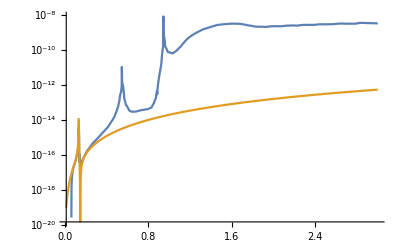

```mathematica
WidthFunc=Interpolation[width,InterpolationOrder->1];
LogPlot[{WidthFunc[ma],GammaPhoton[ma,1000]},{ma,0.015,3}]
```

#### Width function for f_a=1 TeV

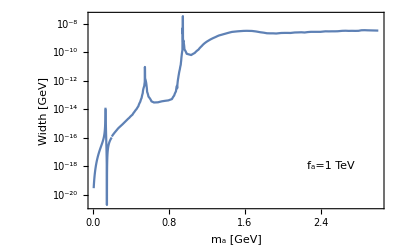

```mathematica
WidthFinal[ma_]:=Piecewise[{{GammaPhoton[ma,1000],ma≤0.2},{WidthFunc[ma],ma>0.2}}];

LifetimeFinal[ma_]:=1/WidthFinal[ma]*0.198*10^(-15); (*in meter*);

LogPlot[WidthFinal[ma],{ma,10^-2,3},Frame->True,FrameLabel->{"m_a [GeV]","Width [GeV]"},Epilog->Inset[Framed["f_a=1 TeV"],{2.5,Log[10^-18]}]]
```

#### Lifetime calculation

```mathematica
LifetimeFinal[0.4] 1/((1000*4 Pi^2)^2)
```

3.83866×10^-11

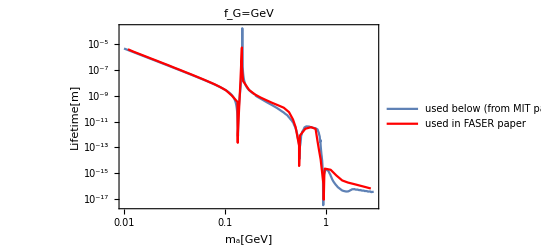

```mathematica
lifetimeFASER=Import["./lifetime-faser.csv","Data"]; 
lifetimeFASER[[All,2]]=lifetimeFASER[[All,2]]/10^9; 
Show[LogLogPlot[LifetimeFinal[ma] 1/((1000*4 Pi^2)^2),{ma,0.01,3},FrameLabel-> {"m_a[GeV]","Lifetime[m]"},PlotLegends->{"used below (from MIT paper)"},PlotLabel->"f_G=GeV",Frame->True],ListLogLogPlot[lifetimeFASER,Joined-> True,PlotStyle->Red,PlotLegends->{"used in FASER paper"}]]
```

#### Importing Pythia data

```mathematica
(*pi0=Import["/Users/soubhik/Documents/pythia8244/examples/mesons-pn-1M.txt","Data"];*)
pi0=Import["./mesons-pn-100K.txt","Data"];
(* I am not copying the simulation files, but here is the order of various quantities in pi0:
part.id(); part.px(); part.py(); part.pz(); part.e(); part.eta(); part.pT(); part.m()
*)
```

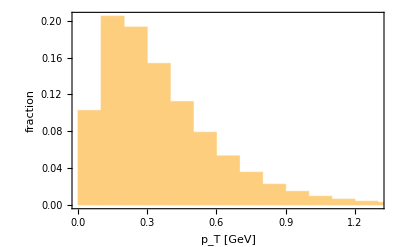

```mathematica
Histogram[pi0[[All,7]],{0.1},"Probability",Frame->True,FrameLabel->{"p_T [GeV]","fraction"}]
```

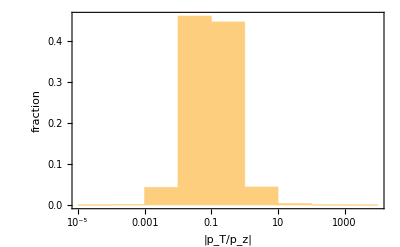

```mathematica
Histogram[Abs[pi0[[All,7]]/pi0[[All,4]]],(*{0.01},"Probability",*){"Log",10},"Probability",Frame-> True,FrameLabel->{"|p_T/p_z|","fraction"}]
```

#### Boost of axions, m_a=input

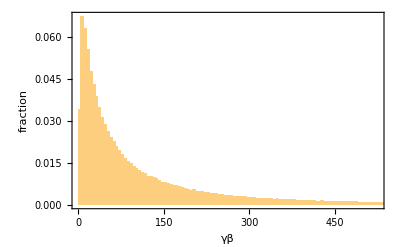

```mathematica
ma=0.05;
Histogram[Sqrt[pi0[[All,7]]^2+pi0[[All,4]]^2]/ma,{5.0},"Probability",FrameLabel->{"γβ","fraction"},Frame->True]
```

#### Energy distribution of axions at ND, m_a= input

```mathematica
ma=0.05;
enlist={};
dist=579; (* distance in m to HPTPC *)
length=10; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
For[i=1,i<Length[pi0]+1,i++,
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[enlist,pi0[[i]][[5]]],Continue]];
```

```mathematica
Length[enlist]/Length[pi0]//N
```

0.0102782

```mathematica
Naxions[0.05,1/(4 Pi^2),Length[enlist]/Length[pi0]]
```

4.13669×10^18

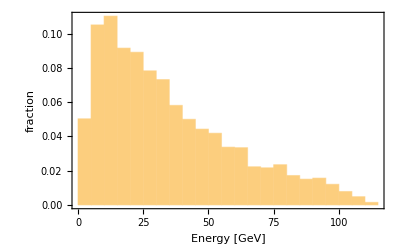

```mathematica
Histogram[enlist,{5.0},"Probability",FrameLabel->{"Energy [GeV]","fraction"},Frame->True]
```

```mathematica
Histogram[enlist,{1.0},NPOT*2.49*mixingAPi[0.05,1/(4 Pi^2)]^2/Length[pi0]#2&,Frame->True,FrameLabel->{"Energy [GeV]","N_a"}]
```

-Graphics-

# Main code

```mathematica
dist=574; (* distance in m to HPTPC *)
length=10; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
lifetime=Table[10^x,{x,-3,6,1/3}];
masslist=(*Table[0.001*y,{y,1,10,1}];*)Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
axions={};
For[nn=1,nn<Length[masslist]+1,nn++,ma=masslist[[nn]];
For[j=1,j<Length[lifetime]+1,j++,
(*fa=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime[[j]]/(0.198*10^(-15))];*)
fa=Sqrt[lifetime[[j]]/LifetimeFinal[ma]]*1000;
decayprob={};
list={};
For[i=1,i<Length[pi0]+1,i++,gabeta=Sqrt[(pi0[[i]][[7]])^2+(pi0[[i]][[4]])^2]/ma;
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[decayprob,Exp[-dist/(gabeta*lifetime[[j]])]-Exp[-(dist+length)/(gabeta*lifetime[[j]])]],Continue]];

AppendTo[axions,{ma,fa,Sum[decayprob[[i]],{i,Length[decayprob]}]*Naxions[ma,fa,Length[decayprob]/Length[pi0]]/Length[decayprob],lifetime[[j]]}]]]
```

General::munfl: Exp[-1015.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1032.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1444.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime/(0.198*10^(-15))]
```

{226.843,332.96,488.718,717.34,1052.91,1545.46,2268.43,3329.6,4887.18,7173.4,10529.1,15454.6,22684.3,33296.,48871.8,71734.,105291.,154546.,226843.,332960.,488718.,717340.,1.05291×10^6,1.54546×10^6,2.26843×10^6,3.3296×10^6,4.88718×10^6,7.1734×10^6}

```mathematica
Sqrt[lifetime/LifetimeFinal[ma]]*1000
```

{468.485,687.643,1009.32,1481.48,2174.52,3191.75,4684.85,6876.43,10093.2,14814.8,21745.2,31917.5,46848.5,68764.3,100932.,148148.,217452.,319175.,468485.,687643.,1.00932×10^6,1.48148×10^6,2.17452×10^6,3.19175×10^6,4.68485×10^6,6.87643×10^6,1.00932×10^7,1.48148×10^7}

## Results of Meson-mixing Simulation

```mathematica
axionfinallist={{0.001,0.011929721554934561,2.0487675502663442*^12,1/1000},{0.001,0.017510436561268168,1.959903006812782*^13,1/(100 10^(2/3))},{0.001,0.025701805960372127,4.025919003660666*^13,1/(100 10^(1/3))},{0.001,0.03772509196519874,3.7470294489789234*^13,1/100},{0.001,0.055372862357493946,2.1891345801797066*^13,1/(10 10^(2/3))},{0.001,0.08127624681446727,9.361483890300316*^12,1/(10 10^(1/3))},{0.001,0.11929721554934562,3.1918955688160273*^12,1/10},{0.001,0.1751043656126817,9.261984652881448*^11,1/10^(2/3)},{0.001,0.25701805960372126,2.3978628038851242*^11,1/10^(1/3)},{0.001,0.3772509196519875,5.7570030572175964*^10,1},{0.001,0.5537286235749393,1.3191325280990808*^10,10^(1/3)},{0.001,0.8127624681446727,2.9373227436936364*^9,10^(2/3)},{0.001,1.1929721554934563,6.434370141306026*^8,10},{0.001,1.7510436561268168,1.397447097619457*^8,10 10^(1/3)},{0.001,2.570180596037212,3.022212464186606*^7,10 10^(2/3)},{0.001,3.7725091965198745,6.522808169568702*^6,100},{0.001,5.537286235749394,1.406468148278193*^6,100 10^(1/3)},{0.001,8.127624681446726,303131.87043588026,100 10^(2/3)},{0.001,11.929721554934561,65319.54602944016,1000},{0.001,17.510436561268165,14073.846714983814,1000 10^(1/3)},{0.001,25.701805960372123,3032.236103244664,1000 10^(2/3)},{0.001,37.72509196519874,653.2872408875717,10000},{0.001,55.372862357493936,140.7476471009235,10000 10^(1/3)},{0.001,81.27624681446727,30.323279118493822,10000 10^(2/3)},{0.001,119.29721554934561,6.532964221327348,100000},{0.001,175.10436561268168,1.4074856524304649,100000 10^(1/3)},{0.001,257.0180596037212,0.3032337092404125,100000 10^(2/3)},{0.001,377.2509196519875,0.06532973415103163,1000000},{0.002,0.03384424832146014,1.1081547425434859*^9,1/1000},{0.002,0.04967656289945865,1.7558463881237823*^11,1/(100 10^(2/3))},{0.002,0.07291522264180708,1.3714179320996592*^12,1/(100 10^(1/3))},{0.002,0.10702491039214457,2.550176831609268*^12,1/100},{0.002,0.1570910850909074,2.2451832740970327*^12,1/(10 10^(2/3))},{0.002,0.2305781796463901,1.2663743277761604*^12,1/(10 10^(1/3))},{0.002,0.33844248321460135,5.2802576661288477*^11,1/10},{0.002,0.4967656289945865,1.767940389080127*^11,1/10^(2/3)},{0.002,0.7291522264180706,5.064284410950123*^10,1/10^(1/3)},{0.002,1.0702491039214455,1.2994880403128317*^10,1},{0.002,1.570910850909074,3.1025943674643817*^9,10^(1/3)},{0.002,2.3057817964639007,7.084676830790355*^8,10^(2/3)},{0.002,3.3844248321460135,1.574325213934995*^8,10},{0.002,4.9676562899458645,3.444832211059588*^7,10 10^(1/3)},{0.002,7.291522264180706,7.477485876548067*^6,10 10^(2/3)},{0.002,10.702491039214456,1.6166964284852832*^6,100},{0.002,15.709108509090742,348885.4719626954,100 10^(1/3)},{0.002,23.05781796463901,75223.29089848232,100 10^(2/3)},{0.002,33.844248321460135,16212.20098161299,1000},{0.002,49.676562899458645,3493.396932650972,1000 10^(1/3)},{0.002,72.91522264180706,752.6879971092225,1000 10^(2/3)},{0.002,107.02491039214455,162.16755899537728,10000},{0.002,157.0910850909074,34.938526121494625,10000 10^(1/3)},{0.002,230.57817964639008,7.527335737643814,10000 10^(2/3)},{0.002,338.44248321460134,1.6217211708176607,100000},{0.002,496.76562899458645,0.34938981948784786,100000 10^(1/3)},{0.002,729.1522264180707,0.07527381322589191,100000 10^(2/3)},{0.002,1070.2491039214456,0.01621725727861242,1000000},{0.003,0.062287863108691256,1.5768461150312144*^6,1/1000},{0.003,0.09142607985268074,4.0468950430312476*^9,1/(100 10^(2/3))},{0.003,0.13419513304932165,1.1692041035322188*^11,1/(100 10^(1/3))},{0.003,0.1969715180082405,4.0877751447992413*^11,1/100},{0.003,0.2891146498749027,5.0625984118530927*^11,1/(10 10^(2/3))},{0.003,0.4243622713451932,3.522595729988145*^11,1/(10 10^(1/3))},{0.003,0.6228786310869125,1.7021121202700275*^11,1/10},{0.003,0.9142607985268075,6.34141909736571*^10,1/10^(2/3)},{0.003,1.3419513304932165,1.9595062622549824*^10,1/10^(1/3)},{0.003,1.969715180082405,5.301963206098057*^9,1},{0.003,2.8911464987490265,1.3094132187603078*^9,10^(1/3)},{0.003,4.2436227134519315,3.053122649002281*^8,10^(2/3)},{0.003,6.2287863108691255,6.870592008411975*^7,10},{0.003,9.142607985268075,1.5138856835793795*^7,10 10^(1/3)},{0.003,13.419513304932163,3.2977962307387115*^6,10 10^(2/3)},{0.003,19.69715180082405,714245.1948573528,100},{0.003,28.911464987490273,154261.67217618224,100 10^(1/3)},{0.003,42.43622713451932,33273.203030413635,100 10^(2/3)},{0.003,62.287863108691255,7172.362280332946,1000},{0.003,91.42607985268076,1545.6260948557888,1000 10^(1/3)},{0.003,134.19513304932164,333.0338279465993,1000 10^(2/3)},{0.003,196.9715180082405,71.75384269848477,10000},{0.003,289.1146498749027,15.45928480493762,10000 10^(1/3)},{0.003,424.3622713451932,3.3306407518576018,10000 10^(2/3)},{0.003,622.8786310869125,0.7175686782572406,100000},{0.003,914.2607985268074,0.1545958733420793,100000 10^(1/3)},{0.003,1341.9513304932166,0.03330671005698731,100000 10^(2/3)},{0.003,1969.715180082405,0.007175717039135826,1000000},{0.004,0.09602441453434192,3373.8334985255174,1/1000},{0.004,0.1409445653273451,1.3813067982844317*^8,1/(100 10^(2/3))},{0.004,0.20687832976278805,1.4658509859131971*^10,1/(100 10^(1/3))},{0.004,0.3036558609126973,9.480917981119589*^10,1/100},{0.004,0.44570585025680615,1.6056689981746512*^11,1/(10 10^(2/3))},{0.004,0.6542067205818118,1.3408050948637688*^11,1/(10 10^(1/3))},{0.004,0.9602441453434193,7.310567466197371*^10,1/10},{0.004,1.409445653273451,2.9743393779152252*^10,1/10^(2/3)},{0.004,2.0687832976278804,9.785254109563013*^9,1/10^(1/3)},{0.004,3.036558609126973,2.768211974038583*^9,1},{0.004,4.457058502568061,7.042801325176936*^8,10^(1/3)},{0.004,6.542067205818118,1.6725923073102477*^8,10^(2/3)},{0.004,9.602441453434192,3.806774723641398*^7,10},{0.004,14.09445653273451,8.442881805263076*^6,10 10^(1/3)},{0.004,20.687832976278806,1.8454971484602995*^6,10 10^(2/3)},{0.004,30.36558609126973,400382.66419790895,100},{0.004,44.570585025680614,86544.50579313177,100 10^(1/3)},{0.004,65.42067205818118,18674.225476928914,100 10^(2/3)},{0.004,96.02441453434193,4026.1322016907975,1000},{0.004,140.9445653273451,867.6937989543915,1000 10^(1/3)},{0.004,206.87832976278804,186.9679849373144,1000 10^(2/3)},{0.004,303.6558609126973,40.28393503080602,10000},{0.004,445.7058502568062,8.679201153141596,10000 10^(1/3)},{0.004,654.2067205818119,1.8699062523278558,10000 10^(2/3)},{0.004,960.2441453434193,0.4028619946368994,100000},{0.004,1409.445653273451,0.08679427614631344,100000 10^(1/3)},{0.004,2068.7832976278805,0.018699288994874153,100000 10^(2/3)},{0.004,3036.5586091269734,0.004028642592441746,1000000},{0.005,0.1343397765390776,9.083256043086488,1/1000},{0.005,0.19718382561657063,5.876764267533823*^6,1/(100 10^(2/3))},{0.005,0.28942627482692024,2.279771405555417*^9,1/(100 10^(1/3))},{0.005,0.4248196742215374,2.712184017118516*^10,1/100},{0.005,0.6235500066938188,6.1951104420309875*^10,1/(10 10^(2/3))},{0.005,0.9152462431509236,6.113160597314062*^10,1/(10 10^(1/3))},{0.005,1.3433977653907763,3.704425293452721*^10,1/10},{0.005,1.9718382561657064,1.6259419124608484*^10,1/10^(2/3)},{0.005,2.8942627482692025,5.648971442789284*^9,1/10^(1/3)},{0.005,4.248196742215374,1.661179482300257*^9,1},{0.005,6.235500066938187,4.340730521414734*^8,10^(1/3)},{0.005,9.152462431509237,1.048265767841568*^8,10^(2/3)},{0.005,13.433977653907762,2.4106376699325778*^7,10},{0.005,19.718382561657066,5.379399730096523*^6,10 10^(1/3)},{0.005,28.94262748269202,1.1797781659737586*^6,10 10^(2/3)},{0.005,42.48196742215373,256382.7049561968,100},{0.005,62.35500066938187,55463.051384395534,100 10^(1/3)},{0.005,91.52462431509235,11972.167085921963,100 10^(2/3)},{0.005,134.33977653907763,2581.641268601433,1000},{0.005,197.18382561657063,556.4300392996419,1000 10^(1/3)},{0.005,289.42627482692023,119.90247861527621,1000 10^(2/3)},{0.005,424.8196742215373,25.83453348421988,10000},{0.005,623.5500066938187,5.566114337565641,10000 10^(1/3)},{0.005,915.2462431509236,1.1992062673170398,10000 10^(2/3)},{0.005,1343.3977653907762,0.2583634869817498,100000},{0.005,1971.838256165706,0.05566295877834571,100000 10^(1/3)},{0.005,2894.2627482692023,0.011992244223472894,100000 10^(2/3)},{0.005,4248.196742215374,0.0025836530252549054,1000000},{0.006,0.17675289946959047,0.028412289388727186,1/1000},{0.006,0.2594377763915422,288969.3729054004,1/(100 10^(2/3))},{0.006,0.3808025781810038,4.0808227499407154*^8,1/(100 10^(1/3))},{0.006,0.5589417453626734,8.90601641980624*^9,1/100},{0.006,0.8204142844867333,2.7239059257726532*^10,1/(10 10^(2/3))},{0.006,1.2042034859163113,3.1446412454965637*^10,1/(10 10^(1/3))},{0.006,1.7675289946959045,2.0977300893406986*^10,1/10},{0.006,2.5943777639154217,9.847593846998005*^9,1/10^(2/3)},{0.006,3.8080257818100387,3.5923841427127223*^9,1/10^(1/3)},{0.006,5.589417453626734,1.0935940636724017*^9,1},{0.006,8.20414284486733,2.9279043638180286*^8,10^(1/3)},{0.006,12.042034859163111,7.181471137478334*^7,10^(2/3)},{0.006,17.675289946959047,1.6674039250849374*^7,10},{0.006,25.943777639154217,3.742534655752737*^6,10 10^(1/3)},{0.006,38.080257818100385,823438.5043387596,10 10^(2/3)},{0.006,55.894174536267336,179239.81456057174,100},{0.006,82.04142844867332,38805.8876472131,100 10^(1/3)},{0.006,120.42034859163111,8379.767000684056,100 10^(2/3)},{0.006,176.75289946959046,1807.3099067319515,1000},{0.006,259.4377763915422,389.56818651123035,1000 10^(1/3)},{0.006,380.8025781810038,83.94946064168634,1000 10^(2/3)},{0.006,558.9417453626734,18.088318426051934,10000},{0.006,820.4142844867331,3.897205679904996,10000 10^(1/3)},{0.006,1204.2034859163111,0.8396470752917325,10000 10^(2/3)},{0.006,1767.5289946959047,0.1808984352080669,100000},{0.006,2594.377763915422,0.03897358208244543,100000 10^(1/3)},{0.006,3808.025781810038,0.008396623289937847,100000 10^(2/3)},{0.006,5589.417453626734,0.0018089996057280462,1000000},{0.007,0.2229115585330641,0.00009902743402465871,1/1000},{0.007,0.3271894223593255,15790.756127443545,1/(100 10^(2/3))},{0.007,0.48024839451270607,8.08889015229722*^7,1/(100 10^(1/3))},{0.007,0.7049082417424246,3.233191055288937*^9,1/100},{0.007,1.0346638009702918,1.318751168492123*^10,1/(10 10^(2/3))},{0.007,1.518678769299261,1.7689746698802097*^10,1/(10 10^(1/3))},{0.007,2.229115585330641,1.2905494117679188*^10,1/10},{0.007,3.271894223593256,6.438611586970365*^9,1/10^(2/3)},{0.007,4.802483945127061,2.455454705199281*^9,1/10^(1/3)},{0.007,7.049082417424247,7.71421541385038*^8,1},{0.007,10.346638009702916,2.111974551369888*^8,10^(1/3)},{0.007,15.186787692992606,5.256362119380494*^7,10^(2/3)},{0.007,22.291155853306407,1.2314678135723412*^7,10},{0.007,32.71894223593255,2.779355645835035*^6,10 10^(1/3)},{0.007,48.024839451270594,613431.3994362723,10 10^(2/3)},{0.007,70.49082417424246,133743.61671410964,100},{0.007,103.46638009702916,28978.88315908291,100 10^(1/3)},{0.007,151.86787692992607,6260.0914486049,100 10^(2/3)},{0.007,222.91155853306407,1350.3886905950596,1000},{0.007,327.1894223593256,291.1024090997179,1000 10^(1/3)},{0.007,480.248394512706,62.73314394901552,1000 10^(2/3)},{0.007,704.9082417424246,13.517150780469654,10000},{0.007,1034.6638009702915,2.9123523883409006,10000 10^(1/3)},{0.007,1518.6787692992605,0.6274643581002898,10000 10^(2/3)},{0.007,2229.115585330641,0.13518480379654577,100000},{0.007,3271.8942235932554,0.02912485367459224,100000 10^(1/3)},{0.007,4802.48394512706,0.0062747765685445475,100000 10^(2/3)},{0.007,7049.082417424246,0.0013518613376492952,1000000},{0.008,0.272543813682189,3.7547941367558846*^-7,1/1000},{0.008,0.4000396101176429,937.6736467352431,1/(100 10^(2/3))},{0.008,0.5871778467504944,1.737202307887016*^7,1/(100 10^(1/3))},{0.008,0.8618592134242794,1.270186600668384*^9,1/100},{0.008,1.2650363222574905,6.89257897534496*^9,1/(10 10^(2/3))},{0.008,1.8568193873248608,1.0690861644466465*^10,1/(10 10^(1/3))},{0.008,2.7254381368218903,8.488690738523711*^9,1/10},{0.008,4.000396101176428,4.479308897329416*^9,1/10^(2/3)},{0.008,5.871778467504944,1.77957617579535*^9,1/10^(1/3)},{0.008,8.618592134242794,5.755978840296825*^8,1},{0.008,12.650363222574903,1.6087939679829898*^8,10^(1/3)},{0.008,18.568193873248607,4.059700417537518*^7,10^(2/3)},{0.008,27.254381368218905,9.592601830578128*^6,10},{0.008,40.00396101176428,2.176416588574153*^6,10 10^(1/3)},{0.008,58.71778467504944,481815.5373049055,10 10^(2/3)},{0.008,86.18592134242795,105215.74652126204,100},{0.008,126.50363222574903,22815.61319531861,100 10^(1/3)},{0.008,185.68193873248606,4930.54919661376,100 10^(2/3)},{0.008,272.543813682189,1063.7772749792764,1000},{0.008,400.03961011764284,229.33684851948277,1000 10^(1/3)},{0.008,587.1778467504944,49.424457940369564,1000 10^(2/3)},{0.008,861.8592134242793,10.649711405182586,10000},{0.008,1265.0363222574904,2.294564314850975,10000 10^(1/3)},{0.008,1856.8193873248606,0.49436425380151405,10000 10^(2/3)},{0.008,2725.43813682189,0.10650908574114633,100000},{0.008,4000.3961011764286,0.022946840514030165,100000 10^(1/3)},{0.008,5871.778467504943,0.004943762283609205,100000 10^(2/3)},{0.008,8618.592134242794,0.001065102832599924,1000000},{0.009000000000000001,0.32543184806701325,1.5262782478121702*^-9,1/1000},{0.009000000000000001,0.47766862825365874,59.67732961954139,1/(100 10^(2/3))},{0.009000000000000001,0.7011216627167589,3.9893622861278304*^6,1/(100 10^(1/3))},{0.009000000000000001,1.0291058630496264,5.330040042750338*^8,1/100},{0.009000000000000001,1.5105208320898194,3.842155247845787*^9,1/(10 10^(2/3))},{0.009000000000000001,2.217141371069316,6.8668953116987095*^9,1/(10 10^(1/3))},{0.009000000000000001,3.2543184806701326,5.91203381302364*^9,1/10},{0.009000000000000001,4.776686282536588,3.2873803043745656*^9,1/10^(2/3)},{0.009000000000000001,7.011216627167588,1.356646196488524*^9,1/10^(1/3)},{0.009000000000000001,10.291058630496261,4.5088906162861043*^8,1},{0.009000000000000001,15.105208320898193,1.2848121041579463*^8,10^(1/3)},{0.009000000000000001,22.17141371069316,3.2849619653821416*^7,10^(2/3)},{0.009000000000000001,32.543184806701326,7.825436225772368*^6,10},{0.009000000000000001,47.76686282536587,1.7844345745548536*^6,10 10^(1/3)},{0.009000000000000001,70.11216627167587,396204.2182883529,10 10^(2/3)},{0.009000000000000001,102.91058630496262,86656.54477065612,100},{0.009000000000000001,151.0520832089819,18805.851951378703,100 10^(1/3)},{0.009000000000000001,221.71413710693156,4065.5535909420078,100 10^(2/3)},{0.009000000000000001,325.4318480670133,877.3083612943421,1000},{0.009000000000000001,477.6686282536587,189.15224321207114,1000 10^(1/3)},{0.009000000000000001,701.1216627167588,40.765839050223974,1000 10^(2/3)},{0.009000000000000001,1029.1058630496261,8.784157770490646,10000},{0.009000000000000001,1510.5208320898191,1.8926318969306917,10000 10^(1/3)},{0.009000000000000001,2217.1413710693155,0.4077694323977104,10000 10^(2/3)},{0.009000000000000001,3254.3184806701324,0.08785268633035072,100000},{0.009000000000000001,4776.686282536587,0.018927430037573606,100000 10^(1/3)},{0.009000000000000001,7011.216627167587,0.00407780544044075,100000 10^(2/3)},{0.009000000000000001,10291.058630496264,0.0008785379753319071,1000000},{0.01,0.3813964291317639,6.587015652043289*^-12,1/1000},{0.01,0.5598133993532757,4.033413175077015,1/(100 10^(2/3))},{0.01,0.821693697575759,971117.1503089359,1/(100 10^(1/3))},{0.01,1.2060814075113695,2.368516219492709*^8,1/100},{0.01,1.7702854066377829,2.265782694413098*^9,1/(10 10^(2/3))},{0.01,2.598423623344975,4.65423930464663*^9,1/(10 10^(1/3))},{0.01,3.813964291317639,4.331823795076042*^9,1/10},{0.01,5.598133993532756,2.530790161692056*^9,1/10^(2/3)},{0.01,8.21693697575759,1.0822519338425424*^9,1/10^(1/3)},{0.01,12.060814075113694,3.6900508428517616*^8,1},{0.01,17.702854066377828,1.0707491375578652*^8,10^(1/3)},{0.01,25.98423623344975,2.7720943463702574*^7,10^(2/3)},{0.01,38.13964291317639,6.655491549012642*^6,10},{0.01,55.981339935327554,1.5250079434618722*^6,10 10^(1/3)},{0.01,82.1693697575759,339574.7145360035,10 10^(2/3)},{0.01,120.60814075113694,74385.74493197975,100},{0.01,177.0285406637783,16155.449729591823,100 10^(1/3)},{0.01,259.8423623344975,3493.885501675584,100 10^(2/3)},{0.01,381.3964291317639,754.0814937377584,1000},{0.01,559.8133993532756,162.59739280640719,1000 10^(1/3)},{0.01,821.6936975757591,35.044129417180876,1000 10^(2/3)},{0.01,1206.0814075113694,7.551388843527751,10000},{0.01,1770.285406637783,1.6270334919527505,10000 10^(1/3)},{0.01,2598.423623344975,0.35054735179365215,10000 10^(2/3)},{0.01,3813.964291317639,0.0755244989031917,100000},{0.01,5598.133993532756,0.016271396185020357,100000 10^(1/3)},{0.01,8216.93697575759,0.003505579654998942,100000 10^(2/3)},{0.01,12060.814075113694,0.0007552556031828888,1000000},{0.02,1.0852769487015637,1.07567066655445*^-34,1/1000},{0.02,1.5929687104712698,6.027391402616036*^-11,1/(100 10^(2/3))},{0.02,2.338158306574602,5.136083125269662,1/(100 10^(1/3))},{0.02,3.431947049974659,493613.7214055474,1/100},{0.02,5.037409366470527,7.821198940763077*^7,1/(10 10^(2/3))},{0.02,7.3939057788179925,6.108810286839956*^8,1/(10 10^(1/3))},{0.02,10.852769487015635,1.135944492015258*^9,1/10},{0.02,15.929687104712698,1.000088912330795*^9,1/10^(2/3)},{0.02,23.38158306574602,5.640906640811574*^8,1/10^(1/3)},{0.02,34.319470499746586,2.3520249803521922*^8,1},{0.02,50.37409366470527,7.875070160995738*^7,10^(1/3)},{0.02,73.93905778817991,2.2558223850646883*^7,10^(2/3)},{0.02,108.52769487015637,5.788407547023131*^6,10},{0.02,159.29687104712696,1.38201199971482*^6,10 10^(1/3)},{0.02,233.81583065746017,315578.10124743043,10 10^(2/3)},{0.02,343.1947049974659,70126.35489601217,100},{0.02,503.74093664705265,15344.57582535769,100 10^(1/3)},{0.02,739.3905778817992,3330.7529071333433,100 10^(2/3)},{0.02,1085.2769487015637,720.1372784959824,1000},{0.02,1592.9687104712696,155.4066860414847,1000 10^(1/3)},{0.02,2338.1583065746017,33.50727757708915,1000 10^(2/3)},{0.02,3431.947049974659,7.221522907839403,10000},{0.02,5037.409366470527,1.5560901326060999,10000 10^(1/3)},{0.02,7393.9057788179925,0.3352754891050706,10000 10^(2/3)},{0.02,10852.769487015637,0.0722355183927037,100000},{0.02,15929.687104712695,0.015562931093605029,100000 10^(1/3)},{0.02,23381.583065746017,0.003352957906581831,100000 10^(2/3)},{0.02,34319.470499746596,0.0007223754873548751,1000000},{0.03,2.007792304498312,5.415258535764963*^-57,1/1000},{0.03,2.94703607407985,2.8753022972302175*^-21,1/(100 10^(2/3))},{0.03,4.325657391190223,0.00008656676682295707,1/(100 10^(1/3))},{0.03,6.349196750773,3151.9463774296564,1/100},{0.03,9.319346340773034,8.089309444420865*^6,1/(10 10^(2/3))},{0.03,13.678929733703074,2.3371136875530195*^8,1/(10 10^(1/3))},{0.03,20.07792304498312,8.171024386321852*^8,1/10},{0.03,29.470360740798498,1.0119591615511302*^9,1/10^(2/3)},{0.03,43.25657391190223,7.041291312098321*^8,1/10^(1/3)},{0.03,63.49196750773001,3.4023396958795846*^8,1},{0.03,93.19346340773033,1.2675817101727365*^8,10^(1/3)},{0.03,136.78929733703072,3.9168429981786974*^7,10^(2/3)},{0.03,200.7792304498312,1.0598056184065403*^7,10},{0.03,294.703607407985,2.61737668126756*^6,10 10^(1/3)},{0.03,432.56573911902217,610286.4941377387,10 10^(2/3)},{0.03,634.9196750773001,137335.77034105512,100},{0.03,931.9346340773034,30260.952230625015,100 10^(1/3)},{0.03,1367.8929733703071,6591.941207130568,100 10^(2/3)},{0.03,2007.7923044983122,1427.6995916514095,1000},{0.03,2947.0360740798496,308.3525488993775,1000 10^(1/3)},{0.03,4325.657391190222,66.50956663270733,1000 10^(2/3)},{0.03,6349.1967507730005,14.336783463908873,10000},{0.03,9319.346340773034,3.0895409032637273,10000 10^(1/3)},{0.03,13678.929733703071,0.665698927467599,10000 10^(2/3)},{0.03,20077.92304498312,0.14342824097053306,100000},{0.03,29470.360740798496,0.030901453397443136,100000 10^(1/3)},{0.03,43256.57391190222,0.006657593884568319,100000 10^(2/3)},{0.03,63491.967507730005,0.0014343428787565089,1000000},{0.04,3.119340579029261,2.974041884528602*^-79,1/1000},{0.04,4.578565817362953,1.5095025618657019*^-31,1/(100 10^(2/3))},{0.04,6.7204155534847825,1.625924755136131*^-9,1/(100 10^(1/3))},{0.04,9.86422102752093,22.211691843845177,1/100},{0.04,14.478696399857437,909385.7464724012,1/(10 10^(2/3))},{0.04,21.251819971833044,9.65045560260457*^7,1/(10 10^(1/3))},{0.04,31.19340579029261,6.24177893442083*^8,1/10},{0.04,45.78565817362952,1.0570949931660115*^9,1/10^(2/3)},{0.04,67.20415553484781,8.827213791903837*^8,1/10^(1/3)},{0.04,98.6422102752093,4.812924877110315*^8,1},{0.04,144.78696399857438,1.9581615313897347*^8,10^(1/3)},{0.04,212.5181997183304,6.442139156846993*^7,10^(2/3)},{0.04,311.9340579029261,1.822457194543212*^7,10},{0.04,457.8565817362952,4.636640569862764*^6,10 10^(1/3)},{0.04,672.0415553484783,1.1011540707802433*^6,10 10^(2/3)},{0.04,986.4221027520929,250619.6797127512,100},{0.04,1447.8696399857438,55583.86002583352,100 10^(1/3)},{0.04,2125.181997183304,12149.862753514699,100 10^(2/3)},{0.04,3119.340579029261,2635.926272196989,1000},{0.04,4578.565817362952,569.7672675000181,1000 10^(1/3)},{0.04,6720.415553484782,122.94209002824344,1000 10^(2/3)},{0.04,9864.221027520929,26.506111764442636,10000},{0.04,14478.696399857437,5.7124773008547205,10000 10^(1/3)},{0.04,21251.81997183304,1.2309069987915122,10000 10^(2/3)},{0.04,31193.405790292607,0.2652099908169121,100000},{0.04,45785.65817362951,0.05713967258567391,100000 10^(1/3)},{0.04,67204.15553484781,0.012310560515727119,100000 10^(2/3)},{0.04,98642.21027520928,0.002652248987504069,1000000},{0.05,4.41173107791681,1.6348589156835418*^-101,1/1000},{0.05,6.475535645111817,7.943507634141861*^-42,1/(100 10^(2/3))},{0.05,9.504786477355733,3.087566821994373*^-14,1/(100 10^(1/3))},{0.05,13.951118630366892,0.15824775826886334,1/100},{0.05,20.477441708161138,102384.51572876475,1/(10 10^(2/3))},{0.05,30.056773942012537,3.9717994580719896*^7,1/(10 10^(1/3))},{0.05,44.11731077916811,4.725145241813576*^8,1/10},{0.05,64.75535645111819,1.079307172482065*^9,1/10^(2/3)},{0.05,95.04786477355732,1.0650299362625642*^9,1/10^(1/3)},{0.05,139.51118630366892,6.45382003526758*^8,1},{0.05,204.77441708161135,2.832702959179019*^8,10^(1/3)},{0.05,300.56773942012535,9.841592740596922*^7,10^(2/3)},{0.05,441.173107791681,2.894093570733699*^7,10},{0.05,647.5535645111818,7.562385899998297*^6,10 10^(1/3)},{0.05,950.478647735573,1.826280213219102*^6,10 10^(2/3)},{0.05,1395.111863036689,419979.3614269629,100},{0.05,2047.7441708161134,93719.47064817521,100 10^(1/3)},{0.05,3005.6773942012533,20554.000584624988,100 10^(2/3)},{0.05,4411.73107791681,4466.678922819309,1000},{0.05,6475.535645111818,966.2728328583969,1000 10^(1/3)},{0.05,9504.78647735573,208.5781347548203,1000 10^(2/3)},{0.05,13951.118630366893,44.97714712352685,10000},{0.05,20477.441708161135,9.694079516743777,10000 10^(1/3)},{0.05,30056.773942012533,2.0889313657726993,10000 10^(2/3)},{0.05,44117.3107791681,0.45008717032823986,100000},{0.05,64755.356451118176,0.09697239756423706,100000 10^(1/3)},{0.05,95047.8647735573,0.02089247540801553,100000 10^(2/3)},{0.05,139511.18630366892,0.004501187948401781,1000000},{0.060000000000000005,5.891853555642961,9.010336883018392*^-124,1/1000},{0.060000000000000005,8.648058333909225,4.193374526829437*^-52,1/(100 10^(2/3))},{0.060000000000000005,12.693613688864897,5.909578396277168*^-19,1/(100 10^(1/3))},{0.060000000000000005,18.63167687599337,0.0011392603482775429,1/100},{0.060000000000000005,27.347561673154118,11586.934932049777,1/(10 10^(2/3))},{0.060000000000000005,40.140730995104995,1.6363058547478288*^7,1/(10 10^(1/3))},{0.060000000000000005,58.91853555642962,3.571085465650517*^8,1/10},{0.060000000000000005,86.48058333909225,1.092216811962453*^9,1/10^(2/3)},{0.060000000000000005,126.93613688864893,1.260920945699563*^9,1/10^(1/3)},{0.060000000000000005,186.3167687599337,8.411362701109087*^8,1},{0.060000000000000005,273.4756167315412,3.9486340021152866*^8,10^(1/3)},{0.060000000000000005,401.4073099510499,1.4404544292715195*^8,10^(2/3)},{0.060000000000000005,589.1853555642962,4.3850333100858584*^7,10},{0.060000000000000005,864.8058333909225,1.1740149833086383*^7,10 10^(1/3)},{0.060000000000000005,1269.3613688864896,2.879586786299178*^6,10 10^(2/3)},{0.060000000000000005,1863.1676875993371,668586.4522995099,100},{0.060000000000000005,2734.756167315412,150066.09559049917,100 10^(1/3)},{0.060000000000000005,4014.073099510498,33017.78411458551,100 10^(2/3)},{0.060000000000000005,5891.8535556429615,7187.059471613694,1000},{0.060000000000000005,8648.058333909226,1556.0171329848497,1000 10^(1/3)},{0.060000000000000005,12693.613688864894,336.00728688451807,1000 10^(2/3)},{0.060000000000000005,18631.67687599337,72.46851830975038,10000},{0.060000000000000005,27347.56167315412,15.62069081341701,10000 10^(1/3)},{0.060000000000000005,40140.73099510499,3.3661592862103484,10000 10^(2/3)},{0.060000000000000005,58918.53555642961,0.7252954405706992,100000},{0.060000000000000005,86480.58333909225,0.15626800922139644,100000 10^(1/3)},{0.060000000000000005,126936.13688864895,0.033667706475163955,100000 10^(2/3)},{0.060000000000000005,186316.7687599337,0.007253565929811114,1000000},{0.06999999999999999,7.584103871754671,5.023598111309174*^-146,1/1000},{0.06999999999999999,11.13194210853121,2.2417140214070325*^-62,1/(100 10^(2/3))},{0.06999999999999999,16.339456474113387,1.1480720501303716*^-23,1/(100 10^(1/3))},{0.06999999999999999,23.983042246046306,8.349202334268852*^-6,1/100},{0.06999999999999999,35.202291844095924,1331.3504405889435,1/(10 10^(2/3))},{0.06999999999999999,51.66989818738235,6.819906140796026*^6,1/(10 10^(1/3))},{0.06999999999999999,75.84103871754671,2.725968472457205*^8,1/10},{0.06999999999999999,111.31942108531207,1.111865660535291*^9,1/10^(2/3)},{0.06999999999999999,163.39456474113385,1.4914581588924716*^9,1/10^(1/3)},{0.06999999999999999,239.83042246046307,1.0880881916559515*^9,1},{0.06999999999999999,352.02291844095924,5.428523057357768*^8,10^(1/3)},{0.06999999999999999,516.6989818738234,2.070243297552912*^8,10^(2/3)},{0.06999999999999999,758.410387175467,6.504010325495698*^7,10},{0.06999999999999999,1113.1942108531207,1.7806482645832285*^7,10 10^(1/3)},{0.06999999999999999,1633.9456474113383,4.431744729038003*^6,10 10^(2/3)},{0.06999999999999999,2398.3042246046302,1.0382753067291338*^6,100},{0.06999999999999999,3520.2291844095926,234333.07016912926,100 10^(1/3)},{0.06999999999999999,5166.989818738235,51719.6363061552,100 10^(2/3)},{0.06999999999999999,7584.103871754671,11276.19359080783,1000},{0.06999999999999999,11131.942108531208,2443.2679822449254,1000 10^(1/3)},{0.06999999999999999,16339.456474113384,527.8009134560996,1000 10^(2/3)},{0.06999999999999999,23983.042246046305,113.85398923776047,10000},{0.06999999999999999,35202.291844095926,24.543430186845786,10000 10^(1/3)},{0.06999999999999999,51669.89818738234,5.289157666800903,10000 10^(2/3)},{0.06999999999999999,75841.0387175467,1.139658196342428,100000},{0.06999999999999999,111319.42108531209,0.24554629329176045,100000 10^(1/3)},{0.06999999999999999,163394.56474113383,0.052902783303634134,100000 10^(2/3)},{0.06999999999999999,239830.42246046307,0.01139770297526586,1000000},{0.08,9.54096499352954,2.8625308422874045*^-168,1/1000},{0.08,14.004221429910464,1.2266341871196022*^-72,1/(100 10^(2/3))},{0.08,20.555385958439867,2.2853385306270767*^-28,1/(100 10^(1/3))},{0.08,30.17118045548701,6.285917468115028*^-8,1/100},{0.08,44.28523657585714,156.97635984104005,1/(10 10^(2/3))},{0.08,65.00183781251319,2.908258065575725*^6,1/(10 10^(1/3))},{0.08,95.40964993529539,2.1264250049685588*^8,1/10},{0.08,140.04221429910461,1.1538896941742008*^9,1/10^(2/3)},{0.08,205.55385958439868,1.7897618754197426*^9,1/10^(1/3)},{0.08,301.7118045548701,1.4210954702516508*^9,1},{0.08,442.85236575857135,7.498830832609406*^8,10^(1/3)},{0.08,650.0183781251319,2.979196345219129*^8,10^(2/3)},{0.08,954.0964993529541,9.636109629590227*^7,10},{0.08,1400.4221429910463,2.6932890959182367*^7,10 10^(1/3)},{0.08,2055.5385958439865,6.796362421073004*^6,10 10^(2/3)},{0.08,3017.1180455487006,1.6059017143240946*^6,100},{0.08,4428.523657585713,364354.8635088067,100 10^(1/3)},{0.08,6500.183781251319,80660.95215997302,100 10^(2/3)},{0.08,9540.96499352954,17614.21465173024,1000},{0.08,14004.221429910463,3819.571894136397,1000 10^(1/3)},{0.08,20555.385958439867,825.4254213034592,1000 10^(2/3)},{0.08,30171.18045548701,178.08742400864065,10000},{0.08,44285.23657585713,38.39338322384279,10000 10^(1/3)},{0.08,65001.837812513186,8.274170359388256,10000 10^(2/3)},{0.08,95409.64993529541,1.7828728956645123,100000},{0.08,140042.2142991046,0.3841340266099617,100000 10^(1/3)},{0.08,205553.85958439865,0.08276173833773678,100000 10^(2/3)},{0.08,301711.80455487006,0.01783073314244818,1000000},{0.09,11.870534661396999,1.6881834887127904*^-190,1/1000},{0.09,17.42356208228091,6.958783522375928*^-83,1/(100 10^(2/3))},{0.09,25.574291663739572,4.718439249811501*^-33,1/(100 10^(1/3))},{0.09,37.53792657399015,4.919112854247163*^-10,1/100},{0.09,55.098141133353764,19.23368295783754,1/(10 10^(2/3))},{0.09,80.87301120287407,1.2857500478743135*^6,1/(10 10^(1/3))},{0.09,118.70534661396998,1.717843291387315*^8,1/10},{0.09,174.23562082280904,1.2383060097189608*^9,1/10^(2/3)},{0.09,255.74291663739572,2.213163493941348*^9,1/10^(1/3)},{0.09,375.3792657399014,1.9054167591050744*^9,1},{0.09,550.9814113335375,1.0595050237548759*^9,10^(1/3)},{0.09,808.7301120287406,4.37239785955036*^8,10^(2/3)},{0.09,1187.0534661396998,1.4531912395895475*^8,10},{0.09,1742.3562082280905,4.140880436391735*^7,10 10^(1/3)},{0.09,2557.4291663739573,1.0587256060805026*^7,10 10^(2/3)},{0.09,3753.7926573990144,2.52209608460759*^6,100},{0.09,5509.814113335376,575113.6836181962,100 10^(1/3)},{0.09,8087.301120287407,127694.49252670097,100 10^(2/3)},{0.09,11870.534661396998,27928.939162765077,1000},{0.09,17423.562082280907,6061.025124462124,1000 10^(1/3)},{0.09,25574.29166373957,1310.306096381885,1000 10^(2/3)},{0.09,37537.92657399014,282.7517750035146,10000},{0.09,55098.141133353754,60.96275252090859,10000 10^(1/3)},{0.09,80873.01120287406,13.138611073936064,10000 10^(2/3)},{0.09,118705.34661396997,2.8310868915608847,100000},{0.09,174235.62082280905,0.6099850997611582,100000 10^(1/3)},{0.09,255742.9166373957,0.13142189894614087,100000 10^(2/3)},{0.09,375379.2657399014,0.02831444916595273,1000000},{0.09999999999999999,14.81304985460236,1.0488285205518308*^-212,1/1000},{0.09999999999999999,21.74258372783455,4.165908445280817*^-93,1/(100 10^(2/3))},{0.09999999999999999,31.91374847192708,1.0281986584144012*^-37,1/(100 10^(1/3))},{0.09999999999999999,46.8429766341695,4.069673565380031*^-12,1/100},{0.09999999999999999,68.75608679687171,2.4919744910238104,1/(10 10^(2/3))},{0.09999999999999999,100.92013384500774,599987.9162688048,1/(10 10^(1/3))},{0.09999999999999999,148.13049854602357,1.4633467349744758*^8,1/10},{0.09999999999999999,217.42583727834545,1.3998746053515396*^9,1/10^(2/3)},{0.09999999999999999,319.13748471927073,2.875541165474159*^9,1/10^(1/3)},{0.09999999999999999,468.429766341695,2.6763423255623527*^9,1},{0.09999999999999999,687.560867968717,1.5636048803629444*^9,10^(1/3)},{0.09999999999999999,1009.2013384500773,6.686506179584008*^8,10^(2/3)},{0.09999999999999999,1481.304985460236,2.2798340194324172*^8,10},{0.09999999999999999,2174.258372783455,6.6154381444668025*^7,10 10^(1/3)},{0.09999999999999999,3191.3748471927074,1.712690492645624*^7,10 10^(2/3)},{0.09999999999999999,4684.29766341695,4.1119802126513803*^6,100},{0.09999999999999999,6875.608679687171,942199.752110221,100 10^(1/3)},{0.09999999999999999,10092.013384500773,209800.3575852984,100 10^(2/3)},{0.09999999999999999,14813.049854602357,45957.94450509218,1000},{0.09999999999999999,21742.583727834546,9981.364881219142,1000 10^(1/3)},{0.09999999999999999,31913.748471927072,2158.6366600211363,1000 10^(2/3)},{0.09999999999999999,46842.97663416949,465.8961938635911,10000},{0.09999999999999999,68756.0867968717,100.45798374544471,10000 10^(1/3)},{0.09999999999999999,100920.13384500773,21.651408565671275,10000 10^(2/3)},{0.09999999999999999,148130.49854602356,4.665494843461859,100000},{0.09999999999999999,217425.83727834545,1.0052344706565373,100000 10^(1/3)},{0.09999999999999999,319137.48471927067,0.21657961152195887,100000 10^(2/3)},{0.09999999999999999,468429.766341695,0.04666150392849742,1000000},{0.11,19.002463116164282,7.061102386358906*^-235,1/1000},{0.11,27.891801444921327,2.706718958230276*^-103,1/(100 10^(2/3))},{0.11,40.93956573351571,2.431954836375377*^-42,1/(100 10^(1/3))},{0.11,60.09106460041992,3.6591357635771573*^-14,1/100},{0.11,88.20162061112684,0.3510567114875531,1/(10 10^(2/3))},{0.11,129.4622741360916,304003.70139731007,1/(10 10^(1/3))},{0.11,190.02463116164284,1.352237245363996*^8,1/10},{0.11,278.9180144492133,1.7154929288588145*^9,1/10^(2/3)},{0.11,409.395657335157,4.042422599627463*^9,1/10^(1/3)},{0.11,600.9106460041992,4.0573511341721935*^9,1},{0.11,882.0162061112684,2.4847154386982656*^9,10^(1/3)},{0.11,1294.6227413609158,1.098765189050112*^9,10^(2/3)},{0.11,1900.2463116164286,3.838088104083425*^8,10},{0.11,2789.180144492133,1.1329905144033095*^8,10 10^(1/3)},{0.11,4093.95657335157,2.96848192639519*^7,10 10^(2/3)},{0.11,6009.106460041992,7.18089476921725*^6,100},{0.11,8820.162061112682,1.6530795822949244*^6,100 10^(1/3)},{0.11,12946.227413609158,369121.19472732843,100 10^(2/3)},{0.11,19002.463116164286,80981.44485088927,1000},{0.11,27891.801444921326,17601.5143952826,1000 10^(1/3)},{0.11,40939.5657335157,3808.044431045931,1000 10^(2/3)},{0.11,60091.06460041993,822.031626467781,10000},{0.11,88201.62061112683,177.26372052007304,10000 10^(1/3)},{0.11,129462.2741360916,38.20659727520889,10000 10^(2/3)},{0.11,190024.63116164284,8.232992773966775,100000},{0.11,278918.0144492133,1.7739077213037657,100000 10^(1/3)},{0.11,409395.65733515704,0.3821931578695393,100000 10^(2/3)},{0.11,600910.6460041992,0.08234265245978753,1000000},{0.12,26.775705714506973,5.427381772835306*^-257,1/1000},{0.12,39.3013612378174,2.0104841460121325*^-113,1/(100 10^(2/3))},{0.12,57.686509241418776,6.576710915148159*^-47,1/(100 10^(1/3))},{0.12,84.67221601622822,3.7650817705451423*^-16,1/100},{0.12,124.28181665655745,0.05662986677921863,1/(10 10^(2/3))},{0.12,182.42075946723534,176197.5846590055,1/(10 10^(1/3))},{0.12,267.7570571450698,1.4280985186821914*^8,1/10},{0.12,393.013612378174,2.4013946916264176*^9,1/10^(2/3)},{0.12,576.8650924141878,6.482173626564766*^9,1/10^(1/3)},{0.12,846.7221601622822,7.001871288401832*^9,1},{0.12,1242.8181665655745,4.485961521088442*^9,10^(1/3)},{0.12,1824.2075946723533,2.047697989127835*^9,10^(2/3)},{0.12,2677.5705714506976,7.319252283974495*^8,10},{0.12,3930.13612378174,2.196157920188772*^8,10 10^(1/3)},{0.12,5768.650924141877,5.8202269708720736*^7,10 10^(2/3)},{0.12,8467.221601622821,1.4182381377457753*^7,100},{0.12,12428.181665655744,3.2795890656300224*^6,100 10^(1/3)},{0.12,18242.075946723533,734303.8919254151,100 10^(2/3)},{0.12,26775.705714506974,161341.05542438684,1000},{0.12,39301.3612378174,35094.74635456116,1000 10^(1/3)},{0.12,57686.50924141877,7595.491034478198,1000 10^(2/3)},{0.12,84672.21601622822,1639.90674097714,10000},{0.12,124281.81665655745,353.66044980812546,10000 10^(1/3)},{0.12,182420.75946723533,76.22927537940488,10000 10^(2/3)},{0.12,267757.05714506976,16.426649057871096,100000},{0.12,393013.61237817403,3.5393694617827687,100000 10^(1/3)},{0.12,576865.0924141876,0.7625695670855541,100000 10^(2/3)},{0.12,846722.1601622822,0.16429418664940257,1000000},{0.121,28.03967199755911,3.3716803968816883*^-259,1/1000},{0.121,41.15661002238031,1.972868041758592*^-114,1/(100 10^(2/3))},{0.121,60.409642048656956,2.3223588983269604*^-47,1/(100 10^(1/3))},{0.121,88.66922835633005,2.408500834146465*^-16,1/100},{0.121,130.1486284420353,0.047704597792421505,1/(10 10^(2/3))},{0.121,191.03206150923626,168670.86942811048,1/(10 10^(1/3))},{0.121,280.3967199755911,1.4515650319523776*^8,1/10},{0.121,411.5661002238031,2.510547834064132*^9,1/10^(2/3)},{0.121,604.0964204865695,6.86907300303145*^9,1/10^(1/3)},{0.121,886.6922835633005,7.473737963302187*^9,1},{0.121,1301.486284420353,4.809493402496207*^9,10^(1/3)},{0.121,1910.3206150923625,2.2021631198824005*^9,10^(2/3)},{0.121,2803.967199755911,7.889028834482578*^8,10},{0.121,4115.661002238031,2.370885006640976*^8,10 10^(1/3)},{0.121,6040.964204865695,6.290314366417687*^7,10 10^(2/3)},{0.121,8866.922835633006,1.5338845711030938*^7,100},{0.121,13014.862844203528,3.5485832501874333*^6,100 10^(1/3)},{0.121,19103.206150923623,794745.1655050904,100 10^(2/3)},{0.121,28039.671997559108,174647.22585433413,1000},{0.121,41156.610022380315,37991.98988605412,1000 10^(1/3)},{0.121,60409.64204865695,8222.841788776948,1000 10^(2/3)},{0.121,88669.22835633006,1775.3864477749632,10000},{0.121,130148.62844203529,382.8810248679674,10000 10^(1/3)},{0.121,191032.06150923623,82.52790481418046,10000 10^(2/3)},{0.121,280396.7199755911,17.783972915726498,100000},{0.121,411566.10022380314,3.831828575851104,100000 10^(1/3)},{0.121,604096.4204865694,0.8255812296956487,100000 10^(2/3)},{0.121,886692.2835633005,0.17786996353386805,1000000},{0.122,29.473130087951855,2.0999174930021366*^-261,1/1000},{0.122,43.26063875762571,1.9408848360108457*^-115,1/(100 10^(2/3))},{0.122,63.49793388530595,8.221575082533022*^-48,1/(100 10^(1/3))},{0.122,93.20222085236665,1.5446392826345436*^-16,1/100},{0.122,136.80215150785415,0.040288917905755325,1/(10 10^(2/3))},{0.122,200.7980977923517,161877.9583176465,1/(10 10^(1/3))},{0.122,294.7313008795185,1.4791722658333156*^8,1/10},{0.122,432.6063875762572,2.6313321516605716*^9,1/10^(2/3)},{0.122,634.9793388530595,7.297486041718623*^9,1/10^(1/3)},{0.122,932.0222085236666,7.997458428200128*^9,1},{0.122,1368.0215150785416,5.169238864852114*^9,10^(1/3)},{0.122,2007.9809779235172,2.374159797270797*^9,10^(2/3)},{0.122,2947.313008795186,8.52418334169715*^8,10},{0.122,4326.063875762571,2.5658227342994872*^8,10 10^(1/3)},{0.122,6349.793388530594,6.815096825658028*^7,10 10^(2/3)},{0.122,9320.222085236664,1.6630392731346022*^7,100},{0.122,13680.215150785416,3.849074108803842*^6,100 10^(1/3)},{0.122,20079.80977923517,862274.1725206778,100 10^(2/3)},{0.122,29473.130087951857,189515.0981776188,1000},{0.122,43260.63875762572,41229.42469769559,1000 10^(1/3)},{0.122,63497.93388530594,8923.871505555804,1000 10^(2/3)},{0.122,93202.22085236665,1926.7791741639326,10000},{0.122,136802.15150785414,415.53392485486614,10000 10^(1/3)},{0.122,200798.0977923517,89.5664046171367,10000 10^(2/3)},{0.122,294731.3008795185,19.300736920289275,100000},{0.122,432606.3875762571,4.158642022300599,100000 10^(1/3)},{0.122,634979.3388530595,0.8959947084123748,100000 10^(2/3)},{0.122,932022.2085236666,0.1930404533240244,1000000},{0.123,31.118276926457206,1.3114215465400058*^-263,1/1000},{0.123,45.675384082314636,1.9146534727437602*^-116,1/(100 10^(2/3))},{0.123,67.04229530437814,2.918570543334603*^-48,1/(100 10^(1/3))},{0.123,98.40463194746876,9.933436341458753*^-17,1/100},{0.123,144.43824670311398,0.03411975580909647,1/(10 10^(2/3))},{0.123,212.00635272744648,155785.573735914,1/(10 10^(1/3))},{0.123,311.1827692645721,1.511434571767996*^8,1/10},{0.123,456.75384082314633,2.7654735331304693*^9,1/10^(2/3)},{0.123,670.4229530437815,7.773751358564289*^9,1/10^(1/3)},{0.123,984.0463194746876,8.5810648105397215*^9,1},{0.123,1444.3824670311396,5.570858743550412*^9,10^(1/3)},{0.123,2120.0635272744644,2.566446285505986*^9,10^(2/3)},{0.123,3111.82769264572,9.235052678722134*^8,10},{0.123,4567.538408231463,2.784178191491414*^8,10 10^(1/3)},{0.123,6704.229530437814,7.403276410137643*^7,10 10^(2/3)},{0.123,9840.463194746877,1.8078552363406118*^7,100},{0.123,14443.824670311395,4.186087222257809*^6,100 10^(1/3)},{0.123,21200.635272744646,938022.5975626374,100 10^(2/3)},{0.123,31118.276926457205,206194.1239445245,1000},{0.123,45675.38408231464,44861.40087449335,1000 10^(1/3)},{0.123,67042.29530437815,9710.352569077026,1000 10^(2/3)},{0.123,98404.63194746876,2096.6276164620967,10000},{0.123,144438.24670311395,452.16760370553806,10000 10^(1/3)},{0.123,212006.35272744644,97.46300051928785,10000 10^(2/3)},{0.123,311182.769264572,21.00241853604855,100000},{0.123,456753.8408231463,4.525299405282863,100000 10^(1/3)},{0.123,670422.9530437815,0.9749927676964641,100000 10^(2/3)},{0.123,984046.3194746876,0.2100604814067065,1000000},{0.124,33.0326549102696,8.214119498605622*^-266,1/1000},{0.124,48.48530668490628,1.894364499436008*^-117,1/(100 10^(2/3))},{0.124,71.16669764253686,1.0391281845061818*^-48,1/(100 10^(1/3))},{0.124,104.45842667879687,6.407052871350121*^-17,1/100},{0.124,153.3240021760917,0.02898113356993847,1/(10 10^(2/3))},{0.124,225.048858102952,150367.13999085652,1/(10 10^(1/3))},{0.124,330.326549102696,1.5489685864218402*^8,1/10},{0.124,484.85306684906277,2.915038930972343*^9,1/10^(2/3)},{0.124,711.6669764253687,8.305479708388494*^9,1/10^(1/3)},{0.124,1044.5842667879688,9.234216046224394*^9,1},{0.124,1533.240021760917,6.0211669937230425*^9,10^(1/3)},{0.124,2250.48858102952,2.7823449655462275*^9,10^(2/3)},{0.124,3303.26549102696,1.0034094158787951*^9,10},{0.124,4848.530668490627,3.029817780815082*^8,10 10^(1/3)},{0.124,7116.669764253686,8.065346958024691*^7,10 10^(2/3)},{0.124,10445.842667879686,1.970929222787085*^7,100},{0.124,15332.400217609169,4.565684703510774*^6,100 10^(1/3)},{0.124,22504.885810295196,1.0233556299616584*^6,100 10^(2/3)},{0.124,33032.6549102696,224985.2367646804,1000},{0.124,48485.306684906274,48953.486667941674,1000 10^(1/3)},{0.124,71166.69764253686,10596.487393893378,1000 10^(2/3)},{0.124,104458.42667879687,2287.999343683528,10000},{0.124,153324.00217609172,493.4437307310665,10000 10^(1/3)},{0.124,225048.85810295198,106.36032331526508,10000 10^(2/3)},{0.124,330326.549102696,22.919754496597857,100000},{0.124,484853.06684906274,4.938423539976184,100000 10^(1/3)},{0.124,711666.9764253686,1.064002328526396,100000 10^(2/3)},{0.124,1.0445842667879686*^6,0.22923747646303475,1000000},{0.125,35.29682460112187,5.161361051273497*^-268,1/1000},{0.125,51.80865329891133,1.880293528867472*^-118,1/(100 10^(2/3))},{0.125,76.04470336862776,3.711569861749773*^-49,1/(100 10^(1/3))},{0.125,111.61835991100935,4.1458080983034284*^-17,1/100},{0.125,163.8333469305561,0.0246956067904792,1/(10 10^(2/3))},{0.125,240.47446663674268,145603.1115109427,1/(10 10^(1/3))},{0.125,352.9682460112187,1.5925181508524477*^8,1/10},{0.125,518.0865329891133,3.082521560697829*^9,1/10^(2/3)},{0.125,760.4470336862777,8.901875252499174*^9,1/10^(1/3)},{0.125,1116.1835991100934,9.968611253081451*^9,1},{0.125,1638.3334693055608,6.528424824339424*^9,10^(1/3)},{0.125,2404.7446663674264,3.0258866119730144*^9,10^(2/3)},{0.125,3529.6824601121866,1.0936428933867788*^9,10},{0.125,5180.865329891133,3.307436422764965*^8,10 10^(1/3)},{0.125,7604.470336862776,8.814054393569809*^7,10 10^(2/3)},{0.125,11161.835991100934,2.155415847435364*^7,100},{0.125,16383.334693055609,4.995231780847367*^6,100 10^(1/3)},{0.125,24047.446663674265,1.119932034095454*^6,100 10^(2/3)},{0.125,35296.82460112187,246254.0983265953,1000},{0.125,51808.65329891133,53585.35508866455,1000 10^(1/3)},{0.125,76044.70336862776,11599.533730173976,1000 10^(2/3)},{0.125,111618.35991100935,2504.6218624331427,10000},{0.125,163833.34693055612,540.1663244512631,10000 10^(1/3)},{0.125,240474.46663674264,116.43168907010359,10000 10^(2/3)},{0.125,352968.2460112187,25.090094186095296,100000},{0.125,518086.53298911324,5.40606206509323,100000 10^(1/3)},{0.125,760447.0336862776,1.1647572979383576,100000 10^(2/3)},{0.125,1.1161835991100937*^6,0.25094500701089134,1000000},{0.126,38.027152572715536,3.254403491224307*^-270,1/1000},{0.126,55.81622669598456,1.872818991113983*^-119,1/(100 10^(2/3))},{0.126,81.92701666579353,1.3303167918635637*^-49,1/(100 10^(1/3))},{0.126,120.25241506051285,2.6919774848443*^-17,1/100},{0.126,176.5064067556059,0.021117288819927704,1/(10 10^(2/3))},{0.126,259.0759745664814,141481.52381751506,1/(10 10^(1/3))},{0.126,380.27152572715534,1.642986755210361*^8,1/10},{0.126,558.1622669598456,3.2709521905248737*^9,1/10^(2/3)},{0.126,819.2701666579354,9.574156004857586*^9,1/10^(1/3)},{0.126,1202.5241506051286,1.0798531290765858*^10,1},{0.126,1765.0640675560587,7.102726295337084*^9,10^(1/3)},{0.126,2590.759745664814,3.301999619495177*^9,10^(2/3)},{0.126,3802.7152572715536,1.196055493044705*^9,10},{0.126,5581.622669598456,3.6227796039255446*^8,10 10^(1/3)},{0.126,8192.701666579353,9.665000902884428*^7,10 10^(2/3)},{0.126,12025.241506051283,2.3651773347531933*^7,100},{0.126,17650.64067556059,5.483746765392492*^6,100 10^(1/3)},{0.126,25907.59745664814,1.2297830125474767*^6,100 10^(2/3)},{0.126,38027.15257271553,270448.4888438997,1000},{0.126,55816.22669598455,58854.573708965014,1000 10^(1/3)},{0.126,81927.01666579353,12740.625631349574,1000 10^(2/3)},{0.126,120252.41506051285,2751.0599450693867,10000},{0.126,176506.4067556059,593.3200027833994,10000 10^(1/3)},{0.126,259075.97456648143,127.88934449027036,10000 10^(2/3)},{0.126,380271.5257271553,27.55917651322484,100000},{0.126,558162.2669598457,5.938070304948399,100000 10^(1/3)},{0.126,819270.1666579354,1.279381058707976,100000 10^(2/3)},{0.126,1.2025241506051284*^6,0.2756405537752877,1000000},{0.127,41.39819014434447,2.05976567790811*^-272,1/1000},{0.127,60.764233174747986,1.8724456942023798*^-120,1/(100 10^(2/3))},{0.127,89.18969695151176,4.786264293728446*^-50,1/(100 10^(1/3))},{0.127,130.9125718648633,1.7546082187582503*^-17,1/100},{0.127,192.15337710576787,0.01812616417528736,1/(10 10^(2/3))},{0.127,282.04258618695343,137998.83401723244,1/(10 10^(1/3))},{0.127,413.98190144344466,1.701480244040579*^8,1/10},{0.127,607.6423317474798,3.4840461141908193*^9,1/10^(2/3)},{0.127,891.8969695151176,1.0336110148151428*^10,1/10^(1/3)},{0.127,1309.1257186486328,1.1741556091900784*^10,1},{0.127,1921.5337710576787,7.756509401237295*^9,10^(1/3)},{0.127,2820.425861869534,3.616760923976991*^9,10^(2/3)},{0.127,4139.819014434446,1.3129292546749477*^9,10},{0.127,6076.423317474799,3.9829379917849815*^8,10 10^(1/3)},{0.127,8918.969695151174,1.0637446697630665*^8,10 10^(2/3)},{0.127,13091.257186486328,2.604982274330198*^7,100},{0.127,19215.337710576787,6.042365558179285*^6,100 10^(1/3)},{0.127,28204.25861869534,1.3554168847269355*^6,100 10^(2/3)},{0.127,41398.190144344466,298121.39076154784,1000},{0.127,60764.233174747984,64881.635232167355,1000 10^(1/3)},{0.127,89189.69695151175,14045.86321051859,1000 10^(2/3)},{0.127,130912.57186486328,3032.95101670724,10000},{0.127,192153.37710576787,654.1207567555225,10000 10^(1/3)},{0.127,282042.5861869534,140.99541192512297,10000 10^(2/3)},{0.127,413981.90144344466,30.383488554783362,100000},{0.127,607642.3317474799,6.546619485437258,100000 10^(1/3)},{0.127,891896.9695151175,1.4104959674880526,100000 10^(2/3)},{0.127,1.3091257186486328*^6,0.30388910090107835,1000000},{0.128,45.684233886881216,1.309054475954983*^-274,1/1000},{0.128,67.0552850410396,1.8798363614238717*^-121,1/(100 10^(2/3))},{0.128,98.42369827342702,1.7291656194348495*^-50,1/(100 10^(1/3))},{0.128,144.46623224239173,1.148390167476359*^-17,1/100},{0.128,212.04742988150244,0.015623452377062683,1/(10 10^(2/3))},{0.128,311.2430622812114,135161.14717571842,1/(10 10^(1/3))},{0.128,456.84233886881225,1.7693636957831588*^8,1/10},{0.128,670.5528504103959,3.7263995714658065*^9,1/10^(2/3)},{0.128,984.2369827342703,1.1204840947092619*^10,1/10^(1/3)},{0.128,1444.6623224239172,1.2819526202038792*^10,1},{0.128,2120.474298815024,8.505241598966073*^9,10^(1/3)},{0.128,3112.430622812113,3.9777327211381946*^9,10^(2/3)},{0.128,4568.423388688122,1.4471054141582341*^9,10},{0.128,6705.528504103959,4.396743017081049*^8,10 10^(1/3)},{0.128,9842.369827342702,1.1755386738933247*^8,10 10^(2/3)},{0.128,14446.623224239174,2.880772569472748*^7,100},{0.128,21204.74298815024,6.684965574156268*^6,100 10^(1/3)},{0.128,31124.306228121135,1.4999596969807784*^6,100 10^(2/3)},{0.128,45684.23388688122,329961.9968500106,1000},{0.128,67055.28504103958,71816.71509146603,1000 10^(1/3)},{0.128,98423.69827342701,15547.776527356942,1000 10^(2/3)},{0.128,144466.23224239174,3357.3213552485668,10000},{0.128,212047.42988150238,724.0841559507429,10000 10^(1/3)},{0.128,311243.0622812113,156.07659203734428,10000 10^(2/3)},{0.128,456842.3388688122,33.63343397722631,100000},{0.128,670552.8504103959,7.246879432457105,100000 10^(1/3)},{0.128,984236.9827342702,1.5613704457924193,100000 10^(2/3)},{0.128,1.4446623224239175*^6,0.3363948266494729,1000000},{0.129,51.342446635522535,8.35733698565824*^-277,1/1000},{0.129,75.36040556954518,1.8958542880374555*^-122,1/(100 10^(2/3))},{0.129,110.61394810268054,6.275546501959634*^-51,1/(100 10^(1/3))},{0.129,162.3590720139001,7.550504926840609*^-18,1/100},{0.129,238.31052699380143,0.013527828998770586,1/(10 10^(2/3))},{0.129,349.7920169881312,132985.96914257124,1/(10 10^(1/3))},{0.129,513.4244663552254,1.8483381637819278*^8,1/10},{0.129,753.6040556954517,4.003755675942639*^9,1/10^(2/3)},{0.129,1106.1394810268052,1.2201777215522308*^10,1/10^(1/3)},{0.129,1623.590720139001,1.4059848496282528*^10,1},{0.129,2383.1052699380143,9.368351328876793*^9,10^(1/3)},{0.129,3497.920169881311,4.394420220397087*^9,10^(2/3)},{0.129,5134.244663552254,1.6021570429595113*^9,10},{0.129,7536.040556954517,4.8753049623173237*^8,10 10^(1/3)},{0.129,11061.394810268052,1.3049015599504034*^8,10 10^(2/3)},{0.129,16235.90720139001,3.2000266575933706*^7,100},{0.129,23831.05269938014,7.429014737642279*^6,100 10^(1/3)},{0.129,34979.201698813114,1.6673465641869465*^6,100 10^(2/3)},{0.129,51342.44663552254,366837.9069415874,1000},{0.129,75360.40556954517,79848.867512454,1000 10^(1/3)},{0.129,110613.94810268053,17287.31772805763,1000 10^(2/3)},{0.129,162359.0720139001,3733.0163955791213,10000},{0.129,238310.5269938014,805.118166743446,10000 10^(1/3)},{0.129,349792.01698813116,173.54417213203735,10000 10^(2/3)},{0.129,513424.46635522536,37.39764482711263,100000},{0.129,753604.0556954516,8.057947631700939,100000 10^(1/3)},{0.129,1.1061394810268052*^6,1.7361191513283625,100000 10^(2/3)},{0.129,1.623590720139001*^6,0.3740442300440061,1000000},{0.13,59.195723718726406,5.362316557631922*^-279,1/1000},{0.13,86.88743992070499,1.9216217495478712*^-123,1/(100 10^(2/3))},{0.13,127.53332068116735,2.2889986127660855*^-51,1/(100 10^(1/3))},{0.13,187.19331469322796,4.989346269066846*^-18,1/100},{0.13,274.7622102104676,0.011772347974480317,1/(10 10^(2/3))},{0.13,403.2957709171455,131504.69371807165,1/(10 10^(1/3))},{0.13,591.957237187264,1.940545684358339*^8,1/10},{0.13,868.8743992070499,4.323369581942187*^9,1/10^(2/3)},{0.13,1275.3332068116736,1.335406357273777*^10,1/10^(1/3)},{0.13,1871.9331469322797,1.5497294588123268*^10,1},{0.13,2747.622102104676,1.037051187770749*^10,10^(1/3)},{0.13,4032.9577091714546,4.878902827943559*^9,10^(2/3)},{0.13,5919.57237187264,1.7826271759592776*^9,10},{0.13,8688.7439920705,5.43275534654046*^8,10 10^(1/3)},{0.13,12753.332068116733,1.4556748841840878*^8,10 10^(2/3)},{0.13,18719.331469322795,3.5722607795828275*^7,100},{0.13,27476.221021046757,8.296743238788244*^6,100 10^(1/3)},{0.13,40329.57709171454,1.8625857649561085*^6,100 10^(2/3)},{0.13,59195.7237187264,409853.370552589,1000},{0.13,86887.43992070499,89218.7186711072,1000 10^(1/3)},{0.13,127533.32068116736,19316.61077777419,1000 10^(2/3)},{0.13,187193.31469322796,4171.294676327826,10000},{0.13,274762.21021046763,899.65126904353,10000 10^(1/3)},{0.13,403295.7709171454,193.9216436126887,10000 10^(2/3)},{0.13,591957.2371872641,41.78893308801049,100000},{0.13,868874.3992070499,9.00413160878481,100000 10^(1/3)},{0.13,1.2753332068116732*^6,1.9399792739098465,100000 10^(2/3)},{0.13,1.8719331469322797*^6,0.41796565866223456,1000000},{0.131,70.88985853163896,3.459780319696764*^-281,1/1000},{0.131,104.0520824345718,1.9586011151998056*^-124,1/(100 10^(2/3))},{0.131,152.72757039201568,8.395675620828938*^-52,1/(100 10^(1/3))},{0.131,224.1734159670987,3.3153506562564033*^-18,1/100},{0.131,329.041575776845,0.010301939883528984,1/(10 10^(2/3))},{0.131,482.9669839424648,130766.13667959016,1/(10 10^(1/3))},{0.131,708.8985853163897,2.0487152065509766*^8,1/10},{0.131,1040.520824345718,4.69451778126407*^9,1/10^(2/3)},{0.131,1527.2757039201567,1.4696503229582142*^10,1/10^(1/3)},{0.131,2241.7341596709866,1.7176516692715134*^10,1},{0.131,3290.41575776845,1.154343861141475*^10,10^(1/3)},{0.131,4829.669839424647,5.446718118761473*^9,10^(2/3)},{0.131,7088.9858531638965,1.9943624221127062*^9,10},{0.131,10405.20824345718,6.087287238699458*^8,10 10^(1/3)},{0.131,15272.757039201566,1.6328056093518782*^8,10 10^(2/3)},{0.131,22417.341596709866,4.009731618029327*^7,100},{0.131,32904.1575776845,9.316786122744197*^6,100 10^(1/3)},{0.131,48296.69839424648,2.092128971293641*^6,100 10^(2/3)},{0.131,70889.85853163897,460430.93807695614,1000},{0.131,104052.0824345718,100236.26165332372,1000 10^(1/3)},{0.131,152727.57039201568,21702.80642670239,1000 10^(2/3)},{0.131,224173.4159670987,4686.660521492875,10000},{0.131,329041.575776845,1010.8120693897424,10000 10^(1/3)},{0.131,482966.98394246475,217.88342026289027,10000 10^(2/3)},{0.131,708898.5853163897,46.95263446765445,100000},{0.131,1.040520824345718*^6,10.116746762211417,100000 10^(1/3)},{0.131,1.5272757039201567*^6,2.1796978886577767,100000 10^(2/3)},{0.131,2.2417341596709867*^6,0.4696127634837963,1000000},{0.132,90.2650392577754,2.2461259416239996*^-283,1/1000},{0.132,132.49095851444008,2.0087093179533904*^-125,1/(100 10^(2/3))},{0.132,194.47013187404116,3.0985592462965396*^-52,1/(100 10^(1/3))},{0.132,285.4431171390849,2.2167222659252133*^-18,1/100},{0.132,418.9731982845094,0.009071386593010327,1/(10 10^(2/3))},{0.132,614.968553595279,130841.5954289479,1/(10 10^(1/3))},{0.132,902.6503925777539,2.176368885940379*^8,1/10},{0.132,1324.9095851444008,5.12922070083222*^9,1/10^(2/3)},{0.132,1944.7013187404116,1.6274319882393642*^10,1/10^(1/3)},{0.132,2854.4311713908487,1.9155628090915863*^10,1},{0.132,4189.7319828450945,1.2928448411204403*^10,10^(1/3)},{0.132,6149.68553595279,6.11812127273514*^9,10^(2/3)},{0.132,9026.50392577754,2.244988435570488*^9,10},{0.132,13249.09585144401,6.862638300536324*^8,10 10^(1/3)},{0.132,19447.013187404114,1.8427500504375252*^8,10 10^(2/3)},{0.132,28544.31171390849,4.528438248639662*^7,100},{0.132,41897.31982845094,1.0526525763811735*^7,100 10^(1/3)},{0.132,61496.8553595279,2.36439925129494*^6,100 10^(2/3)},{0.132,90265.0392577754,520427.9104843007,1000},{0.132,132490.95851444008,113306.23568995405,1000 10^(1/3)},{0.132,194470.13187404117,24533.58021203622,1000 10^(2/3)},{0.132,285443.11713908485,5298.05162529369,10000},{0.132,418973.1982845094,1142.6854685989383,10000 10^(1/3)},{0.132,614968.553595279,246.31005904224008,10000 10^(2/3)},{0.132,902650.3925777539,53.07850847787253,100000},{0.132,1.3249095851444008*^6,11.436680470254831,100000 10^(1/3)},{0.132,1.9447013187404114*^6,2.4640844075391897,100000 10^(2/3)},{0.132,2.8544311713908487*^6,0.5308835241043047,1000000},{0.133,128.8418357577735,1.4683778943400579*^-285,1/1000},{0.133,189.11395216434292,2.074482364457326*^-126,1/(100 10^(2/3))},{0.133,277.58132048393765,1.1515599917078174*^-52,1/(100 10^(1/3))},{0.133,407.43365891189063,1.4925111888332088*^-18,1/100},{0.133,598.0308261554533,0.008043694762821983,1/(10 10^(2/3))},{0.133,877.7892086463954,131832.18362737485,1/(10 10^(1/3))},{0.133,1288.4183575777352,2.328119291532143*^8,1/10},{0.133,1891.1395216434291,5.643287607098496*^9,1/10^(2/3)},{0.133,2775.8132048393763,1.8147159457334312*^10,1/10^(1/3)},{0.133,4074.3365891189064,2.151139655301733*^10,1},{0.133,5980.308261554532,1.4580174572418308*^10,10^(1/3)},{0.133,8777.892086463953,6.919913919019115*^9,10^(2/3)},{0.133,12884.183575777352,2.544600586958767*^9,10},{0.133,18911.39521643429,7.790245582983954*^8,10 10^(1/3)},{0.133,27758.132048393767,2.0940608918699896*^8,10 10^(2/3)},{0.133,40743.36589118907,5.149578351713632*^7,100},{0.133,59803.08261554531,1.1975496601969533*^7,100 10^(1/3)},{0.133,87778.92086463953,2.6905585435344023*^6,100 10^(2/3)},{0.133,128841.83575777352,592305.6081548494,1000},{0.133,189113.95216434292,128965.01736260745,1000 10^(1/3)},{0.133,277581.3204839376,27925.124394258386,1000 10^(2/3)},{0.133,407433.65891189064,6030.565339629094,10000},{0.133,598030.8261554531,1300.6850306527874,10000 10^(1/3)},{0.133,877789.2086463954,280.36852986325613,10000 10^(2/3)},{0.133,1.288418357577735*^6,60.41803657535759,100000},{0.133,1.8911395216434293*^6,13.01811931693578,100000 10^(1/3)},{0.133,2.7758132048393763*^6,2.8048136310192002,100000 10^(2/3)},{0.133,4.0743365891189063*^6,0.6042932655667667,1000000},{0.134,244.2231077945994,9.675027437002303*^-288,1/1000},{0.134,358.47049875729874,2.1593166741873663*^-127,1/(100 10^(2/3))},{0.134,526.162735540081,4.313485551066564*^-53,1/(100 10^(1/3))},{0.134,772.3012778757557,1.0128397674071045*^-18,1/100},{0.134,1133.5832500496226,0.007188810900494287,1/(10 10^(2/3))},{0.134,1663.8726642114814,133879.64257148173,1/(10 10^(1/3))},{0.134,2442.231077945994,2.5101067373057288*^8,1/10},{0.134,3584.7049875729876,6.2578599392858925*^9,1/10^(2/3)},{0.134,5261.627355400811,2.0395012554378704*^10,1/10^(1/3)},{0.134,7723.012778757557,2.434693882095895*^10,1},{0.134,11335.832500496228,1.6572074394270824*^10,10^(1/3)},{0.134,16638.726642114812,7.888156759175747*^9,10^(2/3)},{0.134,24422.310779459942,2.9067887437817082*^9,10},{0.134,35847.04987572987,8.912443470593163*^8,10 10^(1/3)},{0.134,52616.27355400811,2.3982585337787738*^8,10 10^(2/3)},{0.134,77230.12778757556,5.901710006035622*^7,100},{0.134,113358.32500496227,1.373043994584792*^7,100 10^(1/3)},{0.134,166387.26642114812,3.0856471290244106*^6,100 10^(2/3)},{0.134,244223.1077945994,679380.6912126007,1000},{0.134,358470.49875729874,147935.3951955557,1000 10^(1/3)},{0.134,526162.735540081,32034.014142056458,1000 10^(2/3)},{0.134,772301.2778757557,6918.0218212568725,10000},{0.134,1.1335832500496227*^6,1492.105867224625,10000 10^(1/3)},{0.134,1.6638726642114813*^6,321.63139834118846,10000 10^(2/3)},{0.134,2.442231077945994*^6,69.31010605874981,100000},{0.134,3.5847049875729876*^6,14.93408319571257,100000 10^(1/3)},{0.134,5.26162735540081*^6,3.2176181025091455,100000 10^(2/3)},{0.134,7.723012778757556*^6,0.6932315500346243,1000000},{0.135,ComplexInfinity,Indeterminate,1/1000},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/100},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/10},{0.135,ComplexInfinity,Indeterminate,1/10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1/10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1},{0.135,ComplexInfinity,Indeterminate,10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10},{0.135,ComplexInfinity,Indeterminate,10 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100},{0.135,ComplexInfinity,Indeterminate,100 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000},{0.135,ComplexInfinity,Indeterminate,1000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10000},{0.135,ComplexInfinity,Indeterminate,10000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100000},{0.135,ComplexInfinity,Indeterminate,100000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000000},{0.136,216.2467290917161,4.320307779772*^-292,1/1000},{0.136,317.40679058648897,2.4064275959816477*^-129,1/(100 10^(2/3))},{0.136,465.8894547611201,6.225274661382117*^-54,1/(100 10^(1/3))},{0.136,683.8322004912173,4.797763733877458*^-19,1/100},{0.136,1003.7284030573971,0.005906361004679977,1/(10 10^(2/3))},{0.136,1473.2718148991169,142021.71497715524,1/(10 10^(1/3))},{0.136,2162.467290917161,3.001307518586173*^8,1/10},{0.136,3174.06790586489,7.915046425539228*^9,1/10^(2/3)},{0.136,4658.894547611201,2.6496300458801075*^10,1/10^(1/3)},{0.136,6838.322004912174,3.2078125814779053*^10,1},{0.136,10037.284030573972,2.201919656594048*^10,10^(1/3)},{0.136,14732.718148991167,1.0541562594100727*^10,10^(2/3)},{0.136,21624.672909171608,3.9009412825021725*^9,10},{0.136,31740.679058648897,1.1996325824627333*^9,10 10^(1/3)},{0.136,46588.945476112,3.2349255048227936*^8,10 10^(2/3)},{0.136,68383.22004912174,7.971547816045105*^7,100},{0.136,100372.84030573971,1.85616736723268*^7,100 10^(1/3)},{0.136,147327.1814899117,4.173533732142193*^6,100 10^(2/3)},{0.136,216246.7290917161,919173.8983718399,1000},{0.136,317406.79058648896,200180.6748325867,1000 10^(1/3)},{0.136,465889.4547611201,43350.44312675603,1000 10^(2/3)},{0.136,683832.2004912173,9362.232222970795,10000},{0.136,1.0037284030573971*^6,2019.316111998833,10000 10^(1/3)},{0.136,1.4732718148991168*^6,435.2777500807197,10000 10^(2/3)},{0.136,2.162467290917161*^6,93.80071629264289,100000},{0.136,3.1740679058648897*^6,20.211050341485464,100000 10^(1/3)},{0.136,4.658894547611201*^6,4.354568746335814,100000 10^(2/3)},{0.136,6.838322004912173*^6,0.938186395557539,1000000},{0.137,100.86349495019121,2.936718673779687*^-294,1/1000},{0.137,148.04736401769298,2.5841756147672378*^-130,1/(100 10^(2/3))},{0.137,217.30381247854766,2.4057268221665198*^-54,1/(100 10^(1/3))},{0.137,318.95837680749577,3.359023936055602*^-19,1/100},{0.137,468.16687187996644,0.005446038316532158,1/(10 10^(2/3))},{0.137,687.1749916703299,148799.42824752332,1/(10 10^(1/3))},{0.137,1008.634949501912,3.338422502117044*^8,1/10},{0.137,1480.4736401769296,9.054968284313137*^9,1/10^(2/3)},{0.137,2173.0381247854766,3.0720680500259735*^10,1/10^(1/3)},{0.137,3189.583768074958,3.745395535237364*^10,1},{0.137,4681.668718799664,2.5817364846039314*^10,10^(1/3)},{0.137,6871.749916703299,1.2395377407347801*^10,10^(2/3)},{0.137,10086.349495019122,4.596547315216425*^9,10},{0.137,14804.736401769296,1.4156450225632539*^9,10 10^(1/3)},{0.137,21730.381247854766,3.821432529169828*^8,10 10^(2/3)},{0.137,31895.83768074958,9.423268873330218*^7,100},{0.137,46816.68718799664,2.1951248993388325*^7,100 10^(1/3)},{0.137,68717.49916703299,4.936943201856583*^6,100 10^(2/3)},{0.137,100863.49495019119,1.0874646781473947*^6,1000},{0.137,148047.36401769295,236849.44637891473,1000 10^(1/3)},{0.137,217303.81247854762,51293.203108426096,1000 10^(2/3)},{0.137,318958.3768074958,11077.795361340608,10000},{0.137,468166.87187996646,2389.361350295911,10000 10^(1/3)},{0.137,687174.9916703298,515.0455867886774,10000 10^(2/3)},{0.137,1.008634949501912*^6,110.99058439254743,100000},{0.137,1.4804736401769295*^6,23.914936391389585,100000 10^(1/3)},{0.137,2.173038124785477*^6,5.152590946376782,100000 10^(2/3)},{0.137,3.1895837680749577*^6,1.110119481552804,1000000},{0.138,62.283428177290354,2.0244301082081262*^-296,1/1000},{0.138,91.41957026361857,2.8142777849450633*^-131,1/(100 10^(2/3))},{0.138,134.18557827926364,9.428247842895987*^-55,1/(100 10^(1/3))},{0.138,196.95749352374705,2.384985805107394*^-19,1/100},{0.138,289.0940647468344,0.0050926349000934385,1/(10 10^(2/3))},{0.138,424.33205650929074,158105.55229500798,1/(10 10^(1/3))},{0.138,622.8342817729035,3.7658959603724307*^8,1/10},{0.138,914.1957026361855,1.0505465698373667*^10,1/10^(2/3)},{0.138,1341.8557827926363,3.6121710226976364*^10,1/10^(1/3)},{0.138,1969.5749352374703,4.4347861319312996*^10,1},{0.138,2890.940647468344,3.069751742555227*^10,10^(1/3)},{0.138,4243.320565092907,1.4780533178233416*^10,10^(2/3)},{0.138,6228.342817729035,5.492447371139761*^9,10},{0.138,9141.957026361855,1.694063646361417*^9,10 10^(1/3)},{0.138,13418.557827926363,4.5777875146271074*^8,10 10^(2/3)},{0.138,19695.749352374703,1.1296065891951744*^8,100},{0.138,28909.406474683445,2.6324949040080406*^7,100 10^(1/3)},{0.138,42433.20565092907,5.922134590896892*^6,100 10^(2/3)},{0.138,62283.428177290356,1.3046634221053626*^6,1000},{0.138,91419.57026361856,284176.67316683277,1000 10^(1/3)},{0.138,134185.57827926363,61544.878772117096,1000 10^(2/3)},{0.138,196957.49352374705,13292.084301356823,10000},{0.138,289094.0647468344,2866.9833962987636,10000 10^(1/3)},{0.138,424332.0565092907,618.0031545118769,10000 10^(2/3)},{0.138,622834.2817729035,133.17783201927972,100000},{0.138,914195.7026361855,28.69560567713354,100000 10^(1/3)},{0.138,1.3418557827926364*^6,6.18261211280522,100000 10^(2/3)},{0.138,1.9695749352374703*^6,1.3320365349676904,1000000},{0.13899999999999998,42.903668862386375,1.4190771911126408*^-298,1/1000},{0.13899999999999998,62.97397373451051,3.116574606800214*^-132,1/(100 10^(2/3))},{0.13899999999999998,92.43315252676598,3.757357281648161*^-55,1/(100 10^(1/3))},{0.13899999999999998,135.67331358278614,1.7219749734545378*^-19,1/100},{0.13899999999999998,199.1411903126729,0.0048425643503227506,1/(10 10^(2/3))},{0.13899999999999998,292.2992932943285,170829.26122608114,1/(10 10^(1/3))},{0.13899999999999998,429.03668862386377,4.3197788410448873*^8,1/10},{0.13899999999999998,629.7397373451051,1.2393916637497358*^10,1/10^(2/3)},{0.13899999999999998,924.3315252676598,4.318845900775635*^10,1/10^(1/3)},{0.13899999999999998,1356.7331358278616,5.339543183496295*^10,1},{0.13899999999999998,1991.4119031267287,3.71146792481389*^10,10^(1/3)},{0.13899999999999998,2922.9929329432844,1.792116818325439*^10,10^(2/3)},{0.13899999999999998,4290.366886238638,6.673324517885065*^9,10},{0.13899999999999998,6297.397373451052,2.0613164849554114*^9,10 10^(1/3)},{0.13899999999999998,9243.315252676597,5.576002444950553*^8,10 10^(2/3)},{0.13899999999999998,13567.331358278616,1.3768604753889847*^8,100},{0.13899999999999998,19914.11903126729,3.210054629104474*^7,100 10^(1/3)},{0.13899999999999998,29229.92932943284,7.223284784033286*^6,100 10^(2/3)},{0.13899999999999998,42903.66886238638,1.591541790484522*^6,1000},{0.13899999999999998,62973.973734510524,346689.4985912018,1000 10^(1/3)},{0.13899999999999998,92433.15252676597,75086.21705060519,1000 10^(2/3)},{0.13899999999999998,135673.31358278613,16216.944790643405,10000},{0.13899999999999998,199141.1903126729,3497.8785265968863,10000 10^(1/3)},{0.13899999999999998,292299.29329432844,754.0009891298786,10000 10^(2/3)},{0.13899999999999998,429036.6886238638,162.48525098249877,100000},{0.13899999999999998,629739.7373451052,35.010455697034374,100000 10^(1/3)},{0.13899999999999998,924331.5252676597,7.543181138207651,100000 10^(2/3)},{0.13899999999999998,1.3567331358278613*^6,1.6251698300882578,1000000},{0.13999999999999999,31.203646938008085,1.01511324598177*^-300,1/1000},{0.13999999999999999,45.800690122745905,3.522054603065385*^-133,1/(100 10^(2/3))},{0.13999999999999999,67.22621941875178,1.528069848088094*^-55,1/(100 10^(1/3))},{0.13999999999999999,98.67459562784444,1.268757258484449*^-19,1/100},{0.13999999999999999,144.8344991954539,0.004699174634704279,1/(10 10^(2/3))},{0.13999999999999999,212.58797184549647,188360.16800135167,1/(10 10^(1/3))},{0.13999999999999999,312.03646938008086,5.056654672214109*^8,1/10},{0.13999999999999999,458.006901227459,1.4921385332006435*^10,1/10^(2/3)},{0.13999999999999999,672.2621941875178,5.2695258824343376*^10,1/10^(1/3)},{0.13999999999999999,986.7459562784442,6.560463773283999*^10,1},{0.13999999999999999,1448.3449919545392,4.579119146208828*^10,10^(1/3)},{0.13999999999999999,2125.8797184549644,2.2173340561323948*^10,10^(2/3)},{0.13999999999999999,3120.3646938008083,8.27377150219881*^9,10},{0.13999999999999999,4580.06901227459,2.559422732759279*^9,10 10^(1/3)},{0.13999999999999999,6722.621941875178,6.930602363875338*^8,10 10^(2/3)},{0.13999999999999999,9867.459562784443,1.7125077608270314*^8,100},{0.13999999999999999,14483.449919545392,3.994263491569394*^7,100 10^(1/3)},{0.13999999999999999,21258.797184549647,8.99022058298483*^6,100 10^(2/3)},{0.13999999999999999,31203.646938008085,1.9811468315185264*^6,1000},{0.13999999999999999,45800.6901227459,431590.6042067506,1000 10^(1/3)},{0.13999999999999999,67226.21941875179,93477.60058120193,1000 10^(2/3)},{0.13999999999999999,98674.59562784442,20189.428047731188,10000},{0.13999999999999999,144834.49919545391,4354.750674362507,10000 10^(1/3)},{0.13999999999999999,212587.97184549645,938.7115585272788,10000 10^(2/3)},{0.13999999999999999,312036.4693800809,202.29026181310613,100000},{0.13999999999999999,458006.90122745896,43.5872186916674,100000 10^(1/3)},{0.13999999999999999,672262.1941875179,9.391092089128234,100000 10^(2/3)},{0.13999999999999999,986745.9562784442,2.023300515519198,1000000},{0.141,23.343173954525838,7.445951745580125*^-303,1/1000},{0.141,34.2630936344276,4.0814506448173063*^-134,1/(100 10^(2/3))},{0.141,50.29134374307922,6.372429900053335*^-56,1/(100 10^(1/3))},{0.141,73.81759751382143,9.585897832635886*^-20,1/100},{0.141,108.34941556840779,0.004675983433594087,1/(10 10^(2/3))},{0.141,159.03519281858823,212970.51173214297,1/(10 10^(1/3))},{0.141,233.43173954525838,6.069677668950369*^8,1/10},{0.141,342.630936344276,1.842082222476508*^10,1/10^(2/3)},{0.141,502.9134374307922,6.592829596754935*^10,1/10^(1/3)},{0.141,738.1759751382142,8.265252545335292*^10,1},{0.141,1083.494155684078,5.793008364501359*^10,10^(1/3)},{0.141,1590.3519281858821,2.8130458293766273*^10,10^(2/3)},{0.141,2334.317395452584,1.0518215074753742*^10,10},{0.141,3426.3093634427596,3.258472802064272*^9,10 10^(1/3)},{0.141,5029.1343743079215,8.832671186807396*^8,10 10^(2/3)},{0.141,7381.759751382142,2.183973786578468*^8,100},{0.141,10834.941556840779,5.09603926143639*^7,100 10^(1/3)},{0.141,15903.51928185882,1.1473012551799068*^7,100 10^(2/3)},{0.141,23343.17395452584,2.528638258220751*^6,1000},{0.141,34263.0936344276,550902.4136676027,1000 10^(1/3)},{0.141,50291.34374307922,119323.58180078566,1000 10^(2/3)},{0.141,73817.59751382143,25772.134290052298,10000},{0.141,108349.4155684078,5558.956283046298,10000 10^(1/3)},{0.141,159035.1928185882,1198.2951652105908,10000 10^(2/3)},{0.141,233431.73954525837,258.2304185341129,100000},{0.141,342630.93634427595,55.64061775513053,100000 10^(1/3)},{0.141,502913.43743079214,11.988064018670602,100000 10^(2/3)},{0.141,738175.9751382142,2.582815741853633,1000000},{0.142,17.676456191256005,5.638468567357605*^-305,1/1000},{0.142,25.945489451679162,4.882824670046027*^-135,1/(100 10^(2/3))},{0.142,38.08277041527081,2.7435084653786017*^-56,1/(100 10^(1/3))},{0.142,55.8978625245539,7.477006895125931*^-20,1/100},{0.142,82.04684167517935,0.004803609546198346,1/(10 10^(2/3))},{0.142,120.42829412153213,248594.6076087008,1/(10 10^(1/3))},{0.142,176.76456191256005,7.521539899743239*^8,1/10},{0.142,259.4548945167916,2.3477207323106827*^10,1/10^(2/3)},{0.142,380.827704152708,8.515437574042926*^10,1/10^(1/3)},{0.142,558.978625245539,1.0749970722183456*^11,1},{0.142,820.4684167517934,7.565729980861475*^10,10^(1/3)},{0.142,1204.2829412153212,3.684189090901968*^10,10^(2/3)},{0.142,1767.6456191256004,1.3803728536982979*^10,10},{0.142,2594.548945167916,4.2825212800351706*^9,10 10^(1/3)},{0.142,3808.2770415270797,1.1620500506687274*^9,10 10^(2/3)},{0.142,5589.78625245539,2.875233991798953*^8,100},{0.142,8204.684167517935,6.711803505010332*^7,100 10^(1/3)},{0.142,12042.829412153213,1.5114533556781277*^7,100 10^(2/3)},{0.142,17676.456191256006,3.331707115046308*^6,1000},{0.142,25945.489451679157,725917.7512810979,1000 10^(1/3)},{0.142,38082.7704152708,157237.10839607925,1000 10^(2/3)},{0.142,55897.8625245539,33961.49471629465,10000},{0.142,82046.84167517936,7325.432361763364,10000 10^(1/3)},{0.142,120428.29412153213,1579.084930865731,10000 10^(2/3)},{0.142,176764.56191256005,340.2905292116827,100000},{0.142,259454.89451679162,73.32207876363327,100000 10^(1/3)},{0.142,380827.704152708,15.797634010551944,100000 10^(2/3)},{0.142,558978.625245539,3.403584189709504,1000000},{0.143,13.380597934609453,4.451546308263085*^-307,1/1000},{0.143,19.640031848765133,6.090866443564089*^-136,1/(100 10^(2/3))},{0.143,28.827624363691584,1.2315730859475179*^-56,1/(100 10^(1/3))},{0.143,42.31316592831064,6.081023957167872*^-20,1/100},{0.143,62.107233960345454,0.005145398243045341,1/(10 10^(2/3))},{0.143,91.16095252102758,302565.23238495993,1/(10 10^(1/3))},{0.143,133.80597934609455,9.718516896797396*^8,1/10},{0.143,196.40031848765133,3.119857254570097*^10,1/10^(2/3)},{0.143,288.27624363691586,1.1468068265500652*^11,1/10^(1/3)},{0.143,423.13165928310633,1.4578117832679324*^11,1},{0.143,621.0723396034546,1.0302331329020422*^11,10^(1/3)},{0.143,911.6095252102757,5.030834489717887*^10,10^(2/3)},{0.143,1338.0597934609452,1.8887750443504116*^10,10},{0.143,1964.0031848765132,5.86829534593894*^9,10 10^(1/3)},{0.143,2882.762436369158,1.5939803419954393*^9,10 10^(2/3)},{0.143,4231.316592831063,3.946603887550569*^8,100},{0.143,6210.723396034546,9.216579920767458*^7,100 10^(1/3)},{0.143,9116.095252102758,2.0760407224645354*^7,100 10^(2/3)},{0.143,13380.597934609454,4.576892151838054*^6,1000},{0.143,19640.031848765135,997295.5593060332,1000 10^(1/3)},{0.143,28827.62436369158,216026.7526132679,1000 10^(2/3)},{0.143,42313.165928310635,46660.23556643385,10000},{0.143,62107.23396034545,10064.610833430545,10000 10^(1/3)},{0.143,91160.95252102756,2169.556132708466,10000 10^(2/3)},{0.143,133805.9793460945,467.537063910132,100000},{0.143,196400.3184876513,100.73985354973026,100000 10^(1/3)},{0.143,288276.2436369158,21.70494864946624,100000 10^(2/3)},{0.143,423131.65928310633,4.676309966861546,1000000},{0.144,9.998435904460367,3.830551159264314*^-309,1/1000},{0.144,14.67569689793313,8.045372706264629*^-137,1/(100 10^(2/3))},{0.144,21.540977158629726,5.85429388965458*^-57,1/(100 10^(1/3))},{0.144,31.617830497300442,5.2370575413123387*^-20,1/100},{0.144,46.40862844773632,0.005836259329852903,1/(10 10^(2/3))},{0.144,68.11855084693212,389950.2671109413,1/(10 10^(1/3))},{0.144,99.98435904460366,1.3296983843477392*^9,1/10},{0.144,146.7569689793313,4.390173785559358*^10,1/10^(2/3)},{0.144,215.40977158629727,1.635421295313528*^11,1/10^(1/3)},{0.144,316.1783049730044,2.0933730638955405*^11,1},{0.144,464.0862844773632,1.4854780179359222*^11,10^(1/3)},{0.144,681.1855084693211,7.274100056149411*^10,10^(2/3)},{0.144,999.8435904460366,2.736539184330941*^10,10},{0.144,1467.569689793313,8.514508337686446*^9,10 10^(1/3)},{0.144,2154.0977158629726,2.315126000792438*^9,10 10^(2/3)},{0.144,3161.7830497300442,5.735967087529927*^8,100},{0.144,4640.862844773633,1.3400859170717965*^8,100 10^(1/3)},{0.144,6811.855084693212,3.0193191796367537*^7,100 10^(2/3)},{0.144,9998.435904460366,6.657428225644188*^6,1000},{0.144,14675.69689793313,1.4507490054407895*^6,1000 10^(1/3)},{0.144,21540.977158629725,314262.0562936225,1000 10^(2/3)},{0.144,31617.83049730044,67879.5537405129,10000},{0.144,46408.62844773632,14641.737995240204,10000 10^(1/3)},{0.144,68118.5508469321,3156.2268737977333,10000 10^(2/3)},{0.144,99984.35904460367,680.1647936447662,100000},{0.144,146756.96897933132,146.55471033206092,100000 10^(1/3)},{0.144,215409.77158629723,31.576020659284673,100000 10^(2/3)},{0.144,316178.3049730044,6.803024007189856,1000000},{0.145,7.255673024973809,0.,1/1000},{0.145,10.649871552161763,1.1549385713693767*^-137,1/(100 10^(2/3))},{0.145,15.631873664532145,3.02437611198535*^-57,1/(100 10^(1/3))},{0.145,22.944452716361003,4.901693245704564*^-20,1/100},{0.145,33.67785089306389,0.007194504659501741,1/(10 10^(2/3))},{0.145,49.43232487592443,546196.357944266,1/(10 10^(1/3))},{0.145,72.5567302497381,1.9772096803387797*^9,1/10},{0.145,106.49871552161761,6.713885593559642*^10,1/10^(2/3)},{0.145,156.31873664532148,2.5346132690400574*^11,1/10^(1/3)},{0.145,229.44452716361002,3.266852190085167*^11,1},{0.145,336.7785089306388,2.3277146020017377*^11,10^(1/3)},{0.145,494.3232487592443,1.1430005551345782*^11,10^(2/3)},{0.145,725.5673024973808,4.308712896822464*^10,10},{0.145,1064.9871552161762,1.3425461794362734*^10,10 10^(1/3)},{0.145,1563.1873664532145,3.6541530245964746*^9,10 10^(2/3)},{0.145,2294.4452716361,9.059608201012802*^8,100},{0.145,3367.7850893063883,2.1174573710982698*^8,100 10^(1/3)},{0.145,4943.232487592442,4.772007486252478*^7,100 10^(2/3)},{0.145,7255.673024973808,1.0523522954315348*^7,1000},{0.145,10649.871552161761,2.2933983720614505*^6,1000 10^(1/3)},{0.145,15631.873664532146,496815.5436640772,1000 10^(2/3)},{0.145,22944.452716361004,107312.38450871056,10000},{0.145,33677.850893063885,23147.659773923966,10000 10^(1/3)},{0.145,49432.32487592442,4989.8139220938065,10000 10^(2/3)},{0.145,72556.73024973809,1075.3035176407507,100000},{0.145,106498.71552161763,231.69521376797604,100000 10^(1/3)},{0.145,156318.73664532145,49.92003109230497,100000 10^(2/3)},{0.145,229444.52716361,10.755225771900186,1000000},{0.146,4.977757411591662,0.,1/1000},{0.146,7.306348683134569,1.8924096634916605*^-138,1/(100 10^(2/3))},{0.146,10.724253246096392,1.783372112213241*^-57,1/(100 10^(1/3))},{0.146,15.741051060413888,5.2366188456274657*^-20,1/100},{0.146,23.10470321807711,0.010123153614894097,1/(10 10^(2/3))},{0.146,33.913066462118856,873244.1694062189,1/(10 10^(1/3))},{0.146,49.77757411591662,3.3558050424747763*^9,1/10},{0.146,73.0634868313457,1.1719507901637712*^11,1/10^(2/3)},{0.146,107.24253246096393,4.483678613859249*^11,1/10^(1/3)},{0.146,157.4105106041389,5.818997008956538*^11,1},{0.146,231.04703218077105,4.1631705212183105*^11,10^(1/3)},{0.146,339.1306646211885,2.0499335619436148*^11,10^(2/3)},{0.146,497.77574115916616,7.743123218553558*^10,10},{0.146,730.6348683134569,2.4161241244507854*^10,10 10^(1/3)},{0.146,1072.4253246096393,6.582904776689553*^9,10 10^(2/3)},{0.146,1574.1051060413888,1.6331653607237623*^9,100},{0.146,2310.4703218077107,3.818688382557723*^8,100 10^(1/3)},{0.146,3391.306646211885,8.608162762868872*^7,100 10^(2/3)},{0.146,4977.757411591661,1.8985978675305244*^7,1000},{0.146,7306.348683134569,4.1379369689693484*^6,1000 10^(1/3)},{0.146,10724.253246096392,896428.2803636992,1000 10^(2/3)},{0.146,15741.051060413887,193632.3238047058,10000},{0.146,23104.703218077106,41767.5205747351,10000 10^(1/3)},{0.146,33913.06646211885,9003.629862169273,10000 10^(2/3)},{0.146,49777.57411591662,1940.2832297099399,100000},{0.146,73063.4868313457,418.07239168831444,100000 10^(1/3)},{0.146,107242.53246096395,90.07607258700429,100000 10^(2/3)},{0.146,157410.5106041389,19.406812269914315,1000000},{0.147,3.048321864745346,0.,1/1000},{0.147,4.4743246005495605,3.956154229943898*^-139,1/(100 10^(2/3))},{0.147,6.567410371790054,1.341687230816978*^-57,1/(100 10^(1/3))},{0.147,9.639640133887024,7.137729041408575*^-20,1/100},{0.147,14.149056728659684,0.018173457350685377,1/(10 10^(2/3))},{0.147,20.767975103869798,1.7812634213899681*^6,1/(10 10^(1/3))},{0.147,30.483218647453462,7.26680313869026*^9,1/10},{0.147,44.74324600549561,2.6100348995452887*^11,1/10^(2/3)},{0.147,65.67410371790054,1.0119435874265736*^12,1/10^(1/3)},{0.147,96.39640133887025,1.3223943840349888*^12,1},{0.147,141.49056728659681,9.499661214041415*^11,10^(1/3)},{0.147,207.67975103869796,4.690486023359351*^11,10^(2/3)},{0.147,304.83218647453464,1.7752768424799045*^11,10},{0.147,447.4324600549561,5.547383658542236*^10,10 10^(1/3)},{0.147,656.7410371790054,1.5129541810903225*^10,10 10^(2/3)},{0.147,963.9640133887024,3.756016600145351*^9,100},{0.147,1414.9056728659682,8.785973747877626*^8,100 10^(1/3)},{0.147,2076.7975103869794,1.9810512641395247*^8,100 10^(2/3)},{0.147,3048.3218647453464,4.369991864680223*^7,1000},{0.147,4474.32460054956,9.524978898435287*^6,1000 10^(1/3)},{0.147,6567.410371790053,2.0635343267196629*^6,1000 10^(2/3)},{0.147,9639.640133887024,445740.0352437148,10000},{0.147,14149.056728659683,96149.28806572057,10000 10^(1/3)},{0.147,20767.975103869798,20726.534242599606,10000 10^(2/3)},{0.147,30483.21864745346,4466.578450363234,100000},{0.147,44743.24600549561,962.4134598113226,100000 10^(1/3)},{0.147,65674.10371790054,207.35752955547179,100000 10^(2/3)},{0.147,96396.40133887023,44.67500922919228,1000000},{0.148,1.386805135897884,0.,1/1000},{0.148,2.0355515628054386,1.519377666374997*^-139,1/(100 10^(2/3))},{0.148,2.987781093092782,1.854370222493373*^-57,1/(100 10^(1/3))},{0.148,4.385462900256652,1.7873354312620474*^-19,1/100},{0.148,6.4369792331804705,0.05993751359983211,1/(10 10^(2/3))},{0.148,9.448193404160767,6.675116614841896*^6,1/(10 10^(1/3))},{0.148,13.868051358978839,2.89084939203391*^10,1/10},{0.148,20.355515628054388,1.0678677782916436*^12,1/10^(2/3)},{0.148,29.87781093092782,4.1957535795893076*^12,1/10^(1/3)},{0.148,43.85462900256652,5.520786274238462*^12,1},{0.148,64.3697923318047,3.982120602365527*^12,10^(1/3)},{0.148,94.48193404160764,1.9715763814892139*^12,10^(2/3)},{0.148,138.6805135897884,7.47705072581433*^11,10},{0.148,203.55515628054386,2.339748403590038*^11,10 10^(1/3)},{0.148,298.7781093092782,6.387698302455555*^10,10 10^(2/3)},{0.148,438.54629002566514,1.5868449989253218*^10,100},{0.148,643.697923318047,3.7134261081491036*^9,100 10^(1/3)},{0.148,944.8193404160764,8.375098366149564*^8,100 10^(2/3)},{0.148,1386.805135897884,1.8477241723335937*^8,1000},{0.148,2035.5515628054386,4.0276620418283716*^7,1000 10^(1/3)},{0.148,2987.781093092782,8.726029750007408*^6,1000 10^(2/3)},{0.148,4385.462900256652,1.8849258496345386*^6,10000},{0.148,6436.97923318047,406595.24176069413,10000 10^(1/3)},{0.148,9448.193404160766,87648.51954940309,10000 10^(2/3)},{0.148,13868.051358978839,18888.333573620996,100000},{0.148,20355.51562805439,4069.8717955655634,100000 10^(1/3)},{0.148,29877.81093092782,876.8776871489342,100000 10^(2/3)},{0.148,43854.62900256652,188.92261067505228,1000000},{0.149,0.06433592025452742,0.,1/1000},{0.149,0.09443221663138723,5.677847519174644*^-138,1/(100 10^(2/3))},{0.149,0.1386075384114788,2.4938392643340537*^-55,1/(100 10^(1/3))},{0.149,0.20344804336726643,4.35491775053775*^-17,1/100},{0.149,0.2986208890536167,19.234915397816806,1/(10 10^(2/3))},{0.149,0.4383155222495499,2.4339901844548626*^9,1/(10 10^(1/3))},{0.149,0.6433592025452743,1.1190100031009818*^13,1/10},{0.149,0.9443221663138723,4.2512233607621706*^14,1/10^(2/3)},{0.149,1.3860753841147877,1.6927256949915692*^15,1/10^(1/3)},{0.149,2.0344804336726643,2.2426377166074958*^15,1},{0.149,2.986208890536167,1.6241805592116128*^15,10^(1/3)},{0.149,4.383155222495498,8.063402887266869*^14,10^(2/3)},{0.149,6.433592025452742,3.0640807882124875*^14,10},{0.149,9.443221663138722,9.601817819462105*^13,10 10^(1/3)},{0.149,13.86075384114788,2.624005830059413*^13,10 10^(2/3)},{0.149,20.344804336726643,6.522927352753114*^12,100},{0.149,29.862088905361674,1.527074582082584*^12,100 10^(1/3)},{0.149,43.83155222495499,3.4449621282493884*^11,100 10^(2/3)},{0.149,64.33592025452744,7.601405469350356*^10,1000},{0.149,94.43221663138722,1.6570753049404163*^10,1000 10^(1/3)},{0.149,138.60753841147877,3.590226915577496*^9,1000 10^(2/3)},{0.149,203.44804336726642,7.755451993275994*^8,10000},{0.149,298.62088905361674,1.672933689278082*^8,10000 10^(1/3)},{0.149,438.3155222495499,3.606307022297074*^7,10000 10^(2/3)},{0.149,643.3592025452742,7.771637540751491*^6,100000},{0.149,944.3221663138722,1.6745571939536666*^6,100000 10^(1/3)},{0.149,1386.0753841147878,360793.28366669605,100000 10^(2/3)},{0.149,2034.4804336726643,77732.64429921239,1000000},{0.15,1.3472990543007024,0.,1/1000},{0.15,1.9775645651704774,1.0518122803235046*^-141,1/(100 10^(2/3))},{0.15,2.9026678204325838,1.66256412988876*^-58,1/(100 10^(1/3))},{0.15,4.260533700981095,5.2600851358931793*^-20,1/100},{0.15,6.253608245979197,0.030600128350682973,1/(10 10^(2/3))},{0.15,9.179041603443599,4.399660004459647*^6,1/(10 10^(1/3))},{0.15,13.472990543007024,2.1472370950763657*^10,1/10},{0.15,19.775645651704778,8.389706094912281*^11,1/10^(2/3)},{0.15,29.026678204325837,3.385301109348215*^12,1/10^(1/3)},{0.15,42.60533700981095,4.515925749841142*^12,1},{0.15,62.53608245979198,3.283818224531525*^12,10^(1/3)},{0.15,91.79041603443599,1.6347203056245278*^12,10^(2/3)},{0.15,134.72990543007023,6.22425141251595*^11,10},{0.15,197.75645651704778,1.9532260941084702*^11,10 10^(1/3)},{0.15,290.26678204325833,5.3431626855855774*^10,10 10^(2/3)},{0.15,426.0533700981095,1.329116449945386*^10,100},{0.15,625.3608245979198,3.1128465970455103*^9,100 10^(1/3)},{0.15,917.90416034436,7.024101091279175*^8,100 10^(2/3)},{0.15,1347.2990543007024,1.5501093571709943*^8,1000},{0.15,1977.5645651704779,3.379427431450704*^7,1000 10^(1/3)},{0.15,2902.6678204325835,7.322152313470283*^6,1000 10^(2/3)},{0.15,4260.533700981095,1.5817272883848876*^6,10000},{0.15,6253.608245979197,341198.26304637414,10000 10^(1/3)},{0.15,9179.041603443598,73551.65674916875,10000 10^(2/3)},{0.15,13472.990543007023,15850.50416085343,100000},{0.15,19775.645651704777,3415.3159890029756,100000 10^(1/3)},{0.15,29026.67820432583,735.8503807468494,100000 10^(2/3)},{0.15,42605.33700981095,158.5384451490961,1000000},{0.151,2.4937320647916854,0.,1/1000},{0.151,3.660298098346907,2.516230738868082*^-143,1/(100 10^(2/3))},{0.151,5.372582868032044,1.4313554429466677*^-59,1/(100 10^(1/3))},{0.151,7.885873198936312,8.20475619071212*^-21,1/100},{0.151,11.574878905959226,0.006286642633942298,1/(10 10^(2/3))},{0.151,16.989598780981094,1.0270248137715996*^6,1/(10 10^(1/3))},{0.151,24.937320647916856,5.320896224176766*^9,1/10},{0.151,36.602980983469074,2.1381451664575888*^11,1/10^(2/3)},{0.151,53.72582868032043,8.743059032231858*^11,1/10^(1/3)},{0.151,78.85873198936312,1.1743168846234004*^12,1},{0.151,115.74878905959226,8.573738396391083*^11,10^(1/3)},{0.151,169.89598780981092,4.2796708841375024*^11,10^(2/3)},{0.151,249.37320647916852,1.632723244213854*^11,10},{0.151,366.0298098346907,5.130832728637006*^10,10 10^(1/3)},{0.151,537.2582868032043,1.4049690049458176*^10,10 10^(2/3)},{0.151,788.5873198936312,3.4971763175516934*^9,100},{0.151,1157.4878905959224,8.193863961106926*^8,100 10^(1/3)},{0.151,1698.959878098109,1.8493979576076916*^8,100 10^(2/3)},{0.151,2493.732064791685,4.081915499536861*^7,1000},{0.151,3660.298098346907,8.899737859281886*^6,1000 10^(1/3)},{0.151,5372.582868032043,1.9283631476415452*^6,1000 10^(2/3)},{0.151,7885.873198936311,416571.25971211,10000},{0.151,11574.878905959225,89860.34857276443,10000 10^(1/3)},{0.151,16989.59878098109,19371.150904480637,10000 10^(2/3)},{0.151,24937.32064791685,4174.522691629648,100000},{0.151,36602.980983469075,899.4872255295544,100000 10^(1/3)},{0.151,53725.82868032044,193.8000104367603,100000 10^(2/3)},{0.151,78858.73198936312,41.754082984221064,1000000},{0.152,3.5278357316036395,0.,1/1000},{0.152,5.17815470313879,1.0383813324750301*^-144,1/(100 10^(2/3))},{0.152,7.600491680900891,2.1257500787141236*^-60,1/(100 10^(1/3))},{0.152,11.15599612279396,2.2076749156739216*^-21,1/100},{0.152,16.374762938631623,0.002227990231415791,1/(10 10^(2/3))},{0.152,24.034865048808506,413562.12426090654,1/(10 10^(1/3))},{0.152,35.27835731603639,2.274494197256912*^9,1/10},{0.152,51.7815470313879,9.399868043599629*^10,1/10^(2/3)},{0.152,76.0049168090089,3.8951256317060175*^11,1/10^(1/3)},{0.152,111.5599612279396,5.267581837784489*^11,1},{0.152,163.74762938631625,3.8613961113803687*^11,10^(1/3)},{0.152,240.348650488085,1.9326617403747104*^11,10^(2/3)},{0.152,352.78357316036397,7.387769463557843*^10,10},{0.152,517.8154703138791,2.324857173875118*^10,10 10^(1/3)},{0.152,760.0491680900891,6.372453068400531*^9,10 10^(2/3)},{0.152,1115.5996122793958,1.5872409012491462*^9,100},{0.152,1637.4762938631623,3.7204045041881734*^8,100 10^(1/3)},{0.152,2403.48650488085,8.399242810744667*^7,100 10^(2/3)},{0.152,3527.8357316036395,1.8541110372665785*^7,1000},{0.152,5178.15470313879,4.0427914451155984*^6,1000 10^(1/3)},{0.152,7600.49168090089,876009.701043384,1000 10^(2/3)},{0.152,11155.99612279396,189241.78095575052,10000},{0.152,16374.762938631622,40822.48259464696,10000 10^(1/3)},{0.152,24034.8650488085,8800.116373989387,10000 10^(2/3)},{0.152,35278.357316036396,1896.446510999641,100000},{0.152,51781.547031387905,408.6289528668943,100000 10^(1/3)},{0.152,76004.91680900891,88.04163508166597,100000 10^(2/3)},{0.152,111559.9612279396,18.96851497334588,1000000},{0.153,4.4684324380566425,0.,1/1000},{0.153,6.5587618599982385,5.381935132149961*^-146,1/(100 10^(2/3))},{0.153,9.626945854612977,3.965094546903643*^-61,1/(100 10^(1/3))},{0.153,14.130424074838245,7.460742942691014*^-22,1/100},{0.153,20.74062610823684,0.0009917169360898355,1/(10 10^(2/3))},{0.153,30.443075811693205,209160.456673788,1/(10 10^(1/3))},{0.153,44.68432438056642,1.221127929539283*^9,1/10},{0.153,65.58761859998238,5.19016893377448*^10,1/10^(2/3)},{0.153,96.26945854612977,2.1794783963231442*^11,1/10^(1/3)},{0.153,141.30424074838245,2.9676037303362866*^11,1},{0.153,207.40626108236836,2.1841512123220047*^11,10^(1/3)},{0.153,304.430758116932,1.0961277089853401*^11,10^(2/3)},{0.153,446.8432438056642,4.198273252372226*^10,10},{0.153,655.8761859998237,1.3229977401215399*^10,10 10^(1/3)},{0.153,962.6945854612976,3.62993993542272*^9,10 10^(2/3)},{0.153,1413.0424074838245,9.047327779290966*^8,100},{0.153,2074.062610823684,2.1215012846887308*^8,100 10^(1/3)},{0.153,3044.30758116932,4.7907265915660016*^7,100 10^(2/3)},{0.153,4468.432438056642,1.0576911501370326*^7,1000},{0.153,6558.761859998239,2.3064117407169514*^6,1000 10^(1/3)},{0.153,9626.945854612977,499781.7359829809,1000 10^(2/3)},{0.153,14130.424074838245,107968.26472568691,10000},{0.153,20740.626108236836,23290.676209561407,10000 10^(1/3)},{0.153,30443.075811693197,5020.798335458287,10000 10^(2/3)},{0.153,44684.324380566424,1081.9962147621093,100000},{0.153,65587.61859998238,233.1388453042485,100000 10^(1/3)},{0.153,96269.45854612975,50.23122557779122,100000 10^(2/3)},{0.153,141304.24074838246,10.822287947456376,1000000},{0.154,5.330381543829901,0.,1/1000},{0.154,7.823930126179726,3.1639845520903156*^-147,1/(100 10^(2/3))},{0.154,11.483958909132847,8.389009163813895*^-62,1/(100 10^(1/3))},{0.154,16.85614647622713,2.8598657760262535*^-22,1/100},{0.154,24.741439452736515,0.0005007041668030328,1/(10 10^(2/3))},{0.154,36.31546670864243,119987.64897299284,1/(10 10^(1/3))},{0.154,53.30381543829901,7.436232251294138*^8,1/10},{0.154,78.23930126179727,3.2505404114739105*^10,1/10^(2/3)},{0.154,114.83958909132846,1.3832348607041516*^11,1/10^(1/3)},{0.154,168.56146476227133,1.8963061001946045*^11,1},{0.154,247.41439452736515,1.4012789910122818*^11,10^(1/3)},{0.154,363.1546670864243,7.05124311725974*^10,10^(2/3)},{0.154,533.0381543829901,2.7059770113888115*^10,10},{0.154,782.3930126179724,8.539172354306237*^9,10 10^(1/3)},{0.154,1148.3958909132846,2.3452253714318333*^9,10 10^(2/3)},{0.154,1685.6146476227132,5.849105174662439*^8,100},{0.154,2474.1439452736513,1.372105901346374*^8,100 10^(1/3)},{0.154,3631.546670864243,3.0992284849422146*^7,100 10^(2/3)},{0.154,5330.381543829901,6.843414976873028*^6,1000},{0.154,7823.930126179725,1.4923929642628217*^6,1000 10^(1/3)},{0.154,11483.958909132845,323401.9929197411,1000 10^(2/3)},{0.154,16856.14647622713,69866.02903586783,10000},{0.154,24741.439452736515,15071.47045506558,10000 10^(1/3)},{0.154,36315.46670864243,3248.9870767856546,10000 10^(2/3)},{0.154,53303.81543829901,700.1671456881921,100000},{0.154,78239.30126179726,150.86586631401244,100000 10^(1/3)},{0.154,114839.58909132847,32.50500916965257,100000 10^(2/3)},{0.154,168561.46476227132,7.0031863313649225,1000000},{0.155,6.125570145897617,0.,1/1000},{0.155,8.991107373916137,2.015171806662613*^-148,1/(100 10^(2/3))},{0.155,13.197140818545494,1.922875214869029*^-62,1/(100 10^(1/3))},{0.155,19.370753628166394,1.1876633215170659*^-22,1/100},{0.155,28.432377988710183,0.00027388054842827035,1/(10 10^(2/3))},{0.155,41.733023588582654,74572.58015075309,1/(10 10^(1/3))},{0.155,61.25570145897617,4.9060020757701373*^8,1/10},{0.155,89.91107373916135,2.205522763725701*^10,1/10^(2/3)},{0.155,131.97140818545495,9.510845951412254*^10,1/10^(1/3)},{0.155,193.70753628166392,1.3127637200148805*^11,1},{0.155,284.3237798871018,9.739525701902094*^10,10^(1/3)},{0.155,417.3302358858265,4.914023468568802*^10,10^(2/3)},{0.155,612.5570145897617,1.8894758528749638*^10,10},{0.155,899.1107373916136,5.970822222512265*^9,10 10^(1/3)},{0.155,1319.7140818545492,1.6414585682844064*^9,10 10^(2/3)},{0.155,1937.0753628166394,4.0965476687481403*^8,100},{0.155,2843.237798871018,9.613709929455276*^7,100 10^(1/3)},{0.155,4173.3023588582655,2.172023988074051*^7,100 10^(2/3)},{0.155,6125.570145897617,4.796733720524291*^6,1000},{0.155,8991.107373916135,1.0461362504872391*^6,1000 10^(1/3)},{0.155,13197.140818545491,226706.3592736667,1000 10^(2/3)},{0.155,19370.753628166392,48977.28394088985,10000},{0.155,28432.37798871018,10565.446464243007,10000 10^(1/3)},{0.155,41733.02358858265,2277.623254556365,10000 10^(2/3)},{0.155,61255.70145897617,490.8360060167199,100000},{0.155,89911.07373916135,105.76111948143776,100000 10^(1/3)},{0.155,131971.40818545493,22.786913812782856,100000 10^(2/3)},{0.155,193707.53628166395,4.909428921370519,1000000},{0.156,6.863620764814674,0.,1/1000},{0.156,10.074417531830608,1.3566579946972723*^-149,1/(100 10^(2/3))},{0.156,14.787222674939903,4.658795055927841*^-63,1/(100 10^(1/3))},{0.156,21.704674612441252,5.213434071256384*^-23,1/100},{0.156,31.85810550011659,0.00015835303336425309,1/(10 10^(2/3))},{0.156,46.76130392089777,48989.86124340234,1/(10 10^(1/3))},{0.156,68.63620764814675,3.421245894654683*^8,1/10},{0.156,100.74417531830608,1.5817877382315683*^10,1/10^(2/3)},{0.156,147.87222674939903,6.912275903093973*^10,1/10^(1/3)},{0.156,217.0467461244125,9.60592465634277*^10,1},{0.156,318.58105500116596,7.155191185770451*^10,10^(1/3)},{0.156,467.61303920897757,3.619718270956791*^10,10^(2/3)},{0.156,686.3620764814674,1.3945094521571344*^10,10},{0.156,1007.4417531830609,4.412789774208475*^9,10 10^(1/3)},{0.156,1478.72226749399,1.2143238583867729*^9,10 10^(2/3)},{0.156,2170.467461244125,3.0325302452375907*^8,100},{0.156,3185.8105500116594,7.119549579403734*^7,100 10^(1/3)},{0.156,4676.130392089775,1.6089165845509546*^7,100 10^(2/3)},{0.156,6863.620764814674,3.5536622511499072*^6,1000},{0.156,10074.417531830608,775088.1389562258,1000 10^(1/3)},{0.156,14787.222674939903,167974.1641579872,1000 10^(2/3)},{0.156,21704.67461244125,36289.5104052328,10000},{0.156,31858.105500116595,7828.487363387467,10000 10^(1/3)},{0.156,46761.30392089776,1687.6157371049983,10000 10^(2/3)},{0.156,68636.20764814674,363.6879171109647,100000},{0.156,100744.17531830608,78.3644087420665,100000 10^(1/3)},{0.156,147872.22674939904,16.884122727748412,100000 10^(2/3)},{0.156,217046.7461244125,3.63767625800636,1000000},{0.157,7.552406025561546,0.,1/1000},{0.157,11.085416033103744,9.512489238983823*^-151,1/(100 10^(2/3))},{0.157,16.271165534675625,1.1756095854303662*^-63,1/(100 10^(1/3))},{0.157,23.882804855154337,2.3835385489992554*^-23,1/100},{0.157,35.05516347515634,0.00009535899926047247,1/(10 10^(2/3))},{0.157,51.4539432752064,33519.89044520328,1/(10 10^(1/3))},{0.157,75.52406025561547,2.4848923816483134*^8,1/10},{0.157,110.85416033103742,1.1815456664946987*^10,1/10^(2/3)},{0.157,162.71165534675623,5.232228268989982*^10,1/10^(1/3)},{0.157,238.82804855154336,7.320678628001009*^10,1},{0.157,350.5516347515634,5.474696343800474*^10,10^(1/3)},{0.157,514.5394327520639,2.7769207948162277*^10,10^(2/3)},{0.157,755.2406025561546,1.0718886019352547*^10,10},{0.157,1108.5416033103743,3.3965522155829563*^9,10 10^(1/3)},{0.157,1627.116553467562,9.355858123424358*^8,10 10^(2/3)},{0.157,2388.2804855154336,2.3379545034672308*^8,100},{0.157,3505.516347515634,5.491075182705855*^7,100 10^(1/3)},{0.157,5145.394327520639,1.2412108797392564*^7,100 10^(2/3)},{0.157,7552.406025561546,2.741888171051535*^6,1000},{0.157,11085.416033103742,598076.8021135299,1000 10^(1/3)},{0.157,16271.165534675622,129617.6956307064,1000 10^(2/3)},{0.157,23882.804855154336,28003.38560583284,10000},{0.157,35055.16347515634,6041.028377108658,10000 10^(1/3)},{0.157,51453.9432752064,1302.2916756167583,10000 10^(2/3)},{0.157,75524.06025561546,280.64955078809857,100000},{0.157,110854.16033103743,60.47205160375981,100000 10^(1/3)},{0.157,162711.6553467562,13.029102797773046,100000 10^(2/3)},{0.157,238828.04855154335,2.807114542927295,1000000},{0.158,8.198429073737042,0.,1/1000},{0.158,12.033648190082713,6.880704952837778*^-152,1/(100 10^(2/3))},{0.158,17.662980000225048,3.060335977622635*^-64,1/(100 10^(1/3))},{0.158,25.925709108353587,1.1241846881232352*^-23,1/100},{0.158,38.05373684182421,0.00005924019776563598,1/(10 10^(2/3))},{0.158,55.85524706671254,23660.16517155598,1/(10 10^(1/3))},{0.158,81.98429073737042,1.861860333507416*^8,1/10},{0.158,120.33648190082712,9.104748609579233*^9,1/10^(2/3)},{0.158,176.62980000225048,4.085691187575146*^10,1/10^(1/3)},{0.158,259.25709108353584,5.755362241256587*^10,1},{0.158,380.5373684182421,4.3211947270400314*^10,10^(1/3)},{0.158,558.5524706671255,2.197622508609291*^10,10^(2/3)},{0.158,819.8429073737042,8.499152969760903*^9,10},{0.158,1203.3648190082713,2.696864100952124*^9,10 10^(1/3)},{0.158,1766.2980000225045,7.435787766082872*^8,10 10^(2/3)},{0.158,2592.5709108353585,1.859347322949644*^8,100},{0.158,3805.373684182421,4.3687319474775925*^7,100 10^(1/3)},{0.158,5585.5247066712545,9.877579302837346*^6,100 10^(2/3)},{0.158,8198.429073737043,2.182308524745845*^6,1000},{0.158,12033.648190082711,476053.3472698639,1000 10^(1/3)},{0.158,17662.98000022505,103176.0499638912,1000 10^(2/3)},{0.158,25925.709108353585,22291.16489303498,10000},{0.158,38053.73684182422,4808.799707675623,10000 10^(1/3)},{0.158,55855.247066712545,1036.6585985289996,10000 10^(2/3)},{0.158,81984.29073737042,223.40486276563644,100000},{0.158,120336.48190082713,48.13747836764902,100000 10^(1/3)},{0.158,176629.80000225047,10.37154157830186,100000 10^(2/3)},{0.158,259257.0910835359,2.234544534320828,1000000},{0.159,8.807108887624644,0.,1/1000},{0.159,12.92706797512327,5.100892287000834*^-153,1/(100 10^(2/3))},{0.159,18.974340906386647,8.164904110996071*^-65,1/(100 10^(1/3))},{0.159,27.850523686005793,5.4341275469384554*^-24,1/100},{0.159,40.87897826921041,0.00003771814243468082,1/(10 10^(2/3))},{0.159,60.00213436468553,17116.353954307207,1/(10 10^(1/3))},{0.159,88.07108887624644,1.4297574409234652*^8,1/10},{0.159,129.2706797512327,7.190516466581817*^9,1/10^(2/3)},{0.159,189.74340906386647,3.2697700334643814*^10,1/10^(1/3)},{0.159,278.5052368600579,4.637274252551342*^10,1},{0.159,408.78978269210404,3.495524406579948*^10,10^(1/3)},{0.159,600.0213436468553,1.7823923802873516*^10,10^(2/3)},{0.159,880.7108887624643,6.906518991393963*^9,10},{0.159,1292.706797512327,2.1944987037240067*^9,10 10^(1/3)},{0.159,1897.4340906386644,6.056537417503963*^8,10 10^(2/3)},{0.159,2785.052368600579,1.5154386156598347*^8,100},{0.159,4087.89782692104,3.562102028177522*^7,100 10^(1/3)},{0.159,6000.213436468553,8.055791078314501*^6,100 10^(2/3)},{0.159,8807.108887624641,1.7800622688657742*^6,1000},{0.159,12927.067975123271,388335.3267480217,1000 10^(1/3)},{0.159,18974.340906386642,84167.82481710616,1000 10^(2/3)},{0.159,27850.523686005792,18184.760791995996,10000},{0.159,40878.978269210405,3922.971069515366,10000 10^(1/3)},{0.159,60002.134364685524,845.6990603146347,10000 10^(2/3)},{0.159,88071.08887624642,182.25250092403016,100000},{0.159,129270.6797512327,39.27033209521385,100000 10^(1/3)},{0.159,189743.40906386645,8.461058909324601,100000 10^(2/3)},{0.159,278505.2368600579,1.8229321268233294,1000000},{0.16,9.382997115289767,0.,1/1000},{0.16,13.77235629392231,3.857484391275563*^-154,1/(100 10^(2/3))},{0.16,20.215054481649368,2.222180941431261*^-65,1/(100 10^(1/3))},{0.16,29.671642163105176,2.6795939938577425*^-24,1/100},{0.16,43.552014636149906,0.00002449815526360934,1/(10 10^(2/3))},{0.16,63.92561518640648,12631.455557428224,1/(10 10^(1/3))},{0.16,93.82997115289767,1.1200147878324005*^8,1/10},{0.16,137.72356293922311,5.792916536081817*^9,1/10^(2/3)},{0.16,202.15054481649366,2.669390549415014*^10,1/10^(1/3)},{0.16,296.7164216310518,3.811467126459734*^10,1},{0.16,435.520146361499,2.8844038786473534*^10,10^(1/3)},{0.16,639.2561518640647,1.4746356859464972*^10,10^(2/3)},{0.16,938.2997115289767,5.724940187361086*^9,10},{0.16,1377.235629392231,1.8215358481718974*^9,10 10^(1/3)},{0.16,2021.5054481649365,5.032068270976348*^8,10 10^(2/3)},{0.16,2967.1642163105175,1.2599119062180442*^8,100},{0.16,4355.201463614989,2.9626538111544386*^7,100 10^(1/3)},{0.16,6392.561518640647,6.701765562585273*^6,100 10^(2/3)},{0.16,9382.997115289767,1.4810766141041194*^6,1000},{0.16,13772.35629392231,323133.09316556784,1000 10^(1/3)},{0.16,20215.054481649368,70038.45635194427,1000 10^(2/3)},{0.16,29671.642163105174,15132.325513286718,10000},{0.16,43552.0146361499,3264.500775339362,10000 10^(1/3)},{0.16,63925.61518640647,703.7512765147554,10000 10^(2/3)},{0.16,93829.97115289768,151.66229546965374,100000},{0.16,137723.5629392231,32.67902309429716,100000 10^(1/3)},{0.16,202150.54481649367,7.040919495047169,100000 10^(2/3)},{0.16,296716.42163105175,1.5169638694960865,1000000},{0.161,9.929944872278481,0.,1/1000},{0.161,14.575165811057882,2.9655566912034263*^-155,1/(100 10^(2/3))},{0.161,21.393417702940983,6.148275628880157*^-66,1/(100 10^(1/3))},{0.161,31.401242836309795,1.3432423437368972*^-24,1/100},{0.161,46.09072123755827,0.000016175769233995027,1/(10 10^(2/3))},{0.161,67.65192687666101,9476.400614703965,1/(10 10^(1/3))},{0.161,99.29944872278482,8.91929486294555*^7,1/10},{0.161,145.7516581105788,4.74437241012116*^9,1/10^(2/3)},{0.161,213.93417702940985,2.215386776540199*^10,1/10^(1/3)},{0.161,314.01242836309797,3.1846389912497723*^10,1},{0.161,460.90721237558273,2.419549072670568*^10,10^(1/3)},{0.161,676.5192687666099,1.2402145208834116*^10,10^(2/3)},{0.161,992.9944872278481,4.824033909857345*^9,10},{0.161,1457.516581105788,1.5369712399146297*^9,10 10^(1/3)},{0.161,2139.3417702940983,4.2500383995358926*^8,10 10^(2/3)},{0.161,3140.1242836309793,1.0647938331896737*^8,100},{0.161,4609.072123755827,2.5048318177286603*^7,100 10^(1/3)},{0.161,6765.1926876661,5.667521208694302*^6,100 10^(2/3)},{0.161,9929.944872278482,1.2526872490176007*^6,1000},{0.161,14575.165811057881,273324.62131790095,1000 10^(1/3)},{0.161,21393.417702940984,59244.74047180546,1000 10^(2/3)},{0.161,31401.242836309793,12800.48808199261,10000},{0.161,46090.721237558275,2761.475655399444,10000 10^(1/3)},{0.161,67651.92687666099,595.3129298313626,10000 10^(2/3)},{0.161,99299.44872278481,128.29346218031486,100000},{0.161,145751.6581105788,27.64371002093441,100000 10^(1/3)},{0.161,213934.17702940982,5.956029095200012,100000 10^(2/3)},{0.161,314012.4283630979,1.2832248085999638,1000000},{0.162,10.45123247309674,0.,1/1000},{0.162,15.340311369759386,2.31159242374856*^-156,1/(100 10^(2/3))},{0.162,22.516497793627334,1.7247723402903605*^-66,1/(100 10^(1/3))},{0.162,33.04969897090014,6.827235683542436*^-25,1/100},{0.162,48.51032394461709,0.00001082938734033403,1/(10 10^(2/3))},{0.162,71.2034179580183,7208.422764932318,1/(10 10^(1/3))},{0.162,104.51232473096739,7.201809595066804*^7,1/10},{0.162,153.40311369759385,3.939703772253828*^9,1/10^(2/3)},{0.162,225.16497793627332,1.8641830325615437*^10,1/10^(1/3)},{0.162,330.4969897090014,2.6979006275369778*^10,1},{0.162,485.1032394461709,2.0578160778852207*^10,10^(1/3)},{0.162,712.0341795801831,1.0575446365543037*^10,10^(2/3)},{0.162,1045.1232473096738,4.1213225451102834*^9,10},{0.162,1534.0311369759386,1.3148572434932525*^9,10 10^(1/3)},{0.162,2251.649779362733,3.639339942595089*^8,10 10^(2/3)},{0.162,3304.969897090014,9.123755252055512*^7,100},{0.162,4851.0323944617085,2.147131224198901*^7,100 10^(1/3)},{0.162,7120.341795801831,4.85936143391476*^6,100 10^(2/3)},{0.162,10451.23247309674,1.0742115863403694*^6,1000},{0.162,15340.311369759384,234400.26183972022,1000 10^(1/3)},{0.162,22516.49779362733,50809.51526028326,1000 10^(2/3)},{0.162,33049.698970900135,10978.155994678786,10000},{0.162,48510.32394461709,2368.3597669729907,10000 10^(1/3)},{0.162,71203.41795801831,510.5678308291014,10000 10^(2/3)},{0.162,104512.32473096739,110.0305892430364,100000},{0.162,153403.11369759386,23.70858337315634,100000 10^(1/3)},{0.162,225164.97793627332,5.108180742766194,100000 10^(2/3)},{0.162,330496.9897090014,1.1005563157048466,1000000},{0.163,10.949671363026669,0.,1/1000},{0.163,16.071919607352893,1.8231879747684105*^-157,1/(100 10^(2/3))},{0.163,23.590351828953356,4.8958370302942654*^-67,1/(100 10^(1/3))},{0.163,34.62590113748468,3.5111769696012364*^-25,1/100},{0.163,50.823872330354206,7.336051229230187*^-6,1/(10 10^(2/3))},{0.163,74.59924258421147,5548.25079486156,1/(10 10^(1/3))},{0.163,109.4967136302667,5.8839543894959085*^7,1/10},{0.163,160.71919607352893,3.3102734212886753*^9,1/10^(2/3)},{0.163,235.90351828953357,1.5872353840354345*^10,1/10^(1/3)},{0.163,346.2590113748468,2.312606289164042*^10,1},{0.163,508.23872330354203,1.7708622561204494*^10,10^(1/3)},{0.163,745.9924258421146,9.12436853816997*^9,10^(2/3)},{0.163,1094.9671363026669,3.5625595451354837*^9,10},{0.163,1607.1919607352893,1.1381218176147842*^9,10 10^(1/3)},{0.163,2359.0351828953358,3.153176531619329*^8,10 10^(2/3)},{0.163,3462.5901137484684,7.910008195834397*^7,100},{0.163,5082.387233035421,1.8622304107255913*^7,100 10^(1/3)},{0.163,7459.924258421147,4.21560428702548*^6,100 10^(2/3)},{0.163,10949.67136302667,932033.4765377332,1000},{0.163,16071.919607352896,203391.08379046523,1000 10^(1/3)},{0.163,23590.351828953357,44089.459717022786,1000 10^(2/3)},{0.163,34625.90113748468,9526.354515442066,10000},{0.163,50823.87233035421,2055.1740335906757,10000 10^(1/3)},{0.163,74599.24258421146,443.0533798192228,10000 10^(2/3)},{0.163,109496.71363026669,95.48097068143171,100000},{0.163,160719.19607352893,20.57355560184098,100000 10^(1/3)},{0.163,235903.51828953353,4.432718719370582,100000 10^(2/3)},{0.163,346259.01137484686,0.9550283569184322,1000000},{0.16399999999999998,11.42768496054482,0.,1/1000},{0.16399999999999998,16.773547615703425,1.4526547097298778*^-158,1/(100 10^(2/3))},{0.16399999999999998,24.620200905753396,1.403894488195098*^-67,1/(100 10^(1/3))},{0.16399999999999998,36.137512858173054,1.824204149690239*^-25,1/100},{0.16399999999999998,53.04261490690953,5.020372231170886*^-6,1/(10 10^(2/3))},{0.16399999999999998,77.85591131312128,4314.063404037224,1/(10 10^(1/3))},{0.16399999999999998,114.27684960544819,4.856340650090961*^7,1/10},{0.16399999999999998,167.73547615703424,2.809799349904246*^9,1/10^(2/3)},{0.16399999999999998,246.20200905753399,1.365222987708078*^10,1/10^(1/3)},{0.16399999999999998,361.3751285817305,2.002549225633975*^10,1},{0.16399999999999998,530.4261490690952,1.5394475223595787*^10,10^(1/3)},{0.16399999999999998,778.5591131312126,7.952523656330094*^9,10^(2/3)},{0.16399999999999998,1142.7684960544818,3.110876590067984*^9,10},{0.16399999999999998,1677.3547615703426,9.951580182798865*^8,10 10^(1/3)},{0.16399999999999998,2462.0200905753395,2.7597244363597506*^8,10 10^(2/3)},{0.16399999999999998,3613.7512858173045,6.927417019254172*^7,100},{0.16399999999999998,5304.261490690952,1.631544562165173*^7,100 10^(1/3)},{0.16399999999999998,7785.591131312126,3.6942896916542817*^6,100 10^(2/3)},{0.16399999999999998,11427.68496054482,816890.008296052,1000},{0.16399999999999998,16773.547615703425,178277.32084682156,1000 10^(1/3)},{0.16399999999999998,24620.200905753398,38646.91811281572,1000 10^(2/3)},{0.16399999999999998,36137.512858173046,8350.537768442544,10000},{0.16399999999999998,53042.61490690952,1801.5233548028173,10000 10^(1/3)},{0.16399999999999998,77855.91131312125,388.37299397906764,10000 10^(2/3)},{0.16399999999999998,114276.8496054482,83.69713177600907,100000},{0.16399999999999998,167735.47615703425,18.034473476838333,100000 10^(1/3)},{0.16399999999999998,246202.00905753396,3.885656944853959,100000 10^(2/3)},{0.16399999999999998,361375.12858173053,0.8371641584531816,1000000},{0.16499999999999998,11.887373331203506,0.,1/1000},{0.16499999999999998,17.448277869490628,1.1677123254492447*^-159,1/(100 10^(2/3))},{0.16499999999999998,25.610569478104708,4.061496568837354*^-68,1/(100 10^(1/3))},{0.16499999999999998,37.59117512334621,9.561781070296751*^-26,1/100},{0.16499999999999998,55.176299315100536,3.4662213752685045*^-6,1/(10 10^(2/3))},{0.16499999999999998,80.98773172480067,3384.2568864502155,1/(10 10^(1/3))},{0.16499999999999998,118.87373331203506,4.043830560278434*^7,1/10},{0.16499999999999998,174.48277869490627,2.4061886544561925*^9,1/10^(2/3)},{0.16499999999999998,256.1056947810471,1.1846965877242496*^10,1/10^(1/3)},{0.16499999999999998,375.91175123346216,1.749453158975747*^10,1},{0.16499999999999998,551.7629931510053,1.350139981086423*^10,10^(1/3)},{0.16499999999999998,809.8773172480066,6.992574882999584*^9,10^(2/3)},{0.16499999999999998,1188.7373331203505,2.7405046775950494*^9,10},{0.16499999999999998,1744.8277869490628,8.778503892934805*^8,10 10^(1/3)},{0.16499999999999998,2561.0569478104703,2.436727392021469*^8,10 10^(2/3)},{0.16499999999999998,3759.1175123346216,6.120527417484526*^7,100},{0.16499999999999998,5517.629931510053,1.442072824472918*^7,100 10^(1/3)},{0.16499999999999998,8098.773172480065,3.266063048027257*^6,100 10^(2/3)},{0.16499999999999998,11887.373331203506,722300.7734054328,1000},{0.16499999999999998,17448.277869490626,157645.90264484618,1000 10^(1/3)},{0.16499999999999998,25610.569478104706,34175.694723751454,1000 10^(2/3)},{0.16499999999999998,37591.17512334621,7384.558635614318,10000},{0.16499999999999998,55176.299315100536,1593.1386809427424,10000 10^(1/3)},{0.16499999999999998,80987.73172480066,343.4506837060384,10000 10^(2/3)},{0.16499999999999998,118873.73331203505,74.0161887001622,100000},{0.16499999999999998,174482.77869490627,15.94850479495719,100000 10^(1/3)},{0.16499999999999998,256105.69478104703,3.436221331895536,100000 10^(2/3)},{0.16499999999999998,375911.7512334621,0.7403334619772081,1000000},{0.16599999999999998,12.33056534393622,0.,1/1000},{0.16599999999999998,18.098794781195654,9.459905184852632*^-161,1/(100 10^(2/3))},{0.16599999999999998,26.56539772468112,1.1841773711184886*^-68,1/(100 10^(1/3))},{0.16599999999999998,38.992671324375934,5.05107370423086*^-26,1/100},{0.16599999999999998,57.23341441254707,2.4118949233510994*^-6,1/(10 10^(2/3))},{0.16599999999999998,84.00716375824699,2675.601348349785,1/(10 10^(1/3))},{0.16599999999999998,123.30565343936219,3.3935611072029315*^7,1/10},{0.16599999999999998,180.98794781195653,2.07664341074539*^9,1/10^(2/3)},{0.16599999999999998,265.65397724681117,1.0360649140026552*^10,1/10^(1/3)},{0.16599999999999998,389.9267132437593,1.5402602478127808*^10,1},{0.16599999999999998,572.3341441254706,1.1933328649853504*^10,10^(1/3)},{0.16599999999999998,840.0716375824699,6.196328364077359*^9,10^(2/3)},{0.16599999999999998,1233.0565343936219,2.432991485387997*^9,10},{0.16599999999999998,1809.8794781195654,7.803857103288543*^8,10 10^(1/3)},{0.16599999999999998,2656.5397724681116,2.1682390246046057*^8,10 10^(2/3)},{0.16599999999999998,3899.2671324375933,5.449600628941351*^7,100},{0.16599999999999998,5723.341441254707,1.2844978223805303*^7,100 10^(1/3)},{0.16599999999999998,8400.716375824699,2.909885408037285*^6,100 10^(2/3)},{0.16599999999999998,12330.56534393622,643620.9920992047,1000},{0.16599999999999998,18098.79478119566,140484.00439272393,1000 10^(1/3)},{0.16599999999999998,26565.397724681112,30456.320399165244,1000 10^(2/3)},{0.16599999999999998,38992.67132437594,6581.005243580287,10000},{0.16599999999999998,57233.41441254707,1419.7924505600402,10000 10^(1/3)},{0.16599999999999998,84007.16375824697,306.0816839680045,10000 10^(2/3)},{0.16599999999999998,123305.65343936218,65.96300860274268,100000},{0.16599999999999998,180987.94781195655,14.21327221227917,100000 10^(1/3)},{0.16599999999999998,265653.9772468111,3.062354042404573,100000 10^(2/3)},{0.16599999999999998,389926.71324375935,0.6597839195001199,1000000},{0.16699999999999998,12.758861048008384,0.,1/1000},{0.16699999999999998,18.72744690195846,7.716666072160756*^-162,1/(100 10^(2/3))},{0.16699999999999998,27.48813284712582,3.476490363160138*^-69,1/(100 10^(1/3))},{0.16699999999999998,40.34706126130943,2.6867218503308676*^-26,1/100},{0.16699999999999998,59.22138697005276,1.689883234116883*^-6,1/(10 10^(2/3))},{0.16699999999999998,86.9251084222066,2129.9790273332637,1/(10 10^(1/3))},{0.16699999999999998,127.58861048008386,2.8675558760916054*^7,1/10},{0.16699999999999998,187.27446901958456,1.804623666755143*^9,1/10^(2/3)},{0.16699999999999998,274.8813284712582,9.123420518761497*^9,1/10^(1/3)},{0.16699999999999998,403.4706126130943,1.3654419199908213*^10,1},{0.16699999999999998,592.2138697005274,1.0620085400718569*^10,10^(1/3)},{0.16699999999999998,869.251084222066,5.528554800938466*^9,10^(2/3)},{0.16699999999999998,1275.8861048008382,2.174841868986773*^9,10},{0.16699999999999998,1872.7446901958456,6.985110012143716*^8,10 10^(1/3)},{0.16699999999999998,2748.8132847125817,1.9425900548747176*^8,10 10^(2/3)},{0.16699999999999998,4034.7061261309427,4.885551887118242*^7,100},{0.16699999999999998,5922.138697005275,1.1519995094892314*^7,100 10^(1/3)},{0.16699999999999998,8692.51084222066,2.6103559525627843*^6,100 10^(2/3)},{0.16699999999999998,12758.861048008384,577450.5011096942,1000},{0.16699999999999998,18727.446901958454,126050.18489899737,1000 10^(1/3)},{0.16699999999999998,27488.132847125817,27328.130730077297,1000 10^(2/3)},{0.16699999999999998,40347.06126130943,5905.169149198226,10000},{0.16699999999999998,59221.38697005275,1273.9974371515227,10000 10^(1/3)},{0.16699999999999998,86925.1084222066,274.6519648264312,10000 10^(2/3)},{0.16699999999999998,127588.61048008384,59.18976349990227,100000},{0.16699999999999998,187274.46901958456,12.753828875379915,100000 10^(1/3)},{0.16699999999999998,274881.32847125817,2.747907307284389,100000 10^(2/3)},{0.16699999999999998,403470.61261309433,0.5920365037030489,1000000},{0.16799999999999998,13.173666345023003,0.,1/1000},{0.16799999999999998,19.336297813122272,6.333468478631382*^-163,1/(100 10^(2/3))},{0.16799999999999998,28.381803768623097,1.0269182962880977*^-69,1/(100 10^(1/3))},{0.16799999999999998,41.65879078537827,1.4379135106751112*^-26,1/100},{0.16799999999999998,61.14674260479925,1.1913193057972661*^-6,1/(10 10^(2/3))},{0.16799999999999998,89.75114401279953,1706.0904750463521,1/(10 10^(1/3))},{0.16799999999999998,131.73666345023005,2.438027473363255*^7,1/10},{0.16799999999999998,193.36297813122272,1.577904954110975*^9,1/10^(2/3)},{0.16799999999999998,283.8180376862309,8.083442490405845*^9,1/10^(1/3)},{0.16799999999999998,416.58790785378267,1.2179144502511702*^10,1},{0.16799999999999998,611.4674260479924,9.50944459714831*^9,10^(1/3)},{0.16799999999999998,897.5114401279952,4.963018384454034*^9,10^(2/3)},{0.16799999999999998,1317.3666345023005,1.9560008328395903*^9,10},{0.16799999999999998,1933.6297813122271,6.290563482245933*^8,10 10^(1/3)},{0.16799999999999998,2838.1803768623095,1.751080801711038*^8,10 10^(2/3)},{0.16799999999999998,4165.879078537827,4.406694474213431*^7,100},{0.16799999999999998,6114.674260479925,1.0394921017235257*^7,100 10^(1/3)},{0.16799999999999998,8975.114401279952,2.3559894337928155*^6,100 10^(2/3)},{0.16799999999999998,13173.666345023003,521253.5231186904,1000},{0.16799999999999998,19336.297813122274,113791.48155632448,1000 10^(1/3)},{0.16799999999999998,28381.80376862309,24671.302070059155,1000 10^(2/3)},{0.16799999999999998,41658.790785378274,5331.164659389226,10000},{0.16799999999999998,61146.74260479924,1150.1696268491216,10000 10^(1/3)},{0.16799999999999998,89751.14401279953,247.95777295165007,10000 10^(2/3)},{0.16799999999999998,131736.66345023003,53.437041058848294,100000},{0.16799999999999998,193362.9781312227,11.514278930771452,100000 10^(1/3)},{0.16799999999999998,283818.0376862309,2.4808380136120736,100000 10^(2/3)},{0.16799999999999998,416587.9078537827,0.5344965329203502,1000000},{0.16899999999999998,13.576221542294595,0.,1/1000},{0.16899999999999998,19.927168036854976,5.226959268660589*^-164,1/(100 10^(2/3))},{0.16899999999999998,29.249082650277643,3.0501975108247747*^-70,1/(100 10^(1/3))},{0.16899999999999998,42.9317820926949,7.738209370858576*^-27,1/100},{0.16899999999999998,63.01523831336786,8.444995234816023*^-7,1/(10 10^(2/3))},{0.16899999999999998,92.49372064539153,1374.1312239226772,1/(10 10^(1/3))},{0.16899999999999998,135.76221542294599,2.0843105462182548*^7,1/10},{0.16899999999999998,199.27168036854974,1.387302408666626*^9,1/10^(2/3)},{0.16899999999999998,292.49082650277643,7.201610300342991*^9,1/10^(1/3)},{0.16899999999999998,429.317820926949,1.092324019583843*^10,1},{0.16899999999999998,630.1523831336787,8.561892983840285*^9,10^(1/3)},{0.16899999999999998,924.9372064539152,4.479855705648858*^9,10^(2/3)},{0.16899999999999998,1357.6221542294597,1.768851887975405*^9,10},{0.16899999999999998,1992.7168036854973,5.696197690623566*^8,10 10^(1/3)},{0.16899999999999998,2924.908265027764,1.5871175431788582*^8,10 10^(2/3)},{0.16899999999999998,4293.178209269491,3.99658884298125*^7,100},{0.16899999999999998,6301.523831336786,9.431199620660719*^6,100 10^(1/3)},{0.16899999999999998,9249.372064539151,2.138078131564403*^6,100 10^(2/3)},{0.16899999999999998,13576.221542294597,473107.4536702993,1000},{0.16899999999999998,19927.16803685497,103288.63547470619,1000 10^(1/3)},{0.16899999999999998,29249.08265027764,22394.98276676624,1000 10^(2/3)},{0.16899999999999998,42931.782092694906,4839.364865451431,10000},{0.16899999999999998,63015.23831336786,1044.0751308996685,10000 10^(1/3)},{0.16899999999999998,92493.72064539151,225.08640245543643,10000 10^(2/3)},{0.16899999999999998,135762.21542294597,48.50815043026714,100000},{0.16899999999999998,199271.6803685497,10.452241182130427,100000 10^(1/3)},{0.16899999999999998,292490.82650277636,2.2520148654310437,100000 10^(2/3)},{0.16899999999999998,429317.8209269491,0.4851966746666794,1000000},{0.16999999999999998,13.967625011318761,0.,1/1000},{0.16999999999999998,20.50166976203338,4.3352963466337896*^-165,1/(100 10^(2/3))},{0.16999999999999998,30.092335861742125,9.105081186480148*^-71,1/(100 10^(1/3))},{0.16999999999999998,44.16950853890243,4.185163258748071*^-27,1/100},{0.16999999999999998,64.83197228462772,6.016403072190327*^-7,1/(10 10^(2/3))},{0.16999999999999998,95.16032143787089,1112.295924790728,1/(10 10^(1/3))},{0.16999999999999998,139.6762501131876,1.7908119194050193*^7,1/10},{0.16999999999999998,205.0166976203338,1.2258127943614662*^9,1/10^(2/3)},{0.16999999999999998,300.92335861742123,6.447986430502341*^9,1/10^(1/3)},{0.16999999999999998,441.69508538902426,9.8456414157565*^9,1},{0.16999999999999998,648.3197228462773,7.747091031511063*^9,10^(1/3)},{0.16999999999999998,951.6032143787089,4.0638045111221023*^9,10^(2/3)},{0.16999999999999998,1396.762501131876,1.6075399513811142*^9,10},{0.16999999999999998,2050.1669762033375,5.1835413499032235*^8,10 10^(1/3)},{0.16999999999999998,3009.2335861742117,1.4456284730676958*^8,10 10^(2/3)},{0.16999999999999998,4416.950853890242,3.6425879095985495*^7,100},{0.16999999999999998,6483.197228462773,8.599166288136553*^6,100 10^(1/3)},{0.16999999999999998,9516.032143787088,1.9499220760116442*^6,100 10^(2/3)},{0.16999999999999998,13967.625011318762,431532.9356803944,1000},{0.16999999999999998,20501.669762033376,94219.04023249041,1000 10^(1/3)},{0.16999999999999998,30092.335861742118,20429.264747843852,1000 10^(2/3)},{0.16999999999999998,44169.508538902424,4414.667289837761,10000},{0.16999999999999998,64831.97228462772,952.4560580364657,10000 10^(1/3)},{0.16999999999999998,95160.32143787088,205.3355440844287,10000 10^(2/3)},{0.16999999999999998,139676.25011318762,44.25174180494162,100000},{0.16999999999999998,205016.69762033378,9.535104110888128,100000 10^(1/3)},{0.16999999999999998,300923.35861742124,2.0544115048495115,100000 10^(2/3)},{0.16999999999999998,441695.0853890242,0.4426231040864503,1000000},{0.2,23.202412189345953,0.,1/1000},{0.2,34.05648361858737,4.9952168034910107*^-197,1/(100 10^(2/3))},{0.2,49.988081713145554,5.095246768335142*^-86,1/(100 10^(1/3))},{0.2,73.3724697283872,1.2977922893244266*^-34,1/100},{0.2,107.69605733094923,7.272023241194756*^-11,1/(10 10^(2/3))},{0.2,158.07619407615167,6.196663425484264,1/(10 10^(1/3))},{0.2,232.02412189345955,595542.9495877438,1/10},{0.2,340.56483618587373,9.43624474869031*^7,1/10^(2/3)},{0.2,499.88081713145556,7.370254794249588*^8,1/10^(1/3)},{0.2,733.724697283872,1.370512414882628*^9,1},{0.2,1076.960573309492,1.2066032099017456*^9,10^(1/3)},{0.2,1580.7619407615166,6.80573094615814*^8,10^(2/3)},{0.2,2320.2412189345955,2.837708583777746*^8,10},{0.2,3405.648361858737,9.501240157051122*^7,10 10^(1/3)},{0.2,4998.808171314555,2.7216405433829665*^7,10 10^(2/3)},{0.2,7337.246972838721,6.9836901902852375*^6,100},{0.2,10769.605733094922,1.667391863281718*^6,100 10^(1/3)},{0.2,15807.619407615166,380743.69713029993,100 10^(2/3)},{0.2,23202.412189345952,84607.16229623584,1000},{0.2,34056.48361858737,18513.168396504716,1000 10^(1/3)},{0.2,49988.08171314555,4018.5398513920723,1000 10^(2/3)},{0.2,73372.46972838722,868.8427009735134,10000},{0.2,107696.05733094922,187.49753537495877,10000 10^(1/3)},{0.2,158076.19407615167,40.42639427464351,10000 10^(2/3)},{0.2,232024.12189345955,8.712738051130279,100000},{0.2,340564.8361858737,1.8774164234288742,100000 10^(1/3)},{0.2,499880.8171314555,0.40450851556061146,100000 10^(2/3)},{0.2,733724.697283872,0.08715185948659289,1000000},{0.23,34.156070700221946,0.,1/1000},{0.23,50.1342555586334,1.1078797833803282*^-228,1/(100 10^(2/3))},{0.23,73.58702359173978,5.506214879719362*^-101,1/(100 10^(1/3))},{0.23,108.01097933444359,7.773693331148284*^-42,1/100},{0.23,158.5384363622388,1.7029719888670945*^-14,1/(10 10^(2/3))},{0.23,232.70260078244218,0.06692398599545625,1/(10 10^(1/3))},{0.23,341.5607070022195,38267.908523799204,1/10},{0.23,501.342555586334,1.4009023000472443*^7,1/10^(2/3)},{0.23,735.8702359173977,1.6218425165578544*^8,1/10^(1/3)},{0.23,1080.109793344436,3.655943528685164*^8,1},{0.23,1585.3843636223878,3.5815716195001686*^8,10^(1/3)},{0.23,2327.0260078244214,2.1606040630102977*^8,10^(2/3)},{0.23,3415.607070022195,9.453064257273376*^7,10},{0.23,5013.42555586334,3.2766869892143536*^7,10 10^(1/3)},{0.23,7358.702359173977,9.619913670750467*^6,10 10^(2/3)},{0.23,10801.097933444358,2.51085549772541*^6,100},{0.23,15853.84363622388,605922.3371354894,100 10^(1/3)},{0.23,23270.260078244217,139278.40682495636,100 10^(2/3)},{0.23,34156.07070022194,31072.012187851826,1000},{0.23,50134.255558633406,6813.530690109033,1000 10^(1/3)},{0.23,73587.02359173978,1480.5677663761555,1000 10^(2/3)},{0.23,108010.97933444359,320.2784118157114,10000},{0.23,158538.4363622388,69.1336133289259,10000 10^(1/3)},{0.23,232702.60078244217,14.907640253944646,10000 10^(2/3)},{0.23,341560.7070022195,3.2130830802558763,100000},{0.23,501342.555586334,0.6923708804297958,100000 10^(1/3)},{0.23,735870.2359173977,0.14918010425282252,100000 10^(2/3)},{0.23,1.080109793344436*^6,0.032141211550124976,1000000},{0.26,45.069973002249164,0.,1/1000},{0.26,66.15367336444777,3.610327596817543*^-260,1/(100 10^(2/3))},{0.26,97.10031331484606,8.766661019990257*^-116,1/(100 10^(1/3))},{0.26,142.52376876940454,6.861741416959953*^-49,1/100},{0.26,209.1962834184692,5.888611357434001*^-18,1/(10 10^(2/3))},{0.26,307.058151590888,0.0010683881203494925,1/(10 10^(1/3))},{0.26,450.6997300224917,3626.718311357588,1/10},{0.26,661.5367336444779,3.0620516149502136*^6,1/10^(2/3)},{0.26,971.0031331484605,5.248656972627511*^7,1/10^(1/3)},{0.26,1425.2376876940455,1.4299037549331957*^8,1},{0.26,2091.9628341846915,1.552189182790597*^8,10^(1/3)},{0.26,3070.581515908879,9.974588173549584*^7,10^(2/3)},{0.26,4506.997300224917,4.5626679874681*^7,10},{0.26,6615.367336444778,1.6333650165082715*^7,10 10^(1/3)},{0.26,9710.031331484606,4.906260639920718*^6,10 10^(2/3)},{0.26,14252.376876940452,1.3012416826135684*^6,100},{0.26,20919.628341846917,317233.6563058405,100 10^(1/3)},{0.26,30705.81515908879,73380.46125445557,100 10^(2/3)},{0.26,45069.97300224917,16432.9766774492,1000},{0.26,66153.67336444778,3611.016026859307,1000 10^(1/3)},{0.26,97100.31331484605,785.5054600845738,1000 10^(2/3)},{0.26,142523.76876940453,170.0098000752408,10000},{0.26,209196.28341846916,36.7064579347722,10000 10^(1/3)},{0.26,307058.1515908879,7.916118279612012,10000 10^(2/3)},{0.26,450699.73002249165,1.7062737728195785,100000},{0.26,661536.7336444778,0.36768544207773646,100000 10^(1/3)},{0.26,971003.1331484605,0.07922342297824518,100000 10^(2/3)},{0.26,1.4252376876940452*^6,0.017068968920807052,1000000},{0.29000000000000004,56.81327931017982,0.,1/1000},{0.29000000000000004,83.39048976269002,1.4141017211090756*^-291,1/(100 10^(2/3))},{0.29000000000000004,122.40049980032211,1.6810651379088545*^-130,1/(100 10^(1/3))},{0.29000000000000004,179.65936396348806,7.297218892260013*^-56,1/100},{0.29000000000000004,263.7038828470546,2.4563350134204036*^-21,1/(10 10^(2/3))},{0.29000000000000004,387.0643661120028,0.000020600550026365453,1/(10 10^(1/3))},{0.29000000000000004,568.1327931017983,414.54097619021815,1/10},{0.29000000000000004,833.9048976269003,805930.8925622875,1/10^(2/3)},{0.29000000000000004,1224.004998003221,2.043755670507533*^7,1/10^(1/3)},{0.29000000000000004,1796.5936396348804,6.715121816161425*^7,1},{0.29000000000000004,2637.038828470546,8.050563458938284*^7,10^(1/3)},{0.29000000000000004,3870.6436611200274,5.493767137195388*^7,10^(2/3)},{0.29000000000000004,5681.327931017982,2.6195716643249456*^7,10},{0.29000000000000004,8339.048976269001,9.665477839417318*^6,10 10^(1/3)},{0.29000000000000004,12240.049980032209,2.9661995752783315*^6,10 10^(2/3)},{0.29000000000000004,17965.936396348807,798689.8235621448,100},{0.29000000000000004,26370.38828470546,196626.08504846614,100 10^(1/3)},{0.29000000000000004,38706.43661120027,45757.198098204906,100 10^(2/3)},{0.29000000000000004,56813.27931017982,10284.650098635102,1000},{0.29000000000000004,83390.48976269002,2264.6178637383387,1000 10^(1/3)},{0.29000000000000004,122400.4998003221,493.1439454824574,1000 10^(2/3)},{0.29000000000000004,179659.36396348802,106.78806320792833,10000},{0.29000000000000004,263703.88284705457,23.062050168444316,10000 10^(1/3)},{0.29000000000000004,387064.36611200275,4.974137682919362,10000 10^(2/3)},{0.29000000000000004,568132.7931017983,1.072204486941182,100000},{0.29000000000000004,833904.8976269001,0.23105545074126818,100000 10^(1/3)},{0.29000000000000004,1.224004998003221*^6,0.04978499195095891,100000 10^(2/3)},{0.29000000000000004,1.7965936396348805*^6,0.010726411988257245,1000000},{0.32,70.06489840861072,0.,1/1000},{0.32,102.84120657017353,0.,1/(100 10^(2/3))},{0.32,150.95024768507065,3.6107716223387755*^-145,1/(100 10^(1/3))},{0.32,221.5646629995167,8.69682726319801*^-63,1/100},{0.32,325.2124500816213,1.1491635184377689*^-24,1/(10 10^(2/3))},{0.32,477.34659605138256,4.460384924405224*^-7,1/(10 10^(1/3))},{0.32,700.6489840861072,53.15909873926548,1/10},{0.32,1028.412065701735,237639.78975408187,1/10^(2/3)},{0.32,1509.5024768507067,8.910071662901534*^6,1/10^(1/3)},{0.32,2215.646629995167,3.525675495641071*^7,1},{0.32,3252.1245008162127,4.656039163767204*^7,10^(1/3)},{0.32,4773.465960513825,3.3656260841024734*^7,10^(2/3)},{0.32,7006.489840861072,1.6687627808044711*^7,10},{0.32,10284.120657017353,6.335355483498338*^6,10 10^(1/3)},{0.32,15095.024768507064,1.9839753183356791*^6,10 10^(2/3)},{0.32,22156.46629995167,541930.0016948611,100},{0.32,32521.245008162125,134674.7220719186,100 10^(1/3)},{0.32,47734.65960513825,31522.496801057026,100 10^(2/3)},{0.32,70064.89840861072,7110.394065928717,1000},{0.32,102841.20657017353,1568.8229567362162,1000 10^(1/3)},{0.32,150950.24768507064,341.98499707118293,1000 10^(2/3)},{0.32,221564.66299951667,74.0933460511806,10000},{0.32,325212.45008162124,16.00519028381948,10000 10^(1/3)},{0.32,477346.5960513825,3.452476808546154,10000 10^(2/3)},{0.32,700648.9840861071,0.7442416203156998,100000},{0.32,1.0284120657017352*^6,0.16038488128157524,100000 10^(1/3)},{0.32,1.5095024768507064*^6,0.03455816744330943,100000 10^(2/3)},{0.32,2.2156466299951673*^6,0.007445760875616093,1000000},{0.35,87.66311678162577,0.,1/1000},{0.35,128.67185860953828,0.,1/(100 10^(2/3))},{0.35,188.8644598306508,8.063278445361369*^-160,1/(100 10^(1/3))},{0.35,277.21511581926694,1.0782771625245045*^-69,1/100},{0.35,406.8961439732873,5.5955392344159645*^-28,1/(10 10^(2/3))},{0.35,597.2418621222351,1.0062701610241169*^-8,1/(10 10^(1/3))},{0.35,876.6311678162579,7.09933883996562,1/10},{0.35,1286.7185860953828,72882.83525976808,1/10^(2/3)},{0.35,1888.6445983065078,4.0382507879810194*^6,1/10^(1/3)},{0.35,2772.1511581926698,1.9223805532548573*^7,1},{0.35,4068.9614397328723,2.7906730556376234*^7,10^(1/3)},{0.35,5972.418621222351,2.1323854476652373*^7,10^(2/3)},{0.35,8766.311678162578,1.0971633814009935*^7,10},{0.35,12867.185860953829,4.27940914055428*^6,10 10^(1/3)},{0.35,18886.445983065078,1.3661312051952304*^6,10 10^(2/3)},{0.35,27721.511581926694,378290.9199868529,100},{0.35,40689.614397328725,94864.45197806571,100 10^(1/3)},{0.35,59724.18621222351,22328.86552830103,100 10^(2/3)},{0.35,87663.11678162578,5054.003147756551,1000},{0.35,128671.85860953828,1117.3107065020217,1000 10^(1/3)},{0.35,188864.45983065074,243.81300440129044,1000 10^(2/3)},{0.35,277215.11581926694,52.8507401105507,10000},{0.35,406896.1439732872,11.419284411943853,10000 10^(1/3)},{0.35,597241.8621222351,2.4635353671265308,10000 10^(2/3)},{0.35,876631.1678162577,0.5310865935888113,100000},{0.35,1.2867185860953827*^6,0.11445260583620825,100000 10^(1/3)},{0.35,1.8886445983065073*^6,0.024661416425812842,100000 10^(2/3)},{0.35,2.7721511581926695*^6,0.005313476253374463,1000000},{0.38,110.17882209636886,0.,1/1000},{0.38,161.7203943805125,0.,1/(100 10^(2/3))},{0.38,237.37307643126852,1.9384489107347523*^-174,1/(100 10^(1/3))},{0.38,348.41602773901343,1.440239029377435*^-76,1/100},{0.38,511.4047903431146,2.9359559101192786*^-31,1/(10 10^(2/3))},{0.38,750.6395767240416,2.4486842386458746*^-10,1/(10 10^(1/3))},{0.38,1101.7882209636887,1.0224271100690887,1/10},{0.38,1617.2039438051252,24078.679304815403,1/10^(2/3)},{0.38,2373.730764312685,1.9706228973605523*^6,1/10^(1/3)},{0.38,3484.1602773901345,1.127725804772403*^7,1},{0.38,5114.047903431147,1.7965406811832972*^7,10^(1/3)},{0.38,7506.395767240416,1.4485880786916954*^7,10^(2/3)},{0.38,11017.882209636886,7.721031006084928*^6,10},{0.38,16172.03943805125,3.0899723783533406*^6,10 10^(1/3)},{0.38,23737.307643126846,1.0046648332418542*^6,10 10^(2/3)},{0.38,34841.602773901344,281846.12149443134,100},{0.38,51140.47903431146,71300.3796071641,100 10^(1/3)},{0.38,75063.95767240415,16873.564759423185,100 10^(2/3)},{0.38,110178.82209636887,3832.0227436671607,1000},{0.38,161720.39438051253,848.8065449007504,1000 10^(1/3)},{0.38,237373.07643126848,185.4116192245105,1000 10^(2/3)},{0.38,348416.0277390134,40.21167101871285,10000},{0.38,511404.7903431146,8.690522171686924,10000 10^(1/3)},{0.38,750639.5767240416,1.8750623451320059,10000 10^(2/3)},{0.38,1.1017882209636886*^6,0.4042458694307814,100000},{0.38,1.617203943805125*^6,0.08711978761083336,100000 10^(1/3)},{0.38,2.373730764312685*^6,0.018772157659083147,100000 10^(2/3)},{0.38,3.4841602773901345*^6,0.0040446157403956715,1000000},{0.41000000000000003,138.45251728664618,0.,1/1000},{0.41000000000000003,203.22050347377117,0.,1/(100 10^(2/3))},{0.41000000000000003,298.2869061645896,5.228231420131855*^-189,1/(100 10^(1/3))},{0.41000000000000003,437.8253024096376,2.1598000632525735*^-83,1/100},{0.41000000000000003,642.6396582232771,1.7297896735090747*^-34,1/(10 10^(2/3))},{0.41000000000000003,943.2660196850234,6.696658111968803*^-12,1/(10 10^(1/3))},{0.41000000000000003,1384.5251728664618,0.16547491404661285,1/10},{0.41000000000000003,2032.2050347377121,8931.411104742408,1/10^(2/3)},{0.41000000000000003,2982.8690616458957,1.0792032908098728*^6,1/10^(1/3)},{0.41000000000000003,4378.253024096375,7.42008082091808*^6,1},{0.41000000000000003,6426.396582232772,1.295424614771206*^7,10^(1/3)},{0.41000000000000003,9432.660196850233,1.1005840454004485*^7,10^(2/3)},{0.41000000000000003,13845.251728664618,6.067901090467156*^6,10},{0.41000000000000003,20322.050347377117,2.488736475973952*^6,10 10^(1/3)},{0.41000000000000003,29828.690616458956,823503.4067409788,10 10^(2/3)},{0.41000000000000003,43782.53024096376,233923.12211662324,100},{0.41000000000000003,64263.96582232772,59680.55616805373,100 10^(1/3)},{0.41000000000000003,94326.60196850232,14198.149027474765,100 10^(2/3)},{0.41000000000000003,138452.51728664618,3234.9335808267415,1000},{0.41000000000000003,203220.5034737712,717.9146982011546,1000 10^(1/3)},{0.41000000000000003,298286.90616458957,156.97916427208958,1000 10^(2/3)},{0.41000000000000003,437825.30240963754,34.06254371079942,10000},{0.41000000000000003,642639.6582232773,7.363368174921927,10000 10^(1/3)},{0.41000000000000003,943266.0196850232,1.5888987770969163,10000 10^(2/3)},{0.41000000000000003,1.3845251728664618*^6,0.34257008778070736,100000},{0.41000000000000003,2.032205034737712*^6,0.07382977141294651,100000 10^(1/3)},{0.41000000000000003,2.9828690616458957*^6,0.015908673242366774,100000 10^(2/3)},{0.41000000000000003,4.378253024096376*^6,0.0034276730000319987,1000000},{0.42000000000000004,150.456988365111,0.,1/1000},{0.42000000000000004,220.84065733093217,0.,1/(100 10^(2/3))},{0.42000000000000004,324.14975509151867,7.421654245147426*^-194,1/(100 10^(1/3))},{0.42000000000000004,475.7867731232043,1.1703686441214843*^-85,1/100},{0.42000000000000004,698.359477134507,1.4791049397868257*^-35,1/(10 10^(2/3))},{0.42000000000000004,1025.0515290749606,2.0582449752456464*^-12,1/(10 10^(1/3))},{0.42000000000000004,1504.5698836511099,0.09199573029148876,1/10},{0.42000000000000004,2208.4065733093216,6545.439529084852,1/10^(2/3)},{0.42000000000000004,3241.497550915187,900503.2299029209,1/10^(1/3)},{0.42000000000000004,4757.867731232042,6.58134077030951*^6,1},{0.42000000000000004,6983.59477134507,1.1843007853398364*^7,10^(1/3)},{0.42000000000000004,10250.515290749607,1.0235574319974562*^7,10^(2/3)},{0.42000000000000004,15045.6988365111,5.705535878089118*^6,10},{0.42000000000000004,22084.065733093215,2.35878111279796*^6,10 10^(1/3)},{0.42000000000000004,32414.975509151867,784956.7689627927,10 10^(2/3)},{0.42000000000000004,47578.67731232043,223877.30594101737,100},{0.42000000000000004,69835.9477134507,57275.748693040565,100 10^(1/3)},{0.42000000000000004,102505.15290749609,13649.511647802581,100 10^(2/3)},{0.42000000000000004,150456.988365111,3113.2443717278647,1000},{0.42000000000000004,220840.65733093215,691.3420851207959,1000 10^(1/3)},{0.42000000000000004,324149.75509151863,151.21963455461093,1000 10^(2/3)},{0.42000000000000004,475786.77312320424,32.81831714596529,10000},{0.42000000000000004,698359.4771345069,7.094975849838909,10000 10^(1/3)},{0.42000000000000004,1.0250515290749606*^6,1.531042508356493,10000 10^(2/3)},{0.42000000000000004,1.5045698836511099*^6,0.33010205716598306,100000},{0.42000000000000004,2.2084065733093214*^6,0.07114328878117694,100000 10^(1/3)},{0.42000000000000004,3.241497550915186*^6,0.015329855449911224,100000 10^(2/3)},{0.42000000000000004,4.757867731232042*^6,0.003302967222866111,1000000},{0.43000000000000005,169.27842520379303,0.,1/1000},{0.43000000000000005,248.46674853834475,0.,1/(100 10^(2/3))},{0.43000000000000005,364.69931153301934,1.003283182432262*^-198,1/(100 10^(1/3))},{0.43000000000000005,535.3053823704387,6.040088470956661*^-88,1/100},{0.43000000000000005,785.7208481974819,1.2045342111622696*^-36,1/(10 10^(2/3))},{0.43000000000000005,1153.2804855396553,6.025367211871478*^-13,1/(10 10^(1/3))},{0.43000000000000005,1692.7842520379306,0.048714239595027534,1/10},{0.43000000000000005,2484.6674853834475,4568.50614537496,1/10^(2/3)},{0.43000000000000005,3646.993115330193,715589.5291265951,1/10^(1/3)},{0.43000000000000005,5353.0538237043875,5.559009283694366*^6,1},{0.43000000000000005,7857.208481974819,1.0309529644736921*^7,10^(1/3)},{0.43000000000000005,11532.804855396551,9.062929883002894*^6,10^(2/3)},{0.43000000000000005,16927.84252037931,5.106975741837727*^6,10},{0.43000000000000005,24846.674853834476,2.1279299600964147*^6,10 10^(1/3)},{0.43000000000000005,36469.93115330193,712122.9266964062,10 10^(2/3)},{0.43000000000000005,53530.53823704387,203916.6924567908,100},{0.43000000000000005,78572.08481974818,52312.097915051665,100 10^(1/3)},{0.43000000000000005,115328.0485539655,12487.900739917077,100 10^(2/3)},{0.43000000000000005,169278.42520379307,2851.3071842066256,1000},{0.43000000000000005,248466.74853834475,633.5698227065296,1000 10^(1/3)},{0.43000000000000005,364699.3115330193,138.6293603644075,1000 10^(2/3)},{0.43000000000000005,535305.3823704388,30.090976652690944,10000},{0.43000000000000005,785720.848197482,6.505879949576542,10000 10^(1/3)},{0.43000000000000005,1.153280485539655*^6,1.4039737209258638,10000 10^(2/3)},{0.43000000000000005,1.6927842520379305*^6,0.30271067293789317,100000},{0.43000000000000005,2.4846674853834473*^6,0.06524046715538574,100000 10^(1/3)},{0.43000000000000005,3.6469931153301927*^6,0.014057978291673542,100000 10^(2/3)},{0.43000000000000005,5.353053823704387*^6,0.0030289343115370102,1000000},{0.44,187.09991423160915,0.,1/1000},{0.44,274.62511708130796,0.,1/(100 10^(2/3))},{0.44,403.0945457225689,1.4384897175655222*^-203,1/(100 10^(1/3))},{0.44,591.6618789940375,3.306422700899418*^-90,1/100},{0.44,868.4408726673458,1.0404860429049128*^-37,1/(10 10^(2/3))},{0.44,1274.696876874201,1.8711047731716182*^-13,1/(10 10^(1/3))},{0.44,1870.9991423160916,0.027363953808577292,1/10},{0.44,2746.2511708130796,3382.28504393465,1/10^(2/3)},{0.44,4030.945457225689,603147.5062597453,1/10^(1/3)},{0.44,5916.618789940375,4.980160731774931*^6,1},{0.44,8684.408726673457,9.517688602273732*^6,10^(1/3)},{0.44,12746.96876874201,8.509104138201747*^6,10^(2/3)},{0.44,18709.991423160915,4.846572143190004*^6,10},{0.44,27462.511708130798,2.0350907180439648*^6,10 10^(1/3)},{0.44,40309.45457225689,684841.4355317482,10 10^(2/3)},{0.44,59166.18789940375,196878.82213809135,100},{0.44,86844.08726673458,50643.6449181381,100 10^(1/3)},{0.44,127469.6876874201,12110.077682415802,100 10^(2/3)},{0.44,187099.91423160915,2767.936274252038,1000},{0.44,274625.117081308,615.4257452941109,1000 10^(1/3)},{0.44,403094.5457225689,134.7043039176488,1000 10^(2/3)},{0.44,591661.8789940375,29.243904662664225,10000},{0.44,868440.8726673457,6.323248375507404,10000 10^(1/3)},{0.44,1.274696876874201*^6,1.364613851684576,10000 10^(2/3)},{0.44,1.8709991423160916*^6,0.29422955924201427,100000},{0.44,2.7462511708130795*^6,0.06341313894812066,100000 10^(1/3)},{0.44,4.0309454572256887*^6,0.01366427964732514,100000 10^(2/3)},{0.44,5.916618789940375*^6,0.0029441132404800724,1000000},{0.45,208.97430604185934,0.,1/1000},{0.45,306.7323333600714,0.,1/(100 10^(2/3))},{0.45,450.2214942619213,2.0740696575639122*^-208,1/(100 10^(1/3))},{0.45,660.8347795453618,1.8202882413518437*^-92,1/100},{0.45,969.972805435874,9.039039585619726*^-39,1/(10 10^(2/3))},{0.45,1423.7253734321,5.844009901045578*^-14,1/(10 10^(1/3))},{0.45,2089.743060418594,0.015459935629858944,1/10},{0.45,3067.3233336007142,2518.3725016157878,1/10^(2/3)},{0.45,4502.214942619214,511254.757464117,1/10^(1/3)},{0.45,6608.347795453617,4.486699711017276*^6,1},{0.45,9699.728054358739,8.835225415417803*^6,10^(1/3)},{0.45,14237.253734320995,8.032264156532104*^6,10^(2/3)},{0.45,20897.430604185934,4.623722336895182*^6,10},{0.45,30673.233336007135,1.9563709678355819*^6,10 10^(1/3)},{0.45,45022.149426192125,661966.8317836529,10 10^(2/3)},{0.45,66083.47795453618,191044.61742328716,100},{0.45,96997.28054358739,49274.8774390771,100 10^(1/3)},{0.45,142372.53734321,11802.557242643286,100 10^(2/3)},{0.45,208974.30604185935,2700.4496115953475,1000},{0.45,306732.33336007135,600.7906664898761,1000 10^(1/3)},{0.45,450221.4942619212,131.54477315688948,1000 10^(2/3)},{0.45,660834.7795453618,28.56276122376511,10000},{0.45,969972.8054358738,6.176467551146886,10000 10^(1/3)},{0.45,1.4237253734320998*^6,1.3329881626419569,10000 10^(2/3)},{0.45,2.0897430604185935*^6,0.2874157667651676,100000},{0.45,3.067323333600714*^6,0.061945128730381285,100000 10^(1/3)},{0.45,4.502214942619212*^6,0.013348004181456471,100000 10^(2/3)},{0.45,6.608347795453618*^6,0.002875973534608854,1000000},{0.46,228.76656937996404,0.,1/1000},{0.46,335.78340299232457,0.,1/(100 10^(2/3))},{0.46,492.86263299178023,3.2093620041239824*^-213,1/(100 10^(1/3))},{0.46,723.4234117436199,1.0755567995416738*^-94,1/100},{0.46,1061.8403539379442,8.427945164919608*^-40,1/(10 10^(2/3))},{0.46,1558.5684938416734,1.9591367484116754*^-14,1/(10 10^(1/3))},{0.46,2287.6656937996404,0.009375320456405987,1/10},{0.46,3357.8340299232455,2012.5609745743106,1/10^(2/3)},{0.46,4928.626329917802,465105.2312209296,1/10^(1/3)},{0.46,7234.234117436198,4.338057439375674*^6,1},{0.46,10618.403539379442,8.80130332390655*^6,10^(1/3)},{0.46,15585.684938416733,8.135477143879587*^6,10^(2/3)},{0.46,22876.656937996402,4.732485978106591*^6,10},{0.46,33578.34029923245,2.017509087120321*^6,10 10^(1/3)},{0.46,49286.26329917802,686357.5892235301,10 10^(2/3)},{0.46,72342.341174362,198846.42076791814,100},{0.46,106184.03539379442,51423.51648568752,100 10^(1/3)},{0.46,155856.84938416732,12337.723446146216,100 10^(2/3)},{0.46,228766.56937996403,2825.804498652183,1000},{0.46,335783.40299232455,629.0645130418176,1000 10^(1/3)},{0.46,492862.63299178024,137.7811317693978,1000 10^(2/3)},{0.46,723423.4117436198,29.92188360569157,10000},{0.46,1.0618403539379442*^6,6.4708892966197125,10000 10^(1/3)},{0.46,1.5585684938416735*^6,1.3965827933467836,10000 10^(2/3)},{0.46,2.28766569379964*^6,0.3011332777693729,100000},{0.46,3.3578340299232453*^6,0.06490212903381717,100000 10^(1/3)},{0.46,4.928626329917802*^6,0.013985236071260952,100000 10^(2/3)},{0.46,7.2342341174361985*^6,0.00301327754480963,1000000},{0.47000000000000003,259.4941009599642,0.,1/1000},{0.47000000000000003,380.8852513412829,0.,1/(100 10^(2/3))},{0.47000000000000003,559.063092966783,4.792735825598448*^-218,1/(100 10^(1/3))},{0.47000000000000003,820.5923984111729,6.133773173726133*^-97,1/100},{0.47000000000000003,1204.4649214041572,7.584451259246583*^-41,1/(10 10^(2/3))},{0.47000000000000003,1767.9127295134954,6.3393907047158915*^-15,1/(10 10^(1/3))},{0.47000000000000003,2594.9410095996423,0.005487859600460226,1/10},{0.47000000000000003,3808.852513412829,1552.344227742918,1/10^(2/3)},{0.47000000000000003,5590.630929667829,408371.98142855737,1/10^(1/3)},{0.47000000000000003,8205.923984111729,4.047996529673563*^6,1},{0.47000000000000003,12044.649214041572,8.460849916362947*^6,10^(1/3)},{0.47000000000000003,17679.127295134953,7.950886498120794*^6,10^(2/3)},{0.47000000000000003,25949.410095996423,4.673327804867404*^6,10},{0.47000000000000003,38088.52513412829,2.007136377353629*^6,10 10^(1/3)},{0.47000000000000003,55906.309296678286,686489.4188531226,10 10^(2/3)},{0.47000000000000003,82059.23984111729,199641.02411341606,100},{0.47000000000000003,120446.4921404157,51764.94135599442,100 10^(1/3)},{0.47000000000000003,176791.27295134953,12440.160149797955,100 10^(2/3)},{0.47000000000000003,259494.1009599642,2852.177693271203,1000},{0.47000000000000003,380885.25134128286,635.3222981344533,1000 10^(1/3)},{0.47000000000000003,559063.0929667829,139.1977898481944,1000 10^(2/3)},{0.47000000000000003,820592.3984111729,30.234583668954084,10000},{0.47000000000000003,1.204464921404157*^6,6.539041180398024,10000 10^(1/3)},{0.47000000000000003,1.7679127295134955*^6,1.411345593680431,10000 10^(2/3)},{0.47000000000000003,2.5949410095996424*^6,0.30432189761898537,100000},{0.47000000000000003,3.808852513412829*^6,0.06558990714776462,100000 10^(1/3)},{0.47000000000000003,5.590630929667829*^6,0.01413349462594274,100000 10^(2/3)},{0.47000000000000003,8.205923984111729*^6,0.0030452270153705444,1000000},{0.48000000000000004,293.81790196583665,0.,1/1000},{0.48000000000000004,431.26570131970817,0.,1/(100 10^(2/3))},{0.48000000000000004,633.0114805475858,7.494895876266243*^-223,1/(100 10^(1/3))},{0.48000000000000004,929.1337875441084,3.663281108729829*^-99,1/100},{0.48000000000000004,1363.7818928801619,7.147870019369717*^-42,1/(10 10^(2/3))},{0.48000000000000004,2001.7580635657412,2.1483478896337424*^-15,1/(10 10^(1/3))},{0.48000000000000004,2938.1790196583675,0.003364374785890959,1/10},{0.48000000000000004,4312.657013197081,1253.9628892591281,1/10^(2/3)},{0.48000000000000004,6330.114805475859,375490.96360910335,1/10^(1/3)},{0.48000000000000004,9291.337875441084,3.95558258885081*^6,1},{0.48000000000000004,13637.818928801618,8.516672834139055*^6,10^(1/3)},{0.48000000000000004,20017.58063565741,8.135587053191113*^6,10^(2/3)},{0.48000000000000004,29381.790196583668,4.831231991450762*^6,10},{0.48000000000000004,43126.57013197082,2.0902207509004169*^6,10 10^(1/3)},{0.48000000000000004,63301.148054758574,718694.2051926802,10 10^(2/3)},{0.48000000000000004,92913.37875441085,209792.1252791996,100},{0.48000000000000004,136378.18928801618,54538.85247858516,100 10^(1/3)},{0.48000000000000004,200175.80635657412,13128.27557950939,100 10^(2/3)},{0.48000000000000004,293817.9019658367,3012.9943571748504,1000},{0.48000000000000004,431265.70131970814,671.550648943914,1000 10^(1/3)},{0.48000000000000004,633011.4805475858,147.18387590473432,1000 10^(2/3)},{0.48000000000000004,929133.7875441083,31.974535461606752,10000},{0.48000000000000004,1.363781892880162*^6,6.915910033466644,10000 10^(1/3)},{0.48000000000000004,2.001758063565741*^6,1.4927435751851041,10000 10^(2/3)},{0.48000000000000004,2.938179019658367*^6,0.32187912215895464,100000},{0.48000000000000004,4.312657013197082*^6,0.06937455994040281,100000 10^(1/3)},{0.48000000000000004,6.330114805475858*^6,0.014949080037602744,100000 10^(2/3)},{0.48000000000000004,9.291337875441084*^6,0.0032209602501306485,1000000},{0.49,360.40952523104335,0.,1/1000},{0.49,529.0088371781433,0.,1/(100 10^(2/3))},{0.49,776.4787837756813,1.0526091405934388*^-227,1/(100 10^(1/3))},{0.49,1139.7149901500204,1.9649978445047216*^-101,1/100},{0.49,1672.872827840094,6.050347355887079*^-43,1/(10 10^(2/3))},{0.49,2455.4415115285506,6.539366156170705*^-16,1/(10 10^(1/3))},{0.49,3604.0952523104334,0.001852637664236035,1/10},{0.49,5290.088371781433,909.7893531683924,1/10^(2/3)},{0.49,7764.787837756813,310087.2821300307,1/10^(1/3)},{0.49,11397.149901500203,3.471436400220872*^6,1},{0.49,16728.72827840094,7.698747048406626*^6,10^(1/3)},{0.49,24554.415115285505,7.474981289971517*^6,10^(2/3)},{0.49,36040.95252310434,4.48428573978223*^6,10},{0.49,52900.88371781432,1.9542118228422364*^6,10 10^(1/3)},{0.49,77647.87837756812,675448.8837953624,10 10^(2/3)},{0.49,113971.49901500203,197900.88779519274,100},{0.49,167287.28278400938,51580.386503273665,100 10^(1/3)},{0.49,245544.151152855,12436.332986347412,100 10^(2/3)},{0.49,360409.52523104334,2857.0615046120215,1000},{0.49,529008.8371781433,637.179053917682,1000 10^(1/3)},{0.49,776478.7837756812,139.69656178022362,1000 10^(2/3)},{0.49,1.1397149901500202*^6,30.353023961145567,10000},{0.49,1.672872827840094*^6,6.565715207697885,10000 10^(1/3)},{0.49,2.45544151152855*^6,1.4172109094889784,10000 10^(2/3)},{0.49,3.604095252310434*^6,0.3055975365479926,100000},{0.49,5.290088371781432*^6,0.06586594120247975,100000 10^(1/3)},{0.49,7.764787837756813*^6,0.014193085260941802,100000 10^(2/3)},{0.49,1.1397149901500203*^7,0.003058077532670217,1000000},{0.5,422.2068738595423,0.,1/1000},{0.5,619.7149402360398,0.,1/(100 10^(2/3))},{0.5,909.6171354129137,1.7360079986843347*^-232,1/(100 10^(1/3))},{0.5,1335.1353651755596,1.2378437407834155*^-103,1/100},{0.5,1959.7107111810108,6.01447691324275*^-44,1/(10 10^(2/3))},{0.5,2876.4619466226127,2.3377706958024096*^-16,1/(10 10^(1/3))},{0.5,4222.068738595423,0.001198182884082196,1/10},{0.5,6197.149402360397,775.2108193079386,1/10^(2/3)},{0.5,9096.171354129137,300727.3013993247,1/10^(1/3)},{0.5,13351.353651755595,3.577673526296909*^6,1},{0.5,19597.107111810106,8.172042339696195*^6,10^(1/3)},{0.5,28764.619466226122,8.063941345044886*^6,10^(2/3)},{0.5,42220.68738595423,4.886550550729583*^6,10},{0.5,61971.49402360398,2.1447989143774826*^6,10 10^(1/3)},{0.5,90961.71354129136,745162.4024813125,10 10^(2/3)},{0.5,133513.53651755597,219128.12031712272,100},{0.5,195971.07111810107,57259.08188100598,100 10^(1/3)},{0.5,287646.19466226123,13827.795837077974,100 10^(2/3)},{0.5,422206.87385954225,3179.900227557083,1000},{0.5,619714.9402360397,709.6028838847816,1000 10^(1/3)},{0.5,909617.1354129136,155.6259119833534,1000 10^(2/3)},{0.5,1.3351353651755594*^6,33.819741224516456,10000},{0.5,1.9597107111810106*^6,7.316195706971625,10000 10^(1/3)},{0.5,2.8764619466226124*^6,1.579262504511491,10000 10^(2/3)},{0.5,4.222068738595422*^6,0.34054730662721544,100000},{0.5,6.197149402360396*^6,0.07339933456851916,100000 10^(1/3)},{0.5,9.096171354129136*^6,0.015816475606806515,100000 10^(2/3)},{0.5,1.3351353651755596*^7,0.0034078634018690794,1000000},{0.51,531.2926662783908,0.,1/1000},{0.51,779.8309864563987,0.,1/(100 10^(2/3))},{0.51,1144.6353507896981,2.7320083985707065*^-237,1/(100 10^(1/3))},{0.51,1680.0949295834494,7.4412022823693955*^-106,1/100},{0.51,2466.0421071781398,5.705465335508155*^-45,1/(10 10^(2/3))},{0.51,3619.654798841258,7.975607165747509*^-17,1/(10 10^(1/3))},{0.51,5312.926662783908,0.000739542329662069,1/10},{0.51,7798.309864563987,630.3530679937674,1/10^(2/3)},{0.51,11446.35350789698,278309.92503436795,1/10^(1/3)},{0.51,16800.949295834493,3.5184237155015*^6,1},{0.51,24660.42107178139,8.276881672005021*^6,10^(1/3)},{0.51,36196.547988412574,8.299797040256497*^6,10^(2/3)},{0.51,53129.26662783908,5.079883896850025*^6,10},{0.51,77983.09864563985,2.2454673136036703*^6,10 10^(1/3)},{0.51,114463.53507896978,784133.4540843403,10 10^(2/3)},{0.51,168009.49295834493,231425.5814370266,100},{0.51,246604.21071781396,60625.68273544231,100 10^(1/3)},{0.51,361965.47988412576,14664.28723587142,100 10^(2/3)},{0.51,531292.6662783908,3375.6043454342316,1000},{0.51,779830.9864563986,753.7233028655501,1000 10^(1/3)},{0.51,1.1446353507896978*^6,165.3561456797738,1000 10^(2/3)},{0.51,1.6800949295834494*^6,35.94021902552186,10000},{0.51,2.4660421071781395*^6,7.7755422283039906,10000 10^(1/3)},{0.51,3.619654798841258*^6,1.6784803161096982,10000 10^(2/3)},{0.51,5.312926662783908*^6,0.36194879911445876,100000},{0.51,7.798309864563987*^6,0.07801272216013772,100000 10^(1/3)},{0.51,1.144635350789698*^7,0.016810657858049992,100000 10^(2/3)},{0.51,1.6800949295834493*^7,0.003622079297996574,1000000},{0.52,718.5445754635103,0.,1/1000},{0.52,1054.6792016191516,0.,1/(100 10^(2/3))},{0.52,1548.0573597128196,4.325327441088906*^-242,1/(100 10^(1/3))},{0.52,2272.237458823431,4.500427725519719*^-108,1/100},{0.52,3335.188477924465,5.4452768906441034*^-46,1/(10 10^(2/3))},{0.52,4895.387205279095,2.7376625137032305*^-17,1/(10 10^(1/3))},{0.52,7185.445754635104,0.0004592713241303969,1/10},{0.52,10546.792016191515,515.6956186114166,1/10^(2/3)},{0.52,15480.573597128196,259126.69772399226,1/10^(1/3)},{0.52,22722.374588234314,3.4810706482555247*^6,1},{0.52,33351.88477924465,8.433183957414005*^6,10^(1/3)},{0.52,48953.87205279094,8.592809511686385*^6,10^(2/3)},{0.52,71854.45754635104,5.311458581923403*^6,10},{0.52,105467.92016191514,2.364283832397088*^6,10 10^(1/3)},{0.52,154805.73597128197,829808.4534171403,10 10^(2/3)},{0.52,227223.74588234312,245785.4976222954,100},{0.52,333518.8477924465,64549.12335341636,100 10^(1/3)},{0.52,489538.7205279094,15638.152513704277,100 10^(2/3)},{0.52,718544.5754635104,3603.320583225282,1000},{0.52,1.0546792016191515*^6,805.0454590288724,1000 10^(1/3)},{0.52,1.5480573597128196*^6,176.67301301894673,1000 10^(2/3)},{0.52,2.2722374588234313*^6,38.4063015394637,10000},{0.52,3.3351884779244647*^6,8.30973848183992,10000 10^(1/3)},{0.52,4.895387205279094*^6,1.7938638439559609,10000 10^(2/3)},{0.52,7.185445754635104*^6,0.38683710523752934,100000},{0.52,1.0546792016191516*^7,0.08337772407433956,100000 10^(1/3)},{0.52,1.5480573597128196*^7,0.017966810887522916,100000 10^(2/3)},{0.52,2.272237458823431*^7,0.0038711947819351413,1000000},{0.53,1094.129816772061,0.,1/1000},{0.53,1605.9629437415006,0.,1/(100 10^(2/3))},{0.53,2357.2312326519573,7.138254367856547*^-247,1/(100 10^(1/3))},{0.53,3459.942276902411,2.837436788230561*^-110,1/100},{0.53,5078.500740051994,5.41767673141853*^-47,1/(10 10^(2/3))},{0.53,7454.2196668664565,9.796651613993764*^-18,1/(10 10^(1/3))},{0.53,10941.29816772061,0.00029735110440390296,1/10},{0.53,16059.629437415006,439.82248280337177,1/10^(2/3)},{0.53,23572.31232651957,251508.33860288822,1/10^(1/3)},{0.53,34599.42276902411,3.5902484744196334*^6,1},{0.53,50785.00740051994,8.956461314904097*^6,10^(1/3)},{0.53,74542.19666866456,9.272213209465569*^6,10^(2/3)},{0.53,109412.9816772061,5.787844624429793*^6,10},{0.53,160596.29437415002,2.5941838116560746*^6,10 10^(1/3)},{0.53,235723.1232651957,915062.5171617478,10 10^(2/3)},{0.53,345994.22769024107,272000.38431523676,100},{0.53,507850.0740051995,71611.44431975808,100 10^(1/3)},{0.53,745421.9666866455,17376.54685952029,100 10^(2/3)},{0.53,1.0941298167720612*^6,4007.787878366307,1000},{0.53,1.6059629437415006*^6,895.9379135185555,1000 10^(1/3)},{0.53,2.357231232651957*^6,196.68384700954005,1000 10^(2/3)},{0.53,3.4599422769024107*^6,42.7634508803989,10000},{0.53,5.078500740051994*^6,9.253211524753203,10000 10^(1/3)},{0.53,7.454219666866455*^6,1.9976120845135015,10000 10^(2/3)},{0.53,1.0941298167720612*^7,0.43078201573918123,100000},{0.53,1.6059629437415004*^7,0.09285025364196173,100000 10^(1/3)},{0.53,2.3572312326519568*^7,0.02000809488667459,100000 10^(2/3)},{0.53,3.459942276902411*^7,0.0043110250624654595,1000000},{0.54,1440.247790050127,0.,1/1000},{0.54,2113.994651429881,0.,1/(100 10^(2/3))},{0.54,3102.919801125751,3.3141602669686616*^-251,1/(100 10^(1/3))},{0.54,4554.463411582395,5.033054248196194*^-112,1/100},{0.54,6685.0380599321525,1.5164983662812045*^-47,1/(10 10^(2/3))},{0.54,9812.293968394073,9.863416273078204*^-18,1/(10 10^(1/3))},{0.54,14402.477900501272,0.0005416693637420485,1/10},{0.54,21139.946514298805,1055.3770321006025,1/10^(2/3)},{0.54,31029.19801125751,686786.0138780959,1/10^(1/3)},{0.54,45544.634115823945,1.0417313330988461*^7,1},{0.54,66850.3805993215,2.675934731233896*^7,10^(1/3)},{0.54,98122.93968394073,2.8144125038813293*^7,10^(2/3)},{0.54,144024.7790050127,1.7739444279791422*^7,10},{0.54,211399.46514298808,8.005495733798568*^6,10 10^(1/3)},{0.54,310291.98011257505,2.837837055232383*^6,10 10^(2/3)},{0.54,455446.34115823946,846506.6723691892,100},{0.54,668503.8059932151,223414.99817615023,100 10^(1/3)},{0.54,981229.3968394072,54296.84564372774,100 10^(2/3)},{0.54,1.4402477900501268*^6,12535.354890019637,1000},{0.54,2.1139946514298804*^6,2803.9102902521945,1000 10^(1/3)},{0.54,3.102919801125751*^6,615.73723888392,1000 10^(2/3)},{0.54,4.5544634115823945*^6,133.89708852204924,10000},{0.54,6.685038059932152*^6,28.975152465015334,10000 10^(1/3)},{0.54,9.81229396839407*^6,6.2554842723387765,10000 10^(2/3)},{0.54,1.440247790050127*^7,1.3490097918665096,100000},{0.54,2.1139946514298808*^7,0.29076642110288314,100000 10^(1/3)},{0.54,3.1029198011257507*^7,0.06265685300619937,100000 10^(2/3)},{0.54,4.554463411582395*^7,0.013500323327991963,1000000},{0.55,2735.7570431494337,0.,1/1000},{0.55,4015.5421843266577,0.,1/(100 10^(2/3))},{0.55,5894.009877260193,2.344862326463616*^-255,1/(100 10^(1/3))},{0.55,8651.223381199754,1.3605760990495947*^-113,1/100},{0.55,12698.259342959926,6.469334232271321*^-48,1/(10 10^(2/3))},{0.55,18638.49576367168,1.5134948137129773*^-17,1/(10 10^(1/3))},{0.55,27357.57043149434,0.0015038882817893858,1/10},{0.55,40155.42184326657,3859.5561853429103,1/10^(2/3)},{0.55,58940.09877260193,2.8580700186153613*^6,1/10^(1/3)},{0.55,86512.23381199755,4.6063879130243346*^7,1},{0.55,126982.59342959925,1.2183279635397674*^8,10^(1/3)},{0.55,186384.9576367168,1.301682510723925*^8,10^(2/3)},{0.55,273575.7043149434,8.284025786194408*^7,10},{0.55,401554.21843266574,3.763754556546155*^7,10 10^(1/3)},{0.55,589400.9877260192,1.3407498548825324*^7,10 10^(2/3)},{0.55,865122.3381199754,4.0132772763559334*^6,100},{0.55,1.2698259342959926*^6,1.0617946257385307*^6,100 10^(1/3)},{0.55,1.8638495763671678*^6,258451.72118308613,100 10^(2/3)},{0.55,2.7357570431494336*^6,59725.432863201466,1000},{0.55,4.015542184326657*^6,13367.177209299656,1000 10^(1/3)},{0.55,5.894009877260192*^6,2936.3721621164286,1000 10^(2/3)},{0.55,8.651223381199755*^6,638.6433022865773,10000},{0.55,1.2698259342959924*^7,138.21264602869948,10000 10^(1/3)},{0.55,1.8638495763671674*^7,29.840048331454724,10000 10^(2/3)},{0.55,2.7357570431494337*^7,6.435191043087912,100000},{0.55,4.015542184326658*^7,1.3870566910390156,100000 10^(1/3)},{0.55,5.8940098772601925*^7,0.298896082080439,100000 10^(2/3)},{0.55,8.651223381199755*^7,0.06440159094474382,1000000},{0.56,2011.0769742462357,0.,1/1000},{0.56,2951.8573099302325,0.,1/(100 10^(2/3))},{0.56,4332.733997640447,1.9294135760868845*^-261,1/(100 10^(1/3))},{0.56,6359.5837885378905,4.277603796603033*^-117,1/100},{0.56,9334.592427197102,3.2097185696606846*^-50,1/(10 10^(2/3))},{0.56,13701.307928190425,2.701085190461937*^-19,1/(10 10^(1/3))},{0.56,20110.769742462355,0.00004856389031948174,1/10},{0.56,29518.573099302328,164.1601548530426,1/10^(2/3)},{0.56,43327.33997640447,138327.34856506353,1/10^(1/3)},{0.56,63595.837885378896,2.368866954696485*^6,1},{0.56,93345.92427197102,6.450683169038574*^6,10^(1/3)},{0.56,137013.07928190424,7.000674322793186*^6,10^(2/3)},{0.56,201107.6974246236,4.498077515399439*^6,10},{0.56,295185.73099302326,2.0573429672720185*^6,10 10^(1/3)},{0.56,433273.39976404473,736442.7955074512,10 10^(2/3)},{0.56,635958.378853789,221199.25052932618,100},{0.56,933459.2427197101,58664.450489352144,100 10^(1/3)},{0.56,1.3701307928190422*^6,14301.646744301659,100 10^(2/3)},{0.56,2.0110769742462358*^6,3308.1172901607943,1000},{0.56,2.9518573099302324*^6,740.8202784661155,1000 10^(1/3)},{0.56,4.332733997640447*^6,162.7885689297348,1000 10^(2/3)},{0.56,6.359583788537891*^6,35.41135990319457,10000},{0.56,9.334592427197102*^6,7.664199862784558,10000 10^(1/3)},{0.56,1.3701307928190421*^7,1.6547602899494382,10000 10^(2/3)},{0.56,2.011076974246236*^7,0.35686566717545,100000},{0.56,2.9518573099302325*^7,0.07692033256623457,100000 10^(1/3)},{0.56,4.332733997640447*^7,0.01657558432741587,100000 10^(2/3)},{0.56,6.3595837885378905*^7,0.0035714617491231886,1000000},{0.5700000000000001,1054.0588169107132,0.,1/1000},{0.5700000000000001,1547.1467594921303,0.,1/(100 10^(2/3))},{0.5700000000000001,2270.900880486407,3.353370494112389*^-266,1/(100 10^(1/3))},{0.5700000000000001,3333.2266492202607,2.8408464934460435*^-119,1/100},{0.5700000000000001,4892.507634543864,3.36393276681427*^-51,1/(10 10^(2/3))},{0.5700000000000001,7181.219122818868,1.0183139040013559*^-19,1/(10 10^(1/3))},{0.5700000000000001,10540.588169107135,0.0000331291508124214,1/10},{0.5700000000000001,15471.467594921301,147.49667112773992,1/10^(2/3)},{0.5700000000000001,22709.00880486407,141419.95463438466,1/10^(1/3)},{0.5700000000000001,33332.26649220261,2.5732399173744726*^6,1},{0.5700000000000001,48925.07634543864,7.214152880690327*^6,10^(1/3)},{0.5700000000000001,71812.19122818866,7.95204398973231*^6,10^(2/3)},{0.5700000000000001,105405.88169107135,5.158035109994673*^6,10},{0.5700000000000001,154714.675949213,2.374833599211663*^6,10 10^(1/3)},{0.5700000000000001,227090.0880486407,854182.236328455,10 10^(2/3)},{0.5700000000000001,333322.6649220261,257438.54636694037,100},{0.5700000000000001,489250.7634543864,68439.32110928748,100 10^(1/3)},{0.5700000000000001,718121.9122818867,16710.30857246233,100 10^(2/3)},{0.5700000000000001,1.0540588169107134*^6,3868.9355691017845,1000},{0.5700000000000001,1.5471467594921303*^6,866.9093460191639,1000 10^(1/3)},{0.5700000000000001,2.2709008804864064*^6,190.556578385638,1000 10^(2/3)},{0.5700000000000001,3.3332266492202613*^6,41.45853665755658,10000},{0.5700000000000001,4.892507634543864*^6,8.973729104890038,10000 10^(1/3)},{0.5700000000000001,7.181219122818867*^6,1.9375715371272677,10000 10^(2/3)},{0.5700000000000001,1.0540588169107134*^7,0.41786421215842634,100000},{0.5700000000000001,1.5471467594921302*^7,0.09006896676772365,100000 10^(1/3)},{0.5700000000000001,2.2709008804864068*^7,0.019409062474285546,100000 10^(2/3)},{0.5700000000000001,3.333226649220261*^7,0.00418198524329199,1000000},{0.5800000000000001,750.5643613563865,0.,1/1000},{0.5800000000000001,1101.6778199021305,0.,1/(100 10^(2/3))},{0.5800000000000001,1617.0418972078253,5.025938742494657*^-271,1/(100 10^(1/3))},{0.5800000000000001,2373.4929124358478,1.62702642287131*^-121,1/100},{0.5800000000000001,3483.8111585795104,3.0404022956455326*^-52,1/(10 10^(2/3))},{0.5800000000000001,5113.535467096598,3.3108582728496786*^-20,1/(10 10^(1/3))},{0.5800000000000001,7505.643613563865,0.000019491065870280855,1/10},{0.5800000000000001,11016.778199021304,114.29080598838424,1/10^(2/3)},{0.5800000000000001,16170.418972078252,124684.24635075616,1/10^(1/3)},{0.5800000000000001,23734.929124358478,2.4105185659109005*^6,1},{0.5800000000000001,34838.11158579511,6.957214957946662*^6,10^(1/3)},{0.5800000000000001,51135.35467096598,7.788526683284914*^6,10^(2/3)},{0.5800000000000001,75056.43613563865,5.099741825461008*^6,10},{0.5800000000000001,110167.78199021304,2.363395152390498*^6,10 10^(1/3)},{0.5800000000000001,161704.1897207825,854119.0758272351,10 10^(2/3)},{0.5800000000000001,237349.29124358477,258288.73099978748,100},{0.5800000000000001,348381.11585795105,68828.65463073715,100 10^(1/3)},{0.5800000000000001,511353.54670965986,16831.060953766886,100 10^(2/3)},{0.5800000000000001,750564.3613563864,3900.568967395556,1000},{0.5800000000000001,1.1016778199021304*^6,874.4984697449062,1000 10^(1/3)},{0.5800000000000001,1.617041897207825*^6,192.28619325884688,1000 10^(2/3)},{0.5800000000000001,2.373492912435848*^6,41.84170126717801,10000},{0.5800000000000001,3.48381115857951*^6,9.057389907208789,10000 10^(1/3)},{0.5800000000000001,5.113535467096598*^6,1.9557096151559374,10000 10^(2/3)},{0.5800000000000001,7.5056436135638645*^6,0.42178346993484966,100000},{0.5800000000000001,1.1016778199021304*^7,0.09091450444012084,100000 10^(1/3)},{0.5800000000000001,1.617041897207825*^7,0.019591344263127933,100000 10^(2/3)},{0.5800000000000001,2.3734929124358475*^7,0.004221268300203414,1000000},{0.5900000000000001,600.6837383621494,0.,1/1000},{0.5900000000000001,881.6831512404497,0.,1/(100 10^(2/3))},{0.5900000000000001,1294.1338836654506,7.333771531354027*^-276,1/(100 10^(1/3))},{0.5900000000000001,1899.5287666490528,9.072669684715069*^-124,1/100},{0.5900000000000001,2788.1269325145327,2.675546382171749*^-53,1/(10 10^(2/3))},{0.5900000000000001,4092.410669582199,1.0481138393635959*^-20,1/(10 10^(1/3))},{0.5900000000000001,6006.837383621493,0.000011165617564442316,1/10},{0.5900000000000001,8816.831512404497,86.22821048503177,1/10^(2/3)},{0.5900000000000001,12941.338836654504,107029.96545616831,1/10^(1/3)},{0.5900000000000001,18995.287666490527,2.1984988614334874*^6,1},{0.5900000000000001,27881.269325145324,6.532087995136787*^6,10^(1/3)},{0.5900000000000001,40924.10669582198,7.4262015706897965*^6,10^(2/3)},{0.5900000000000001,60068.37383621494,4.9081399265182195*^6,10},{0.5900000000000001,88168.31512404497,2.289366630476796*^6,10 10^(1/3)},{0.5900000000000001,129413.38836654504,831270.4942810683,10 10^(2/3)},{0.5900000000000001,189952.87666490526,252219.92261538716,100},{0.5900000000000001,278812.6932514533,67369.91952719429,100 10^(1/3)},{0.5900000000000001,409241.0669582198,16499.373892359687,100 10^(2/3)},{0.5900000000000001,600683.7383621493,3827.284114886053,1000},{0.5900000000000001,881683.1512404497,858.5575221052748,1000 10^(1/3)},{0.5900000000000001,1.2941338836654504*^6,188.8412229322735,1000 10^(2/3)},{0.5900000000000001,1.8995287666490525*^6,41.09879931251534,10000},{0.5900000000000001,2.7881269325145325*^6,8.897286600133189,10000 10^(1/3)},{0.5900000000000001,4.092410669582198*^6,1.9212124728989521,10000 10^(2/3)},{0.5900000000000001,6.006837383621494*^6,0.41435094467796535,100000},{0.5900000000000001,8.816831512404496*^6,0.0893131837473178,100000 10^(1/3)},{0.5900000000000001,1.2941338836654505*^7,0.01924634712660213,100000 10^(2/3)},{0.5900000000000001,1.899528766649053*^7,0.0041469406205478536,1000000},{0.6000000000000001,542.6249534955889,0.,1/1000},{0.6000000000000001,796.4645093342851,0.,1/(100 10^(2/3))},{0.6000000000000001,1169.0500234878348,9.447630845465825*^-281,1/(100 10^(1/3))},{0.6000000000000001,1715.930768289007,4.4666201878202*^-126,1/100},{0.6000000000000001,2518.6419249847795,2.0787470612700245*^-54,1/(10 10^(2/3))},{0.6000000000000001,3696.860772894898,2.9295066887083365*^-21,1/(10 10^(1/3))},{0.6000000000000001,5426.249534955889,5.647561613806062*^-6,1/10},{0.6000000000000001,7964.6450933428505,57.43895944666977,1/10^(2/3)},{0.6000000000000001,11690.500234878346,81115.24418182098,1/10^(1/3)},{0.6000000000000001,17159.307682890067,1.770264823656909*^6,1},{0.6000000000000001,25186.41924984779,5.414356560832441*^6,10^(1/3)},{0.6000000000000001,36968.607728948984,6.250659686122982*^6,10^(2/3)},{0.6000000000000001,54262.4953495589,4.1696956435291385*^6,10},{0.6000000000000001,79646.45093342851,1.9574238540849271*^6,10 10^(1/3)},{0.6000000000000001,116905.00234878346,714064.6256573575,10 10^(2/3)},{0.6000000000000001,171593.07682890067,217375.64933900998,100},{0.6000000000000001,251864.19249847793,58198.47907277248,100 10^(1/3)},{0.6000000000000001,369686.07728948985,14274.738713160665,100 10^(2/3)},{0.6000000000000001,542624.953495589,3314.3286249067364,1000},{0.6000000000000001,796464.509334285,743.9103118720892,1000 10^(1/3)},{0.6000000000000001,1.1690500234878345*^6,163.67634528875925,1000 10^(2/3)},{0.6000000000000001,1.7159307682890068*^6,35.62781874168955,10000},{0.6000000000000001,2.5186419249847797*^6,7.71351574199521,10000 10^(1/3)},{0.6000000000000001,3.6968607728948984*^6,1.665661284742477,10000 10^(2/3)},{0.6000000000000001,5.426249534955889*^6,0.3592422248648661,100000},{0.6000000000000001,7.964645093342851*^6,0.07743516567777099,100000 10^(1/3)},{0.6000000000000001,1.1690500234878346*^7,0.016686784543586186,100000 10^(2/3)},{0.6000000000000001,1.7159307682890065*^7,0.0035954474278233495,1000000},{0.61,477.55913432731427,0.,1/1000},{0.61,700.9609476118615,0.,1/(100 10^(2/3))},{0.61,1028.869965536362,1.383314153987634*^-285,1/(100 10^(1/3))},{0.61,1510.1745818926163,2.499438014246051*^-128,1/100},{0.61,2216.6331452834474,1.8357553267316224*^-55,1/(10 10^(2/3))},{0.61,3253.5725072338482,9.307095933552304*^-22,1/(10 10^(1/3))},{0.61,4775.591343273143,3.2470255424524195*^-6,1/10},{0.61,7009.609476118615,43.49097697817966,1/10^(2/3)},{0.61,10288.69965536362,69874.61694643289,1/10^(1/3)},{0.61,15101.745818926162,1.6201800973213727*^6,1},{0.61,22166.331452834474,5.100792924616153*^6,10^(1/3)},{0.61,32535.72507233848,5.979316488921779*^6,10^(2/3)},{0.61,47755.913432731424,4.0255967797226734*^6,10},{0.61,70096.09476118613,1.9018031214123978*^6,10 10^(1/3)},{0.61,102886.99655363621,696987.4756798992,10 10^(2/3)},{0.61,151017.4581892616,212873.41454975653,100},{0.61,221663.3145283447,57125.1983355579,100 10^(1/3)},{0.61,325357.25072338484,14032.508195856128,100 10^(2/3)},{0.61,477559.13432731427,3261.1015068931565,1000},{0.61,700960.9476118615,732.3764583514594,1000 10^(1/3)},{0.61,1.0288699655363621*^6,161.18967785778835,1000 10^(2/3)},{0.61,1.5101745818926163*^6,35.09226621389992,10000},{0.61,2.2166331452834476*^6,7.598173649723377,10000 10^(1/3)},{0.61,3.2535725072338483*^6,1.6408165738301184,10000 10^(2/3)},{0.61,4.775591343273143*^6,0.35389014512962597,100000},{0.61,7.009609476118615*^6,0.07628215261736643,100000 10^(1/3)},{0.61,1.0288699655363621*^7,0.01643838128217101,100000 10^(2/3)},{0.61,1.5101745818926161*^7,0.003541931160087525,1000000},{0.62,422.3221245535715,0.,1/1000},{0.62,619.8841051203286,0.,1/(100 10^(2/3))},{0.62,909.8654355061803,2.1150176584939766*^-290,1/(100 10^(1/3))},{0.62,1335.4998198706069,1.4605520738944777*^-130,1/100},{0.62,1960.2456575154827,1.6929498554866711*^-56,1/(10 10^(2/3))},{0.62,2877.247140460567,3.087869865921657*^-22,1/(10 10^(1/3))},{0.62,4223.221245535715,1.9496124778640475*^-6,1/10},{0.62,6198.841051203286,34.38898521279119,1/10^(2/3)},{0.62,9098.654355061804,62856.28798108089,1/10^(1/3)},{0.62,13354.99819870607,1.5484389989430401*^6,1},{0.62,19602.456575154825,5.017855457728808*^6,10^(1/3)},{0.62,28772.471404605672,5.972256078871435*^6,10^(2/3)},{0.62,42232.21245535715,4.0577960653422438*^6,10},{0.62,61988.41051203287,1.9290953739344028*^6,10 10^(1/3)},{0.62,90986.54355061802,710234.0468516089,10 10^(2/3)},{0.62,133549.9819870607,217624.65397924546,100},{0.62,196024.56575154827,58534.45114017492,100 10^(1/3)},{0.62,287724.71404605673,14400.123499000463,100 10^(2/3)},{0.62,422322.12455357146,3349.610818850944,1000},{0.62,619884.1051203286,752.6762366101892,1000 10^(1/3)},{0.62,909865.4355061803,165.70978265583167,1000 10^(2/3)},{0.62,1.3354998198706068*^6,36.082207275207395,10000},{0.62,1.9602456575154827*^6,7.813138687452278,10000 10^(1/3)},{0.62,2.877247140460567*^6,1.687302091699528,10000 10^(2/3)},{0.62,4.223221245535715*^6,0.3639226004121417,100000},{0.62,6.198841051203286*^6,0.07844533363900844,100000 10^(1/3)},{0.62,9.098654355061803*^6,0.016904600314958693,100000 10^(2/3)},{0.62,1.3354998198706068*^7,0.0036423926055791827,1000000},{0.63,408.0865835898183,0.,1/1000},{0.63,598.9891885195277,0.,1/(100 10^(2/3))},{0.63,879.1958922225006,2.8158414269118145*^-295,1/(100 10^(1/3))},{0.63,1290.4830867005185,7.432036334583439*^-133,1/100},{0.63,1894.1701295376888,1.3595480616075134*^-57,1/(10 10^(2/3))},{0.63,2780.2615288870197,8.921404693959051*^-23,1/(10 10^(1/3))},{0.63,4080.865835898183,1.0194196494097318*^-6,1/10},{0.63,5989.891885195278,23.679481147979576,1/10^(2/3)},{0.63,8791.958922225007,49237.461713889286,1/10^(1/3)},{0.63,12904.830867005185,1.2886535701355636*^6,1},{0.63,18941.701295376886,4.2982787720842445*^6,10^(1/3)},{0.63,27802.615288870198,5.1939030963956155*^6,10^(2/3)},{0.63,40808.65835898183,3.5611674720538985*^6,10},{0.63,59898.91885195278,1.703563269284657*^6,10 10^(1/3)},{0.63,87919.58922225006,630052.0703302287,10 10^(2/3)},{0.63,129048.30867005185,193678.14252267702,100},{0.63,189417.01295376886,52212.3209445095,100 10^(1/3)},{0.63,278026.152888702,12863.84660356054,100 10^(2/3)},{0.63,408086.5835898183,2994.992041812951,1000},{0.63,598989.1885195278,673.3673995588766,1000 10^(1/3)},{0.63,879195.8922225005,148.29574967526833,1000 10^(2/3)},{0.63,1.2904830867005184*^6,32.2956703277053,10000},{0.63,1.8941701295376886*^6,6.993770065718239,10000 10^(1/3)},{0.63,2.7802615288870195*^6,1.5104110270466944,10000 10^(2/3)},{0.63,4.080865835898183*^6,0.32577599204524155,100000},{0.63,5.989891885195278*^6,0.07022322642258132,100000 10^(1/3)},{0.63,8.791958922225006*^6,0.015132833533564968,100000 10^(2/3)},{0.63,1.2904830867005184*^7,0.003260640251620128,1000000},{0.64,393.3361698656472,0.,1/1000},{0.64,577.338542058067,0.,1/(100 10^(2/3))},{0.64,847.4170892028241,3.8813832822349704*^-300,1/(100 10^(1/3))},{0.64,1243.838182902331,3.9155870388832696*^-135,1/100},{0.64,1825.7047739044076,1.1304428833949205*^-58,1/(10 10^(2/3))},{0.64,2679.768130031005,2.668816593063335*^-23,1/(10 10^(1/3))},{0.64,3933.3616986564725,5.519268055655521*^-7,1/10},{0.64,5773.38542058067,16.882627311535895,1/10^(2/3)},{0.64,8474.17089202824,39934.00818014433,1/10^(1/3)},{0.64,12438.38182902331,1.1103819894509795*^6,1},{0.64,18257.047739044072,3.811980384667037*^6,10^(1/3)},{0.64,26797.68130031005,4.676300586311245*^6,10^(2/3)},{0.64,39333.616986564724,3.2353572606579456*^6,10},{0.64,57733.854205806696,1.5572753656249496*^6,10 10^(1/3)},{0.64,84741.70892028238,578544.0103092091,10 10^(2/3)},{0.64,124383.8182902331,178412.73877720893,100},{0.64,182570.47739044073,48205.77848082113,100 10^(1/3)},{0.64,267976.8130031005,11894.229572546781,100 10^(2/3)},{0.64,393336.1698656472,2771.758845128153,1000},{0.64,577338.5420580669,623.5240309648242,1000 10^(1/3)},{0.64,847417.0892028239,137.36183161256145,1000 10^(2/3)},{0.64,1.243838182902331*^6,29.919353951466892,10000},{0.64,1.8257047739044074*^6,6.479684230253113,10000 10^(1/3)},{0.64,2.679768130031005*^6,1.3994394747339176,10000 10^(2/3)},{0.64,3.933361698656472*^6,0.3018462559516323,100000},{0.64,5.773385420580669*^6,0.06506555107710318,100000 10^(1/3)},{0.64,8.47417089202824*^6,0.01402142878679499,100000 10^(2/3)},{0.64,1.243838182902331*^7,0.0030211736166932644,1000000},{0.65,390.1673741362435,0.,1/1000},{0.65,572.6873860072042,0.,1/(100 10^(2/3))},{0.65,840.5901257577717,5.170615582146558*^-305,1/(100 10^(1/3))},{0.65,1233.8175709576008,1.9937768324034068*^-137,1/100},{0.65,1810.996527030807,9.084453939461368*^-60,1/(10 10^(2/3))},{0.65,2658.17937604193,7.716270108482357*^-24,1/(10 10^(1/3))},{0.65,3901.6737413624346,2.888188860157002*^-7,1/10},{0.65,5726.873860072042,11.633635261357341,1/10^(2/3)},{0.65,8405.901257577718,31302.806641938787,1/10^(1/3)},{0.65,12338.175709576006,924689.1597150721,1},{0.65,18109.96527030807,3.26723301555035*^6,10^(1/3)},{0.65,26581.7937604193,4.068729189971858*^6,10^(2/3)},{0.65,39016.73741362434,2.8403716158897392*^6,10},{0.65,57268.73860072041,1.3755337316271272*^6,10 10^(1/3)},{0.65,84059.01257577716,513307.79833199683,10 10^(2/3)},{0.65,123381.75709576007,158796.39728480985,100},{0.65,181099.6527030807,43001.817503391874,100 10^(1/3)},{0.65,265817.937604193,10625.750919049702,100 10^(2/3)},{0.65,390167.3741362434,2478.396195950908,1000},{0.65,572687.3860072042,557.8386795932183,1000 10^(1/3)},{0.65,840590.1257577715,122.92984933830552,1000 10^(2/3)},{0.65,1.2338175709576006*^6,26.780206172679634,10000},{0.65,1.810996527030807*^6,5.800295296856111,10000 10^(1/3)},{0.65,2.65817937604193*^6,1.2527570528751149,10000 10^(2/3)},{0.65,3.901673741362435*^6,0.27021302113966544,100000},{0.65,5.726873860072042*^6,0.05824722071791416,100000 10^(1/3)},{0.65,8.405901257577715*^6,0.012552147922902431,100000 10^(2/3)},{0.65,1.2338175709576005*^7,0.0027045950168567727,1000000},{0.66,391.5651460068518,0.,1/1000},{0.66,574.739034535186,0.,1/(100 10^(2/3))},{0.66,843.6015339645612,6.8565694510863*^-310,1/(100 10^(1/3))},{0.66,1238.2377137180374,1.01059509590584*^-139,1/100},{0.66,1817.4844093373613,7.267344815811771*^-61,1/(10 10^(2/3))},{0.66,2667.702284939908,2.2209018218038603*^-24,1/(10 10^(1/3))},{0.66,3915.6514600685186,1.5045797073936607*^-7,1/10},{0.66,5747.39034535186,7.980479141790229,1/10^(2/3)},{0.66,8436.015339645612,24425.733722181776,1/10^(1/3)},{0.66,12382.377137180374,766544.276493359,1},{0.66,18174.844093373613,2.787498385166124*^6,10^(1/3)},{0.66,26677.022849399076,3.5236721933763903*^6,10^(2/3)},{0.66,39156.51460068519,2.481901004946943*^6,10},{0.66,57473.903453518586,1.2092322821886179*^6,10 10^(1/3)},{0.66,84360.15339645611,453247.24420658924,10 10^(2/3)},{0.66,123823.77137180373,140656.4358598845,100},{0.66,181748.4409337361,38174.28583102559,100 10^(1/3)},{0.66,266770.2284939908,9446.60267599024,100 10^(2/3)},{0.66,391565.14600685186,2205.3445539689137,1000},{0.66,574739.0345351859,496.65325974095293,1000 10^(1/3)},{0.66,843601.5339645611,109.48067195190593,1000 10^(2/3)},{0.66,1.2382377137180371*^6,23.854171607117415,10000},{0.66,1.8174844093373609*^6,5.1669595127028725,10000 10^(1/3)},{0.66,2.6677022849399075*^6,1.116010495293454,10000 10^(2/3)},{0.66,3.9156514600685188*^6,0.2407218086383771,100000},{0.66,5.747390345351859*^6,0.05189051577715663,100000 10^(1/3)},{0.66,8.436015339645611*^6,0.011182335318775704,100000 10^(2/3)},{0.66,1.2382377137180373*^7,0.0024094476121792156,1000000},{0.67,392.9579459616042,0.,1/1000},{0.67,576.7833852887155,0.,1/(100 10^(2/3))},{0.67,846.6022305033546,9.4703915*^-315,1/(100 10^(1/3))},{0.67,1242.6421339000342,5.202071052262225*^-142,1/100},{0.67,1823.9492140547961,5.904146482681539*^-62,1/(10 10^(2/3))},{0.67,2677.191320569479,6.491748900127133*^-25,1/(10 10^(1/3))},{0.67,3929.5794596160426,7.960261422929264*^-8,1/10},{0.67,5767.833852887155,5.5597880395044035,1/10^(2/3)},{0.67,8466.022305033546,19355.92067286064,1/10^(1/3)},{0.67,12426.421339000342,645319.6659576241,1},{0.67,18239.492140547958,2.4150877461614204*^6,10^(1/3)},{0.67,26771.913205694786,3.098789741253486*^6,10^(2/3)},{0.67,39295.79459616042,2.202066168053219*^6,10},{0.67,57678.33852887155,1.0793487064881322*^6,10 10^(1/3)},{0.67,84660.22305033545,406340.0144650227,10 10^(2/3)},{0.67,124264.21339000342,126492.35937377377,100},{0.67,182394.9214054796,34405.91523772255,100 10^(1/3)},{0.67,267719.1320569479,8526.408156255446,100 10^(2/3)},{0.67,392957.9459616042,1992.2984265260102,1000},{0.67,576783.3852887154,448.9200540486461,1000 10^(1/3)},{0.67,846602.2305033545,98.98928853475803,1000 10^(2/3)},{0.67,1.2426421339000342*^6,21.571745900654527,10000},{0.67,1.823949214054796*^6,4.672943391801357,10000 10^(1/3)},{0.67,2.6771913205694784*^6,1.0093463168826475,10000 10^(2/3)},{0.67,3.929579459616042*^6,0.21771838414446765,100000},{0.67,5.767833852887155*^6,0.046932238284083286,100000 10^(1/3)},{0.67,8.466022305033544*^6,0.010113872472049977,100000 10^(2/3)},{0.67,1.2426421339000342*^7,0.002179230819290906,1000000},{0.68,394.34582668180843,0.,1/1000},{0.68,578.820515593378,0.,1/(100 10^(2/3))},{0.68,849.592328872589,0.,1/(100 10^(1/3))},{0.68,1247.0309980965144,2.7123752251159747*^-144,1/100},{0.68,1830.3911857080823,4.8586882894627355*^-63,1/(10 10^(2/3))},{0.68,2686.646841844215,1.9221184203674075*^-25,1/(10 10^(1/3))},{0.68,3943.4582668180847,4.2661632634353374*^-8,1/10},{0.68,5788.205155933781,3.9235512352474933,1/10^(2/3)},{0.68,8495.92328872589,15536.682251026266,1/10^(1/3)},{0.68,12470.309980965145,550281.8908703639,1},{0.68,18303.911857080824,2.119395873626639*^6,10^(1/3)},{0.68,26866.468418442146,2.760110848040309*^6,10^(2/3)},{0.68,39434.58266818085,1.9787524701441724*^6,10},{0.68,57882.0515593378,975678.144971294,10 10^(1/3)},{0.68,84959.2328872589,368910.20890492795,10 10^(2/3)},{0.68,124703.09980965144,115195.23740593536,100},{0.68,183039.11857080823,31401.714388852688,100 10^(1/3)},{0.68,268664.68418442144,7793.114583905497,100 10^(2/3)},{0.68,394345.82668180845,1822.5717165420817,1000},{0.68,578820.515593378,410.8997333089825,1000 10^(1/3)},{0.68,849592.3288725888,90.63369461626301,1000 10^(2/3)},{0.68,1.2470309980965145*^6,19.75408306728688,10000},{0.68,1.8303911857080823*^6,4.279534956174726,10000 10^(1/3)},{0.68,2.6866468418442146*^6,0.924405917833905,10000 10^(2/3)},{0.68,3.9434582668180843*^6,0.1994000929657478,100000},{0.68,5.78820515593378*^6,0.04298383254132931,100000 10^(1/3)},{0.68,8.495923288725888*^6,0.009263029014551944,100000 10^(2/3)},{0.68,1.2470309980965145*^7,0.001995903617824222,1000000},{0.69,398.67763316873686,0.,1/1000},{0.69,585.1787379823721,0.,1/(100 10^(2/3))},{0.69,858.9249230385325,0.,1/(100 10^(1/3))},{0.69,1260.7293729783005,1.4085651010329036*^-146,1/100},{0.69,1850.4976503271805,3.9823640724240686*^-64,1/(10 10^(2/3))},{0.69,2716.1590958865963,5.668441268731878*^-26,1/(10 10^(1/3))},{0.69,3986.776331687368,2.2773220555102104*^-8,1/10},{0.69,5851.78737982372,2.7578562939977296,1/10^(2/3)},{0.69,8589.249230385325,12421.11644421912,1/10^(1/3)},{0.69,12607.293729783005,467356.1792354235,1},{0.69,18504.976503271806,1.8523902909734254*^6,10^(1/3)},{0.69,27161.590958865956,2.448385932587889*^6,10^(2/3)},{0.69,39867.76331687368,1.7707185682324471*^6,10},{0.69,58517.8737982372,878266.8954826457,10 10^(1/3)},{0.69,85892.49230385324,333511.7428368965,10 10^(2/3)},{0.69,126072.93729783005,104460.78238850548,100},{0.69,185049.76503271805,28537.423719619837,100 10^(1/3)},{0.69,271615.9095886596,7092.406937926642,100 10^(2/3)},{0.69,398677.6331687368,1660.1616114306069,1000},{0.69,585178.737982372,374.4872846335198,1000 10^(1/3)},{0.69,858924.9230385325,82.62759798105841,1000 10^(2/3)},{0.69,1.2607293729783006*^6,18.012015359740644,10000},{0.69,1.8504976503271805*^6,3.9024420555169566,10000 10^(1/3)},{0.69,2.716159095886596*^6,0.8429834581377558,10000 10^(2/3)},{0.69,3.986776331687368*^6,0.18184000313276666,100000},{0.69,5.85178737982372*^6,0.03919880465445487,100000 10^(1/3)},{0.69,8.589249230385326*^6,0.008447387077118219,100000 10^(2/3)},{0.69,1.2607293729783004*^7,0.001820160636532968,1000000},{0.7,407.02962586253386,0.,1/1000},{0.7,597.4377867415122,0.,1/(100 10^(2/3))},{0.7,876.9187458289418,0.,1/(100 10^(1/3))},{0.7,1287.1406928917845,7.238995743504075*^-149,1/100},{0.7,1889.2641663531247,3.230305828522906*^-65,1/(10 10^(2/3))},{0.7,2773.0605597177364,1.654369736587823*^-26,1/(10 10^(1/3))},{0.7,4070.296258625339,1.2031185381522244*^-8,1/10},{0.7,5974.377867415123,1.9184735639658614,1/10^(2/3)},{0.7,8769.18745828942,9827.472347594525,1/10^(1/3)},{0.7,12871.406928917844,392811.561191967,1},{0.7,18892.641663531245,1.6021963950188772*^6,10^(1/3)},{0.7,27730.60559717736,2.149188494901956*^6,10^(2/3)},{0.7,40702.96258625339,1.5679331056006134*^6,10},{0.7,59743.778674151225,782249.185444594,10 10^(1/3)},{0.7,87691.87458289418,298321.682725086,10 10^(2/3)},{0.7,128714.06928917847,93722.67052170559,100},{0.7,188926.41663531246,25659.109113401024,100 10^(1/3)},{0.7,277306.0559717736,6386.136095875265,100 10^(2/3)},{0.7,407029.62586253387,1496.152829000636,1000},{0.7,597437.7867415122,337.6735280033121,1000 10^(1/3)},{0.7,876918.7458289417,74.52790187037097,1000 10^(2/3)},{0.7,1.2871406928917845*^6,16.248974459764643,10000},{0.7,1.8892641663531244*^6,3.520744719585312,10000 10^(1/3)},{0.7,2.7730605597177353*^6,0.7605601565389767,10000 10^(2/3)},{0.7,4.070296258625339*^6,0.1640633914599326,100000},{0.7,5.974377867415122*^6,0.035367038269559975,100000 10^(1/3)},{0.7,8.769187458289418*^6,0.007621666580075278,100000 10^(2/3)},{0.7,1.2871406928917846*^7,0.0016422453885791162,1000000},{0.75,440.4905767682639,0.,1/1000},{0.75,646.5517459748809,0.,1/(100 10^(2/3))},{0.75,949.0081792217004,0.,1/(100 10^(1/3))},{0.75,1392.9535104289657,3.0176370207532006*^-160,1/100},{0.75,2044.5761424392263,1.3192937801786563*^-70,1/(10 10^(2/3))},{0.75,3001.027364469853,4.0749194974570426*^-29,1/(10 10^(1/3))},{0.75,4404.90576768264,5.761515201781789*^-10,1/10},{0.75,6465.517459748809,0.36360103680626876,1/10^(2/3)},{0.75,9490.081792217004,3543.318764759277,1/10^(1/3)},{0.75,13929.535104289656,191580.37147935352,1},{0.75,20445.761424392265,901518.020667861,10^(1/3)},{0.75,30010.273644698525,1.3010400144270621*^6,10^(2/3)},{0.75,44049.05767682639,990739.5458112714,10},{0.75,64655.17459748808,508604.9224710421,10 10^(1/3)},{0.75,94900.81792217004,198049.94706458625,10 10^(2/3)},{0.75,139295.35104289657,63149.82080390172,100},{0.75,204457.61424392264,17471.986947008667,100 10^(1/3)},{0.75,300102.7364469853,4379.022820918772,100 10^(2/3)},{0.75,440490.57676826394,1030.3634867555015,1000},{0.75,646551.7459748809,233.16687102219979,1000 10^(1/3)},{0.75,949008.1792217004,51.54089672192129,1000 10^(2/3)},{0.75,1.3929535104289658*^6,11.24622605733627,10000},{0.75,2.0445761424392266*^6,2.4377385582234785,10000 10^(1/3)},{0.75,3.0010273644698528*^6,0.5267060334201151,10000 10^(2/3)},{0.75,4.40490576768264*^6,0.11362792419987203,100000},{0.75,6.465517459748807*^6,0.024495716444249326,100000 10^(1/3)},{0.75,9.490081792217005*^6,0.005278977501236686,100000 10^(2/3)},{0.75,1.3929535104289657*^7,0.0011374749096429945,1000000},{0.7999999999999999,468.4854354339462,0.,1/1000},{0.7999999999999999,687.6425790215526,0.,1/(100 10^(2/3))},{0.7999999999999999,1009.3212738735859,0.,1/(100 10^(1/3))},{0.7999999999999999,1481.4810265870235,1.466073383606231*^-171,1/100},{0.7999999999999999,2174.516765820425,6.282327884790456*^-76,1/(10 10^(2/3))},{0.7999999999999999,3191.7541163031315,1.1704586524576028*^-31,1/(10 10^(1/3))},{0.7999999999999999,4684.854354339462,3.219394584473571*^-11,1/10},{0.7999999999999999,6876.425790215525,0.08039698983101078,1/10^(2/3)},{0.7999999999999999,10093.21273873586,1489.4930316948119,1/10^(1/3)},{0.7999999999999999,14814.810265870236,108906.95240607102,1},{0.7999999999999999,21745.167658204253,590975.9794568617,10^(1/3)},{0.7999999999999999,31917.54116303131,916644.1841546197,10^(2/3)},{0.7999999999999999,46848.54354339462,727828.0512200249,10},{0.7999999999999999,68764.25790215525,384060.011841446,10 10^(1/3)},{0.7999999999999999,100932.12738735857,152582.4770772567,10 10^(2/3)},{0.7999999999999999,148148.10265870235,49352.28519027792,100},{0.7999999999999999,217451.6765820425,13793.945551787494,100 10^(1/3)},{0.7999999999999999,319175.4116303131,3480.823998009523,100 10^(2/3)},{0.7999999999999999,468485.4354339462,822.4783905478384,1000},{0.7999999999999999,687642.5790215525,186.6079343798014,1000 10^(1/3)},{0.7999999999999999,1.0093212738735859*^6,41.31130163249961,1000 10^(2/3)},{0.7999999999999999,1.4814810265870234*^6,9.021293637273962,10000},{0.7999999999999999,2.174516765820425*^6,1.9562313907817677,10000 10^(1/3)},{0.7999999999999999,3.191754116303131*^6,0.42274976480530513,10000 10^(2/3)},{0.7999999999999999,4.684854354339462*^6,0.09120922941232701,100000},{0.7999999999999999,6.876425790215526*^6,0.019663549618242564,100000 10^(1/3)},{0.7999999999999999,1.0093212738735858*^7,0.0042376978986988474,100000 10^(2/3)},{0.7999999999999999,1.4814810265870238*^7,0.0009131159252760962,1000000}};
```

## Constraints from Meson-mixing

```mathematica
axions=axionfinallist;
masslist=Flatten[{Table[0.001+y*0.001,{y,0,8,1}],Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
```

```mathematica
falistmin={};
falistmax={};
(*masslist={0.41000000000000003,0.42000000000000004,0.43000000000000005,0.44,0.45,0.46,0.47000000000000003,0.48000000000000004,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.5800000000000001,0.5900000000000001,0.6000000000000001,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09};*)
For[nn=1,nn<Length[masslist]+1,nn++,mass=masslist[[nn]];
falist={};
For[i=1,i<Length[axions]+1,i++,If[axions[[i]][[1]]== mass,AppendTo[falist,{axions[[i]][[2]],axions[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 2 of {{4.97618,1.09861}} does not exist.

Part::partw: Part 2 of {{5.67057,1.09861}} does not exist.

Part::partw: Part 2 of {{6.07673,1.09861}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}];
AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}]*)
```

```mathematica
pts
```

{{8.9772,1.09861},{14.485,1.09861}}

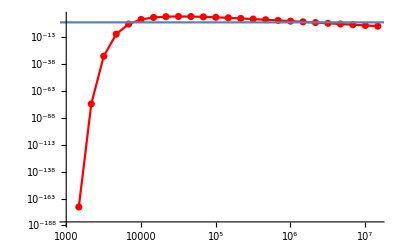

```mathematica
Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]]
```

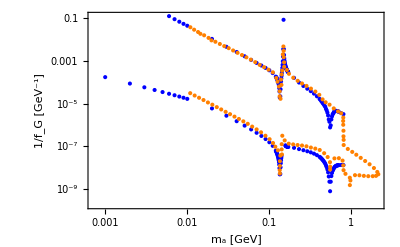

```mathematica
faprimemin=Import["./faprimemin.csv","Data"];
faprimemax=Import["./faprimemax.csv","Data"];
faexisting=Import["./existing.csv","Data"];
ListLogLogPlot[{falistmin,falistmax,faprimemin,faprimemax(*,faexisting*)},PlotStyle-> {Blue,Blue,Orange,Orange,Gray},Frame->True(*,Joined->True*),(*Mesh->Full,*)FrameLabel->{"m_a [GeV]","1/f_G [GeV^-1]"},ImageSize->400]
```

## Combining with GG-fusion

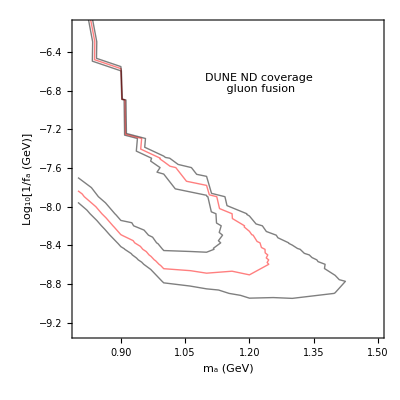

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.5},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->All,FrameLabel->{"m_a (GeV)","Log_10[1/f_a (GeV)]"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

#### Some massaging of GG-fusion results

```mathematica
listhighm=Flatten[Table[{#[[1]],#[[2]]*10^6,Abs[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1];
falistminhigh={};
falistmaxhigh={};
masslisthigh=Table[0.7+0.1*x,{x,1,25}];
(*masslisthigh={0.8};*)
For[nn=1,nn<Length[masslisthigh]+1,nn++,mass=masslisthigh[[nn]];
falisthigh={};
For[i=1,i<Length[listhighm]+1,i++,If[listhighm[[i]][[1]]== mass,AppendTo[falisthigh,{listhighm[[i]][[2]],listhighm[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[3,{fa,0.1,10^8}]];
If[Head[pts[[1,1]]]== Real,AppendTo[falistminhigh,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}],Continue];
If[Head[pts[[2,1]]]== Real,AppendTo[falistmaxhigh,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}],Continue]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pts
```

{}

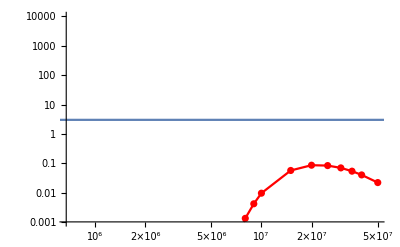

```mathematica
Show[ListLogLogPlot[{falisthigh},PlotStyle-> Red, Mesh-> All,Joined->True,PlotRange->{Automatic,{0.001,10^4}}],LogLogPlot[3,{fa,0.1,10^8}]]
```

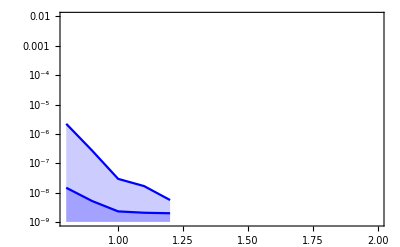

```mathematica
ListLogPlot[{falistmaxhigh,falistminhigh},PlotStyle->Blue,Frame->True,Joined->True,Filling->Bottom,PlotRange->{{0.8,2},{10^-9,10^-2}}]
```

#### Combined constraints from this study

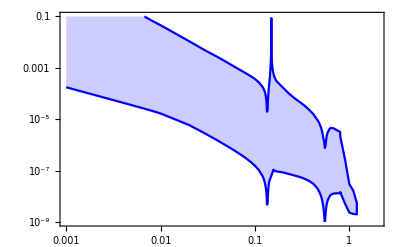

```mathematica
finaldata=Join[falistmin[[6;;Length[falistmin]]],falistminhigh,Reverse[falistmaxhigh],Reverse[falistmax],Reverse[falistmin[[1;;5]]]];
ListLogLogPlot[{finaldata},PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,PlotRange->{{0.001,2},{10^-9,10^-1}}]
```

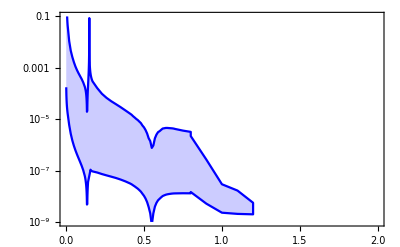

```mathematica
finaldata=Join[falistmin[[6;;Length[falistmin]]],falistminhigh,Reverse[falistmaxhigh],Reverse[falistmax],Reverse[falistmin[[1;;5]]]];
ListLogPlot[{finaldata},PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,PlotRange->{{0.001,2},{10^-9,10^-1}}]
```

## Other constraints

#### SN

```mathematica
SNErdata=Import["./SN-Ertas.csv","Data"];
SNErfinal=SNErdata;
SNErfinal[[All,1]]=SNErdata[[All,1]]/10^3;
SNErfinal[[All,2]]=SNErdata[[All,2]]*8/10^3;

SNChdata=Import["./SN-Chang.csv","Data"];
SNChfinal=SNChdata;
SNChfinal[[All,1]]=SNChdata[[All,1]]/10^3;
SNChfinal[[All,2]]=SNChdata[[All,2]]*8/10^3;
```

#### E787

```mathematica
E787data=Import["./E787.csv","Data"];
E787final=E787data;
E787final[[All,1]]=E787data[[All,1]]/10^3;
E787final[[All,2]]=E787data[[All,2]]*8/10^3;
(* This lies mostly inside the existing constraints *)
```

#### Cosmo Updated

```mathematica
mPi=135/1000;
cosmoupdata=Import["./cosmo-updated.csv","Data"];
cosmoupfinal=cosmoupdata;
cosmoupfinal[[All,1]]=cosmoupdata[[All,1]]/10^3;
cosmoupfinal[[All,2]]=cosmoupdata[[All,2]]/(4Pi 1/137(1-1/2 cosmoupfinal[[All,1]]^2/(cosmoupfinal[[All,1]]^2-mPi^2)*0.3));
cosmoupfinal={{0.001,11.70626048691387},{0.002235147269982729,0.1170626048691387},{0.002235147269982729,0.006170626048691387}(*,{0.0022364250792747055,0.00006465942195768839},{0.002248937556815591,0.00001089393490205172},{0.0022502704718624774,0.0020944936133703413},{0.002250386816321632,0.000019352920240147705},{0.002254823468473725,0.00011213412175697278},{0.00225633207021816,0.0002036277243515753},{0.002257804623544028,0.00036439949712197787},{0.002259268867514212,0.00064972423272586},{0.0022607804434767336,0.001179853775673186},{0.002263472251086027,0.0034103745928089307}*),{0.002266720602547271,0.00003314391376444828},{0.0022957311056152974,6.27263755634703*^-6},{0.0024646881191185003,3.747167421607878*^-6},{0.0025641180087891792,3.069153977635894*^-6},{0.002812418066823807,2.199093557990806*^-6},{0.003044673009022339,1.8443233301648131*^-6},{0.0034291281046179693,1.2832380279266037*^-6},{0.0037124035552801474,1.1001086838495513*^-6},{0.004126259634564507,7.910906312013432*^-7},{0.004526741979835589,6.781602584409422*^-7},{0.004899634170309927,4.797369572178778*^-7},{0.005303961653167458,3.8293713089526393*^-7},{0.005575544031732043,2.5785693953184947*^-7},{0.005663979436661325,2.2110216103747342*^-7},{0.006212153149229208,1.516088851055952*^-7},{0.007676770345635899,1.0315101478363848*^-7},{0.008880451584052302,8.775516986826593*^-8},{0.010548765678419725,7.38284509892575*^-8},{0.012365746007027842,6.337247492473373*^-8},{0.014523616324542197,5.588855580047699*^-8},{0.019919502596951008,4.021562342905403*^-8},{0.027373350621575896,3.030557774770426*^-8},{0.03251547477383241,2.5200403684445334*^-8},{0.03761397875725679,2.1488580880522387*^-8},{0.04648914988182168,1.661937631292043*^-8},{0.05377842844340939,1.4029622289937041*^-8},{0.06387986786722837,1.1383999769211611*^-8},{0.07488060082393705,9.301971986154322*^-9},{0.0877736057408347,7.3064579132212775*^-9},{0.09541985272912629,6.3067912598556505*^-9},{0.10425922584795719,5.404691155300291*^-9},{0.11901827054531404,3.690825943517982*^-9},{0.13135911149336377,1.3323427851371745*^-9},{0.1565254194730246,9.440384375535462*^-9},{0.16792049248935148,6.3282518426318925*^-9},{0.18270452257651637,4.755503543914546*^-9},{0.1994543734106064,4.014021625924125*^-9},{0.23379947341534565,3.095135696754999*^-9},{0.2740496411174068,2.400199203429628*^-9},{0.3386947002137496,1.7404543955214207*^-9},{0.39179077954839897,1.4345763008609994*^-9},{0.46535774584471856,1.1174808701844713*^-9},{0.5211820049881299,9.637570365414963*^-10},{0.6309814080029983,7.377150215886578*^-10},{0.8113894337745267,5.035447321432275*^-10}};
```

#### MATHUSLA

```mathematica
MATHUSLAdata={{0.051986049165234964,0.0013410615350441166},{0.05615116882977519,0.0011972671056295562},{0.06135190756683929,0.0010190062839289548},{0.06574109052394883,0.0009169398217634748},{0.07184726625566747,0.0007479162590887357},{0.07877924376980422,0.0006036018926056707},{0.08427250401696117,0.0005093936915100309},{0.09123131434952401,0.0004089443553025492},{0.10003121900422532,0.0003072402363479036},{0.1081400226613497,0.0002626697714272105},{0.1168236020518344,0.00022647444446013916},{0.12855061346128435,0.00014750914658613517},{0.1318194305229974,0.00010619352849286489},{0.13430835441547956,0.00007786677738783966},{0.13808028578459614,0.00013563644696357706},{0.14082288197818224,0.00023020494636883287},{0.14388626547749933,0.00039825132803679176},{0.14527357055239154,0.0006203817835499996},{0.1455007953816,0.0008497308174158022},{0.15093930890665544,0.00032516733994096607},{0.15684814848249393,0.0002610526457524175},{0.16612386530425693,0.00021932464039737623},{0.17888654845546403,0.00019509259852798657},{0.19476746137915052,0.0001773206451522168},{0.21081136652911742,0.00016709377502316128},{0.23206203656740648,0.00015827123828256198},{0.25050243634573227,0.00015274786618774483},{0.27315772847856146,0.0001418300393958118},{0.29465150184315364,0.00013226831475490682},{0.32217503714869317,0.00011757192787230062},{0.3583086883753024,0.00009853156222049971},{0.394273502913899,0.00007896383170834305},{0.42318761662406645,0.000052002883509156285},{0.44308164264186356,0.00003258686502081917},{0.47220769882573294,0.000020445560966569662},{0.4975094894982974,0.000013171368180059902},{0.5085685190629089,8.824974834469333*^-6},{0.5157724956399816,6.156500966029618*^-6},{0.5249147771904258,3.7790940752122992*^-6},{0.5344995190691871,2.2693090694872123*^-6},{0.5412830043235914,1.2797479596742952*^-6},{0.5469895833091688,7.736282549004089*^-7},{0.5636655574522306,2.243995659694941*^-6},{0.5756117482629969,4.048359774384981*^-6},{0.5880737767680206,6.429229321799808*^-6},{0.6029369974964814,0.000010085233250743535},{0.642745238498445,0.000014772598783853335},{0.7073613167373953,0.00001853413037364141},{0.7867762491886915,0.000021403832591842833},{0.8446229695761769,0.000024428435811159906},{0.8688013696936757,0.000015884339913404145},{0.8927494713934065,9.902137238361037*^-6},{0.9122808777820584,6.559272739815722*^-6},{0.932237068740376,4.113634421758444*^-6},{0.9422361037515662,2.780138286222321*^-6},{0.9461134406175632,1.8956231417578708*^-6},{0.9507694555449362,1.1575622403072976*^-6},{0.9758251264742642,2.7763540165072324*^-6},{1.034662160871887,3.129045642580573*^-6},{1.1257443072808435,2.416734495831251*^-6},{1.2115646746196418,1.7956090036884802*^-6},{1.3071045111900639,1.4556536283031732*^-6},{1.4463599017108961,1.2210564609961398*^-6},{1.608614998436379,1.1020832543801253*^-6},{1.7855122327638107,1.1065565303837093*^-6},{1.9260542251391493,1.1131964470120348*^-6},{2.105977247106503,1.0034185178289134*^-6},{2.3374973089515465,9.155816545795013*^-7},{2.521431965951965,8.598365835968232*^-7},{2.7514100880989814,7.903592091459243*^-7},{2.9679254083649207,7.504240302187265*^-7},{3.2517934570316767,7.012298549841548*^-7},{3.6019906189342876,6.490830035505879*^-7},{3.885424771817947,6.086526575798249*^-7},{4.239844176976012,5.7302153731272*^-7},{4.573499012868558,5.48151892206013*^-7},{4.990682948943958,5.160625457575881*^-7},{5.3834130914700795,4.902313405185819*^-7},{5.874488603174171,4.6476534264795224*^-7},{6.341273001086193,4.438190071210081*^-7},{6.9148083943352,4.185671397825762*^-7},{7.501399743142398,4.004009531004146*^-7},{8.139424402395397,3.8647587022428326*^-7},{8.830057469814603,3.90738100938952*^-7},{8.72681729677511,9.774959356393863*^-7},{8.101237318792263,1.1999347899935407*^-6},{7.336253197428219,1.5286349828597608*^-6},{6.6434633810106485,1.9095216197545745*^-6},{6.016083721337601,2.36975570618923*^-6},{5.458976612083826,2.9035835222238617*^-6},{4.8985761487038575,3.563212183971527*^-6},{4.435966744021444,4.393178957359106*^-6},{3.9805811240682307,5.374437589550066*^-6},{3.611938440981702,6.42099878733036*^-6},{3.2477014442028955,7.728939526602797*^-6},{2.9409719691596585,9.283034575769914*^-6},{2.6897281191819657,0.000010498217808759739},{2.493546693582708,0.000011610530043915159},{2.2626152887197972,0.000013806759566697802},{2.034440359454893,0.00001643890063553777},{1.8385426785984385,0.000018878013144756606},{1.6959430442222256,0.000016732897801108185},{1.5635936438355038,0.000016331684540030387},{1.432312407472916,0.000018942829036593995},{1.3216351052034685,0.000026430499555478746},{1.2300941563895087,0.00004073183856339808},{1.1665622808438887,0.00006486593801902743},{1.1102541758271152,0.0001072799617913539},{1.0539690540383773,0.0001659476593007306},{0.9602264977207403,0.000187624040090508},{0.951756430028416,0.00002978993061621992},{0.9507926728341004,0.00001755023417813856},{0.9506321264016955,0.0001307211967166101},{0.9496855732323125,0.000053204838466532},{0.9486682029048656,0.00007504952951834006},{0.9425274069930035,0.000012007897037266001},{0.9236681274110976,0.0003306024852858426},{0.917243325031361,0.00046703831477071413},{0.914127237552477,0.000728897153557709},{0.9046052962409415,0.0012201147008582046},{0.8951440464506721,0.0017851529439435415},{0.8920898456957065,0.002660046103570343},{0.876614635273472,0.005408355919748018},{0.8522384305284314,0.008939527578351378},{0.8053471673415395,0.013449473355639346},{0.7418100868486464,0.016676517812809825},{0.6877089749775992,0.01882430900232972},{0.6290304397711851,0.016128676141806245},{0.5936521216397767,0.010089184584217856},{0.5769706864204933,0.006502140188853409},{0.5610197760740107,0.003580117735041875},{0.5478914861350653,0.00015435546576991082},{0.5471260160952859,0.0009974511567335702},{0.547080074866204,0.0006675550113672203},{0.5467198237899847,0.00044866570948515064},{0.5466522982909005,0.0003047907531769937},{0.5464296006680749,0.0013644972904153366},{0.5463172012938958,0.00008945644498095216},{0.5413323886771162,0.0022219100157732548},{0.5279911529533059,0.005035367091236525},{0.5169519904596053,0.007847501648624515},{0.5007967376904544,0.012836122679703398},{0.4800105562200787,0.020548966226081804},{0.4517749796872196,0.032983812708956464},{0.42111594751391407,0.04828376917473738},{0.3854393485926413,0.06726437030992719},{0.35278278385137823,0.09168459496836753},{0.3217487983395027,0.12307697748984972},{0.29240514039113763,0.16306985998965906},{0.265737454167084,0.2155873686046263},{0.241500545516301,0.28008820751118924},{0.2198071889367948,0.36016430617409634},{0.19889446819935394,0.4923307181614122},{0.18191100116594297,0.6374011255947585},{0.16709190511991942,0.9035971298344082},{0.13969867731174612,0.6671510084322959},{0.13837254545085456,0.40670239468404296},{0.1368518207693431,0.1930597875315236},{0.13612805736873962,0.10594863618342412},{0.13401020350166742,0.06829924755998222},{0.13283386188699423,0.15796202255928482},{0.13014517227268427,0.2974693875306909},{0.12669369104304368,0.41931307621366465},{0.1205755596551044,0.6443905147304573},{0.11131519046541996,0.9081132542977353}};
MATHUSLAfinal=MATHUSLAdata;
MATHUSLAfinal[[All,1]]=MATHUSLAdata[[All,1]];
MATHUSLAfinal[[All,2]]=MATHUSLAdata[[All,2]]*8/10^3;
```

#### BD

```mathematica
BDdata1=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/BD1.csv","Data"];
BDdata2=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/BD2.csv","Data"];
mPi=135/1000;

BDdata=Join[BDdata2,BDdata1];
BDfinal=BDdata;
BDfinal[[All,2]]=BDdata[[All,2]]/Abs[(4Pi 1/137(1-1/2 BDfinal[[All,1]]^2/(BDfinal[[All,1]]^2-mPi^2)*0.3))];
BDEinvCombined={{0.000010920125464910844,0.00002160587412812246},{0.000015099925497952564,0.000021591088141106817},{0.00002014111020326543,0.00002142109591440676},{0.000028527012923863416,0.000021405350888188472},{0.000040892348220491105,0.00002138907510838848},{0.000054544460639285476,0.000021376063395329595},{0.00007275439821623505,0.000021363059597745117},{0.00009588595446689901,0.000021506946495581083},{0.00012637196498694385,0.000021494408060776485},{0.0001665507072798067,0.00002148187693581233},{0.00023248974226032122,0.000021289628263767246},{0.00026971985562240916,0.00002126817314974239},{0.0003165077008949862,0.000021260987764339733},{0.0003671921632275217,0.00002125431779442595},{0.0004259930622681499,0.00002124764991700661},{0.0004998893552889205,0.000021240471465313577},{0.0005799399294990664,0.000021160200002799818},{0.0006728095292867232,0.000021153561651893778},{0.007624258840257991,0.00001967248142121611},{0.009968009402770565,0.000015378723122742855},{0.013111620717499745,0.000011894543299199586},{0.016889750926599792,9.717005033329995*^-6},{0.020868009551400078,7.759431186310877*^-6},{0.028175319117739153,6.232645669122315*^-6},{0.03979593840097845,4.646928409985804*^-6},{0.0502077942914208,3.8680554548070046*^-6},{0.06531694793993421,3.2273053163825055*^-6},{0.07155114658184013,2.966577773971954*^-6},{0.08524869794668946,2.496068422371497*^-6},{0.10374757464305104,2.041778650074364*^-6},{0.11180397992342303,1.7374297815275868*^-6},{0.12237258401683224,1.2979488002544983*^-6},{0.13073125587021145,6.569011888616876*^-7},{0.14675069728790877,0.00008188362859111132},{0.15677451865884143,4.622330760740398*^-6},{0.18190436252613193,2.7722025803850086*^-6},{0.19432648784393244,2.505863608132181*^-6},{0.21457928151064365,2.3379625112612025*^-6},{0.22922936848179737,2.171498188177068*^-6},{0.2531160167778835,2.0648600416707846*^-6},{0.2749109024873609,1.984438163786679*^-6},{0.30355775556716946,1.910577625118173*^-6},{0.3296959931747004,1.8485811795817494*^-6},{0.36406243551059264,1.8344791978193115*^-6},{0.3889412486196086,1.8270321896317435*^-6},{0.42949591391203534,1.8635052163674013*^-6},{0.4742791892652831,1.9027571699457766*^-6},{0.506734760940492,2.044793301119354*^-6},{0.5193048088236075,2.196805144434459*^-6},{0.5250218431449816,2.767636965930136*^-6},{0.5113626251210163,3.617960502068029*^-6},{0.4953490856725324,4.281690148028179*^-6},{0.46473755464824074,5.2585771481785855*^-6},{0.43601775181878144,6.4606351428948185*^-6},{0.4090961886081404,8.330053442407033*^-6},{0.38379842810596715,9.882711676811349*^-6},{0.3600701874930164,0.000011873302062826659},{0.33780893934630607,0.000014275841389926102},{0.31692852249120507,0.00001738779608473104},{0.2926167629579812,0.000021246078435681266},{0.28032702568913664,0.000023976545360924103},{0.2701777041943778,0.000026659151057125647},{0.2534776633385921,0.000032670383314911886},{0.23402655575375958,0.0000393951195479295},{0.2225776857746384,0.00004464689049957632},{0.21607734330810144,0.00004963966432162394},{0.20838964741493138,0.00005595499611986536},{0.19950478756869527,0.00006341339868536953},{0.19191391058864166,0.00007370684586090037},{0.18128232323347077,0.00008645915446171524},{0.17384401224446056,0.00010403334322947027},{0.16737685590115894,0.00012214978973411393},{0.16009006801737677,0.00016003198761331127},{0.15453949761342137,0.00023294693479113067},{0.14742864463536393,0.001316679895595742},{0.14041873604160057,0.00010538983428914224},{0.13245228938133027,0.000024683735109846348},{0.1275967537325181,0.000058721825805733795},{0.11899377275261258,0.0000984539964628011},{0.11593894175538705,0.00011376599950374806},{0.11140860891867066,0.00013833226352308174},{0.1070446917927827,0.0001555481229513561},{0.10042524372308498,0.00019448052140940753},{0.09271670356892263,0.000235723557661085},{0.0852591120750397,0.00029075392754295633},{0.07654862526793466,0.00037183364120357983},{0.07139241999003036,0.0004635393647896649},{0.06631109131365134,0.0005801128328594424},{0.0622108313873191,0.0006934282246270304},{0.059096083680362926,0.0008026208293098021},{0.05526473441652065,0.0009577445086961459},{0.0521974781288204,0.0011571767736825922},{0.047429839741878956,0.0014541479073565968},{0.04379105313583935,0.0017529044926470172},{0.04108485821103366,0.002153168962216071},{0.03793231166020225,0.0025621163402280867},{0.0339221986761817,0.0033693459242655492},{0.03182451191763014,0.003988740576444283},{0.029172455278022903,0.004954427719514267},{0.027595299668051184,0.005815886873955773},{0.025917887729407073,0.007393895078924164},{0.024341278080199424,0.00903168479868083},{0.022486964487563498,0.011481774301700885},{0.020592711709274757,0.014836181900853118},{0.02390302779476118,0.01989564126520568},{0.025084003969468954,0.023511276297233576},{0.024299183090292335,0.028480864511797644},{0.024303356148782526,0.03287755207955075},{0.023329780234944038,0.040626694411786415},{0.022443207231035173,0.046547933881036195},{0.021056866901585224,0.05845786137474707},{0.01975559684158879,0.07167473170497954},{0.018240917324733888,0.09001103643476199},{0.017112932340588506,0.10645870994750734},{0.016313075997886627,0.12145936965515879},{0.015304086192049527,0.1419353821240087},{0.014130505820524594,0.17609114880796392},{0.012840091866218569,0.22375670504342965},{0.011667408681426709,0.28205151844104115},{0.010601927575206433,0.3583654478058645},{0.009480371037479498,0.4401476922634161},{0.008894567700042088,0.54270029498798},{0.008212182223102597,0.6520303408765429},{0.007582727616136698,0.8349858021783251},{0.007000584932124397,0.9562973485955713}};
```

#### CHARM

```mathematica
charmdata1=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/CHARM1.csv"];
charmdata2=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/CHARM2.csv"];
charmfinal=Join[charmdata1,Reverse[charmdata2]];
```

#### CHARM from CODEX-b paper

```mathematica
charmdata1=Import["./CHARM-CODEXb-1.csv","Data"];
charmdata2=Import["./CHARM-CODEXb-2.csv","Data"]//Reverse;
CHARMfromCODEXb=Join[charmdata1,charmdata2];
CHARMfromCODEXbfinal=CHARMfromCODEXb;
CHARMfromCODEXbfinal[[All,1]]=CHARMfromCODEXb[[All,1]];
CHARMfromCODEXbfinal[[All,2]]=CHARMfromCODEXb[[All,2]]*8/10^3;
```

#### NA62 projection

```mathematica
NA62data=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/NA62.csv","Data"];
NA62final=NA62data;
NA62final[[All,1]]=NA62data[[All,1]]/10^3;
NA62final[[All,2]]=NA62data[[All,2]]*8/10^3;

NA62data2=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/NA62-2.csv","Data"];
NA62final2=NA62data2;
NA62final2[[All,1]]=NA62data2[[All,1]]/10^3;
NA62final2[[All,2]]=NA62data2[[All,2]]*8/10^3;
NA62Fin=Join[NA62final,Reverse[NA62final2]];
```

#### E787+E949: K → π + inv

```mathematica
Einvdata=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/E787-E949.csv","Data"];
Einvfinal=Einvdata;
Einvfinal[[All,1]]=Einvdata[[All,1]]/10^3;
Einvfinal[[All,2]]=Einvdata[[All,2]]*8/10^3;

Einvdata2=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/E787-E949-2.csv","Data"];
Einvfinal2=Einvdata2;
Einvfinal2[[All,1]]=Einvdata2[[All,1]]/10^3;
Einvfinal2[[All,2]]=Einvdata2[[All,2]]*8/10^3;
EinvFin=Join[Einvfinal,Reverse[Einvfinal2]];
EinvFin={};
```

#### Plotting

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G [\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],None},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.01,5},{10^-9,10^-2}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->2,ShowMinorTicks->True],LogTicks[10,10^-10,1,TickLabelStep->2,ShowMinorTicks-> True]},{LogTicks[10,0.01,10],LogTicks[10,0.01,10,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["c_3=1,c_1=c_2=0",Magnification->1.5],FrameStyle->{Gray,Thickness[1]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[1.5],Log[10^-2.5]}],20],Style[Text[Style[Rotate["SN1987A",-0.2],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-0.2],{15,Black},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-8]}],20],Style[Text[Style[Rotate["MATHUSLA200",-0.3],{15,Gray},FontFamily->"CMU Serif"],{Log[2],Log[10^-7.5]}],20],Style[Text[Style[Rotate["CHARM: CODEX-b paper",-0.45],{15,Orange},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-4.2]}],20],Style[Text[Style[Rotate["DUNE ND 10 and 3 events",-0.45],{15,Blue},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-5.8]}],20],Style[Text[Style[Rotate["Electron Beam Dump",-0.45],{15,Purple},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-3.3]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}](*,ListLogLogPlot[falistAll3ev,PlotStyle->{Blue,DotDashed},Filling->Top,Joined->True]*),ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,DotDashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChfinal,Last],PlotStyle->{Gray,Dotted},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Black,Dotted},Filling->Bottom,Joined->True],ListLogLogPlot[MATHUSLAfinal,PlotStyle->{Gray,Dashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[CHARMfromCODEXbfinal,PlotStyle->{Orange}(*,Filling->Top*),Joined->True],ListLogLogPlot[BDfinal,PlotStyle->{Purple},Filling->Top,Joined->True]]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G [\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],None},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,5},{10^-9,10^-1}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->True],LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks-> True]},{LogTicks[10,0.001,10],LogTicks[10,0.001,10,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["c_3=1,c_1=c_2=0",Magnification->1.5],FrameStyle->{Gray,Thickness[1]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[1],Log[10^-2]}],20],Style[Text[Style[Rotate["SN1987A",-0.2],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-0.2],{15,Black},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-8]}],20],Style[Text[Style[Rotate["MATHUSLA200",-0.3],{15,Gray},FontFamily->"CMU Serif"],{Log[2],Log[10^-7.5]}],20],Style[Text[Style[Rotate["CHARM",-0.45],{15,Black},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-4.2]}],20],Style[Text[Style[Rotate["DUNE ND 3 events",-0.55],{15,Blue},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-6.2]}],20],Style[Text[Style[Rotate["Existing Beam Dump",-0.65],{15,Black},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-2.8]}],20],Style[Text[Style[Rotate["NA62",0.0],{15,Gray},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-5.4]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}](*,ListLogLogPlot[falistAll3ev,PlotStyle->{Blue,DotDashed},Filling->Top,Joined->True]*),ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,DotDashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChfinal,Last],PlotStyle->{Gray,Dotted},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Black,Dotted},Filling->Bottom,Joined->True],ListLogLogPlot[MATHUSLAfinal,PlotStyle->{Gray,Dashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[CHARMfromCODEXbfinal,PlotStyle->{Dotted,Black},Filling->Axis,Joined->True](*,ListLogLogPlot[BDfinal,PlotStyle->{Gray},Filling->Top,Joined->True]*),ListLogLogPlot[NA62Fin,PlotStyle->{Gray,Dashed}(*,Filling->Top*),Joined->True](*,
ListLogLogPlot[NA62final2,PlotStyle->{Red,Dashed},Filling->Top,Joined->True]*),ListLogLogPlot[BDEinvCombined,PlotStyle->{Black},Filling->Top,Joined->True]]
```

-Graphics-

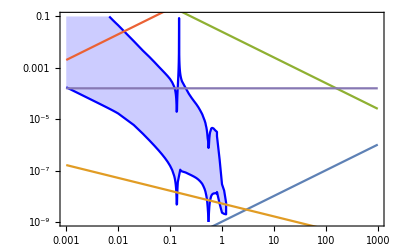

```mathematica
Λmax=1658.047000156266;
Mp=2.4*10^18;
dim=6;
Show[ListLogLogPlot[{finaldata},Joined->True,Filling->Top,Frame->True,PlotStyle-> Blue,PlotRange->{{10^-3,10^3},{10^-9,10^-1}}],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^3}]]
```

```mathematica
Show[ListLogLogPlot[finaldata,PlotStyle->Blue,Frame->True,Joined->True,Filling->Top,FrameLabel->{{Style[MaTeX["g_{agg}=1/f_G [\\text{GeV}^{-1}]",Magnification->1.5],FontSize->15,Black],None},{Style[MaTeX["m_a[\\text{GeV}]",Magnification->1.5],FontSize->15,Black],None}},ImageSize->600,PlotRange->{{0.001,10^3},{10^-9,10^-1}},FrameTicks->{{LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks->True],LogTicks[10,10^-10,1,TickLabelStep->1,ShowMinorTicks-> True]},{LogTicks[10,0.001,10^3],LogTicks[10,0.001,10^3,ShowTickLabels-> False]}},FrameTicksStyle->Directive[Black,15,AbsoluteThickness[0.5]],Epilog->{Style[Text[Style[Framed[MaTeX["c_3=1,c_1=c_2=0",Magnification->1.5],FrameStyle->{Gray,Thickness[1]},RoundingRadius->5],{15,Black},FontFamily->"CMU Serif"],{Log[1],Log[10^-2]}],20],Style[Text[Style[Rotate["SN1987A",-0.2],{15,Gray},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-7.2]}],20],Style[Text[Style[Rotate["BBN+N_eff",-0.2],{15,Black},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-8]}],20],Style[Text[Style[Rotate["MATHUSLA200",-0.3],{15,Gray},FontFamily->"CMU Serif"],{Log[2],Log[10^-7.5]}],20],Style[Text[Style[Rotate["CHARM",-0.45],{15,Black},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-4.2]}],20],Style[Text[Style[Rotate["DUNE ND 3 events",-0.55],{15,Blue},FontFamily->"CMU Serif"],{Log[0.04],Log[10^-6.2]}],20],Style[Text[Style[Rotate["Existing Beam Dump",-0.65],{15,Black},FontFamily->"CMU Serif"],{Log[0.03],Log[10^-2.8]}],20],Style[Text[Style[Rotate["NA62",0.0],{15,Gray},FontFamily->"CMU Serif"],{Log[0.007],Log[10^-5.4]}],20],Style[Text[Style[Rotate["Colored Particles",0.0],{15,Black},FontFamily->"CMU Serif"],{Log[10],Log[10^-4]}],20],Style[Text[Style[Rotate["Higgs VEV",0.0],{15,Purple},FontFamily->"CMU Serif"],{Log[10^2],Log[10^-8]}],20],Style[Text[Style[Rotate["PQ",0.0],{15,Green},FontFamily->"CMU Serif"],{Log[10^-2],Log[10^-8]}],20],Style[Text[Style[Rotate["QCD Axion",0.0],{15,Orange},FontFamily->"CMU Serif"],{Log[10^-2],Log[10^-1.5]}],20],Style[Text[Style[Rotate["f_a < Λ_QCD'",0.0],{15,Red},FontFamily->"CMU Serif"],{Log[10^2],Log[10^-2]}],20]},LabelStyle->{FontFamily->"CMU Serif",FontSize->12}](*,ListLogLogPlot[falistAll3ev,PlotStyle->{Blue,DotDashed},Filling->Top,Joined->True]*),ListLogLogPlot[SortBy[SNErfinal,Last],PlotStyle->{Gray,DotDashed},Filling->Top,Joined->True],ListLogLogPlot[SortBy[SNChfinal,Last],PlotStyle->{Gray,Dotted},Filling->Top,Joined->True],ListLogLogPlot[cosmoupfinal,PlotStyle->{Black,Dotted},Filling->Bottom,Joined->True],ListLogLogPlot[MATHUSLAfinal,PlotStyle->{Gray,Dashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[CHARMfromCODEXbfinal,PlotStyle->{Dotted,Black},Filling->Axis,Joined->True](*,ListLogLogPlot[BDfinal,PlotStyle->{Gray},Filling->Top,Joined->True]*),ListLogLogPlot[NA62Fin,PlotStyle->{Gray,Dashed}(*,Filling->Top*),Joined->True],ListLogLogPlot[BDEinvCombined,PlotStyle->{Black},Filling->Top,Joined->True],LogLogPlot[{1/(4 Pi^2 Sqrt[0.6]*(alphas[10^6]^-0.4*Λmax)^2/ma),1/(4 Pi^2(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2))),1/(4 Pi^2 ma),ma/(4 Pi^2 mPi fpi),1/(2000Pi)},{ma,10^-3,10^3},PlotStyle->{Purple, Green, Red,Orange,Black}],ListLogLogPlot[scaledfaMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogLogPlot[scaledfaMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogLogPlot[scaledfaMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogLogPlot[scaledfaMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom]]
```

-Graphics-

## CMS Track Trigger Search

#### Efficiency factors, m_a,f_a in GeV

```mathematica
faMaPlane3evwPT30={{1,8181},{1.3,44323},{1.5,65725},{1.8,58076},{2,55909},{4,91016},{6,167220},{8,244103},{10,331492},{12,444057},{14,611733},{16,788218},{18,10^6},{20,1.3*10^6},{22,2.18*10^6},{22,2.47*10^6},{20,3*10^6},{18,3.4*10^6},{16,3.7*10^6},{14,3.9*10^6},{12,3.9*10^6},{10,3.78*10^6},{8,3.4*10^6},{6,2.84*10^6},{4,2*10^6},{2,783193},{1.8,651661},{1.5,598502},{1.3,340571},{1,164980}};
faMaPlane10evwPT30={{1,10232},{1.3,56618},{1.5,86419},{1.8,72533},{2,71082},{4,118362},{6,198543},{8,307219},{10,454181},{12,652662},{14,1.16*10^6},{14,1.54*10^6},{12,1.9*10^6},{10,2.1*10^6},{8,2.1*10^6},{6,1.9*10^6},{4,1.43*10^6},{2,541037},{1.8,453630},{1.5,413415},{1.3,198115},{1,112029}};
faMaPlane3evwHT100={{1,10880},{1.3,68957},{1.5,99307},{1.8,78132},{2,76631},{3,91054},{4,128554},(*{5,506851},*){6,211161},{8,328672},{10,505132},{12,740787},{13,1.16*10^6},{13,1.26*10^6},{12,1.5*10^6},{10,1.8*10^6},{8,1.8*10^6},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,1.67*10^6},(*{5,1.6*10^6},*){4,1.26*10^6},{3,941794},{2,474137},{1.8,391229},{1.5,360560},{1.3,155171},{1,100209}};
faMaPlane10evwHT100={(*{1,13023},*){1.8,137614},{2,107819},{3,130311},{4,172397},{5,239091},{6,306412},{7,459224},{7.5,601353},{7.5,679669},{7,780808},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,884514},{5,888240},{4,789501},{3,605536},{2,287247},{1.8,202213}(*,{1,74655}*)};
```

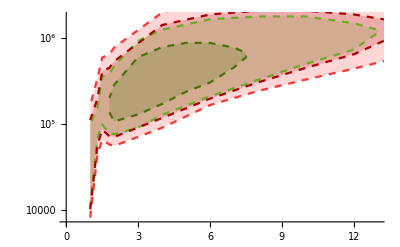

```mathematica
Show[ListLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom]]
```

```mathematica
faMaPlane10evwHT100[[All,2]]
```

{137614,107819,130311,172397,239091,306412,459224,601353,679669,780808,884514,888240,789501,605536,287247,202213}

```mathematica
scaledfaMaPlane10evwHT100=faMaPlane10evwHT100;
scaledfaMaPlane10evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane10evwHT100[[All,2]]);
scaledfaMaPlane10evwPT30=faMaPlane10evwPT30;
scaledfaMaPlane10evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane10evwPT30[[All,2]]);
scaledfaMaPlane3evwHT100=faMaPlane3evwHT100;
scaledfaMaPlane3evwHT100[[All,2]]=1/(4 Pi^2 faMaPlane3evwHT100[[All,2]]);
scaledfaMaPlane3evwPT30=faMaPlane3evwPT30;
scaledfaMaPlane3evwPT30[[All,2]]=1/(4 Pi^2 faMaPlane3evwPT30[[All,2]]);
```